```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["Infrastructure.m"];
Get["MMA2TxtFormat3.m"];
```

## Simplification problem

the precise definition is that, minimize the LeafCounts of a math expression, but do not over-count identical subexpressions.

The corresponding math object is called “directed acyclic graph” (DAG). And we want to minimize leaf counts of math expressions as DAG.

This could be useful for physics. For example, imagine we have a scalar expression on O(3) irreps : ({ph1, ph2, ph3}.{f1, f2, f3})^2 + 2 ({ph1, ph2, ph3}.{f1, f2, f3} + 4)^3. If we just Expand and Simplify it in Mathematica, it won’t go back to this form. But s^2 + 2 (s + 4)^3 with s={ph1, ph2, ph3}.{f1, f2, f3} has minimal leafcounts as DAG.

#### superiority over Mathematica

Assume AI could suggest the correct substitution rule, the simplification result is superior than Mathematica

```mathematica
{long,short,sub}=RandomPolynomial$ON$LSS[5,3,2,3,ComplexityCriteria];
```

```mathematica
long
short
sub
```

-4+5 a[3] a[5]-4 a[3]^2 a[5]^2-5 a[3]^3 a[5]^3+5 a[4] a[6]-8 a[3] a[4] a[5] a[6]-15 a[3]^2 a[4] a[5]^2 a[6]-4 a[4]^2 a[6]^2-15 a[3] a[4]^2 a[5] a[6]^2-5 a[4]^3 a[6]^3

-4+5 s-4 s^2-5 s^3

a[3] a[5]+a[4] a[6]

```mathematica
simplified=PolySimplifyWithHint[{long,sub}]/.s->sub
```

-4+5 (a[3] a[5]+a[4] a[6])-4 (a[3] a[5]+a[4] a[6])^2-5 (a[3] a[5]+a[4] a[6])^3

```mathematica
simplified//FullSimplify
```

-3-3 (a[1] a[3]+a[2] a[4])-2 (a[1] a[3]+a[2] a[4])^2+4 (a[1] a[3]+a[2] a[4])^3

```mathematica
simplified//Expand//FullSimplify
```

-3+4 a[1]^3 a[3]^3+2 a[1]^2 a[3]^2 (-1+6 a[2] a[4])+a[2] a[4] (-3+2 a[2] a[4] (-1+2 a[2] a[4]))+a[1] a[3] (-3+4 a[2] a[4] (-1+3 a[2] a[4]))

```mathematica
examples=Table[Module[{long,short,sub,simplified},
{long,short,sub}=RandomPolynomial$ON$LSS[5,3,2,3,ComplexityCriteria];
simplified=PolySimplifyWithHint[{long,sub}]/.s->sub;
{long,simplified,long//FullSimplify}
],20];
```

```mathematica
Grid[{{"Raw","ours","MMA"},#}//Transpose]&/@examples//TableForm
```

```mathematica
{{}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", a[5]^2-3 a[5]^4+a[6]^2-6 a[5]^2 a[6]^2-3 a[6]^4}, {"ours", a[5]^2+a[6]^2-3 (a[5]^2+a[6]^2)^2}, {"MMA", -(a[5]^2+a[6]^2) (-1+3 a[5]^2+3 a[6]^2)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 1+a[1] a[3]+a[1]^2 a[3]^2+a[2] a[4]+2 a[1] a[2] a[3] a[4]+a[2]^2 a[4]^2}, {"ours", 1+a[1] a[3]+a[2] a[4]+(a[1] a[3]+a[2] a[4])^2}, {"MMA", 1+a[1]^2 a[3]^2+a[2] a[4] (1+a[2] a[4])+a[1] a[3] (1+2 a[2] a[4])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -5+4 a[1] a[5]+2 a[1]^2 a[5]^2+4 a[2] a[6]+4 a[1] a[2] a[5] a[6]+2 a[2]^2 a[6]^2}, {"ours", -5+4 (a[1] a[5]+a[2] a[6])+2 (a[1] a[5]+a[2] a[6])^2}, {"MMA", -5+2 a[1]^2 a[5]^2+4 a[1] a[5] (1+a[2] a[6])+2 a[2] a[6] (2+a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -1-4 a[5]^2+4 a[5]^4-4 a[6]^2+8 a[5]^2 a[6]^2+4 a[6]^4}, {"ours", -1-4 (a[5]^2+a[6]^2)+4 (a[5]^2+a[6]^2)^2}, {"MMA", -1+4 a[5]^4-4 a[6]^2+4 a[6]^4+a[5]^2 (-4+8 a[6]^2)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -2+3 a[1] a[5]-2 a[1]^2 a[5]^2+3 a[2] a[6]-4 a[1] a[2] a[5] a[6]-2 a[2]^2 a[6]^2}, {"ours", -2+3 (a[1] a[5]+a[2] a[6])-2 (a[1] a[5]+a[2] a[6])^2}, {"MMA", -2-2 a[1]^2 a[5]^2+a[1] a[5] (3-4 a[2] a[6])+a[2] a[6] (3-2 a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -1-4 a[3] a[5]+4 a[3]^2 a[5]^2-2 a[3]^3 a[5]^3-4 a[4] a[6]+8 a[3] a[4] a[5] a[6]-6 a[3]^2 a[4] a[5]^2 a[6]+4 a[4]^2 a[6]^2-6 a[3] a[4]^2 a[5] a[6]^2-2 a[4]^3 a[6]^3}, {"ours", -1-4 (a[3] a[5]+a[4] a[6])+4 (a[3] a[5]+a[4] a[6])^2-2 (a[3] a[5]+a[4] a[6])^3}, {"MMA", -1-2 a[3]^3 a[5]^3+2 a[3]^2 a[5]^2 (2-3 a[4] a[6])-2 a[4] a[6] (2+a[4] a[6] (-2+a[4] a[6]))-2 a[3] a[5] (2+a[4] a[6] (-4+3 a[4] a[6]))}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -4+2 a[1] a[5]-3 a[1]^2 a[5]^2+2 a[2] a[6]-6 a[1] a[2] a[5] a[6]-3 a[2]^2 a[6]^2}, {"ours", -4+2 (a[1] a[5]+a[2] a[6])-3 (a[1] a[5]+a[2] a[6])^2}, {"MMA", -4-3 a[1]^2 a[5]^2+2 a[1] a[5] (1-3 a[2] a[6])+a[2] a[6] (2-3 a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 2-4 a[1]^4-8 a[1]^2 a[2]^2-4 a[2]^4}, {"ours", 2-4 (a[1]^2+a[2]^2)^2}, {"MMA", 2-4 (a[1]^2+a[2]^2)^2}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 5+a[5]^4+2 a[5]^2 a[6]^2+a[6]^4}, {"ours", 5+(a[5]^2+a[6]^2)^2}, {"MMA", 5+(a[5]^2+a[6]^2)^2}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 5+2 a[3]^2+2 a[4]^2}, {"ours", False}, {"MMA", 5+2 a[3]^2+2 a[4]^2}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 5-5 a[1] a[5]-4 a[1]^2 a[5]^2-5 a[2] a[6]-8 a[1] a[2] a[5] a[6]-4 a[2]^2 a[6]^2}, {"ours", 5-5 (a[1] a[5]+a[2] a[6])-4 (a[1] a[5]+a[2] a[6])^2}, {"MMA", 5-4 a[1]^2 a[5]^2-a[2] a[6] (5+4 a[2] a[6])-a[1] a[5] (5+8 a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 4-2 a[1] a[5]+5 a[1]^2 a[5]^2-2 a[2] a[6]+10 a[1] a[2] a[5] a[6]+5 a[2]^2 a[6]^2}, {"ours", 4-2 (a[1] a[5]+a[2] a[6])+5 (a[1] a[5]+a[2] a[6])^2}, {"MMA", 4+5 a[1]^2 a[5]^2+a[2] a[6] (-2+5 a[2] a[6])+2 a[1] a[5] (-1+5 a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -4+4 a[3]^2+4 a[4]^2}, {"ours", False}, {"MMA", 4 (-1+a[3]^2+a[4]^2)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 2-3 a[1] a[5]+4 a[1]^2 a[5]^2-3 a[2] a[6]+8 a[1] a[2] a[5] a[6]+4 a[2]^2 a[6]^2}, {"ours", 2-3 (a[1] a[5]+a[2] a[6])+4 (a[1] a[5]+a[2] a[6])^2}, {"MMA", 2+4 a[1]^2 a[5]^2+a[2] a[6] (-3+4 a[2] a[6])+a[1] a[5] (-3+8 a[2] a[6])}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -5-5 a[5]^2+a[5]^4-5 a[6]^2+2 a[5]^2 a[6]^2+a[6]^4}, {"ours", -5-5 (a[5]^2+a[6]^2)+(a[5]^2+a[6]^2)^2}, {"MMA", -5+a[5]^4-5 a[6]^2+a[6]^4+a[5]^2 (-5+2 a[6]^2)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -2-5 a[3]^2-3 a[3]^4-5 a[4]^2-6 a[3]^2 a[4]^2-3 a[4]^4}, {"ours", -2-5 (a[3]^2+a[4]^2)-3 (a[3]^2+a[4]^2)^2}, {"MMA", -(1+a[3]^2+a[4]^2) (2+3 a[3]^2+3 a[4]^2)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", 5-3 a[1] a[3]+a[1]^2 a[3]^2-3 a[1]^3 a[3]^3-3 a[2] a[4]+2 a[1] a[2] a[3] a[4]-9 a[1]^2 a[2] a[3]^2 a[4]+a[2]^2 a[4]^2-9 a[1] a[2]^2 a[3] a[4]^2-3 a[2]^3 a[4]^3}, {"ours", 5-3 (a[1] a[3]+a[2] a[4])+(a[1] a[3]+a[2] a[4])^2-3 (a[1] a[3]+a[2] a[4])^3}, {"MMA", -(-1+a[1] a[3]+a[2] a[4]) (5+3 a[1]^2 a[3]^2+2 a[1] a[3] (1+3 a[2] a[4])+a[2] a[4] (2+3 a[2] a[4]))}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -5-5 a[5]^2-a[5]^4-5 a[5]^6-5 a[6]^2-2 a[5]^2 a[6]^2-15 a[5]^4 a[6]^2-a[6]^4-15 a[5]^2 a[6]^4-5 a[6]^6}, {"ours", -5-5 (a[5]^2+a[6]^2)-(a[5]^2+a[6]^2)^2-5 (a[5]^2+a[6]^2)^3}, {"MMA", -5-5 a[5]^6-a[5]^4 (1+15 a[6]^2)-a[6]^2 (5+a[6]^2+5 a[6]^4)-a[5]^2 (5+2 a[6]^2+15 a[6]^4)}}}, {{{"\!\(\*\nStyleBox[\"Raw\",\nFontColor->RGBColor[1, 0, 0]]\)", -1-5 a[1] a[5]-3 a[1]^2 a[5]^2-5 a[2] a[6]-6 a[1] a[2] a[5] a[6]-3 a[2]^2 a[6]^2}, {"ours", -1-5 (a[1] a[5]+a[2] a[6])-3 (a[1] a[5]+a[2] a[6])^2}, {"MMA", -1-3 a[1]^2 a[5]^2-a[2] a[6] (5+3 a[2] a[6])-a[1] a[5] (5+6 a[2] a[6])}}}}
```

```mathematica
{long,short,sub}=RandomPolynomial$PolyNInPoly1$LSS[4,3,2,2,{x,y},ComplexityCriteria];
```

```mathematica
long
short
sub
```

7+16 x+4 x^2-8 x^3+8 x y+4 x^2 y-12 x^3 y+x^2 y^2-6 x^3 y^2-x^3 y^3

1-3 s+4 s^2+s^3

-1-2 x-x y

```mathematica
simplified=PolySimplifyWithHint[{long,sub}]/.s->sub
```

1-3 (-1-2 x-x y)+4 (-1-2 x-x y)^2+(-1-2 x-x y)^3

```mathematica
simplified//FullSimplify
```

7-x (2+y) (-8+x (2+y) (-1+x (2+y)))

```mathematica
simplified//Expand//FullSimplify
```

7-x (2+y) (-8+x (2+y) (-1+x (2+y)))

```mathematica
examples=Table[Module[{long,short,sub,simplified},
{long,short,sub}=RandomPolynomial$PolyNInPoly1$LSS[4,3,2,2,{x,y},ComplexityCriteria];
simplified=PolySimplifyWith9Hint[{long,sub}]/.s->sub;
{long,simplified,long//FullSimplify}
],20];
```

```mathematica
Grid[{{"Raw","ours","MMA"},#}//Transpose]&/@examples//TableForm
```

Raw | 3+x-4 x^2+x^3-2 y+14 x y+10 x^2 y-6 x^3 y-16 y^2-20 x y^2+8 x^2 y^2+12 x^3 y^2-8 y^3-24 x y^3-24 x^2 y^3-8 x^3 y^3
ours | 3+x-2 y-2 x y-4 (x-2 y-2 x y)^2+(x-2 y-2 x y)^3
MMA | 3+x-4 x^2+x^3-2 (1+x) (1+x (-8+3 x)) y+4 (1+x)^2 (-4+3 x) y^2-8 (1+x)^3 y^3
Raw | -27-90 x-2 x^2+152 x^3+4 x^4-96 x^5+32 x^6+90 y+274 x y+96 x^2 y-280 x^3 y-96 x^4 y+96 x^5 y-2 y^2-96 x y^2-276 x^2 y^2-96 x^3 y^2+192 x^4 y^2-152 y^3-280 x y^3+96 x^2 y^3+224 x^3 y^3+4 y^4+96 x y^4+192 x^2 y^4+96 y^5+96 x y^5+32 y^6
ours | 1-2 x+2 x^2+2 y+2 x y+2 y^2+(-2-2 x+2 x^2+2 y+2 x y+2 y^2)^2+4 (-2-2 x+2 x^2+2 y+2 x y+2 y^2)^3
MMA | -27+32 x^6+96 x^5 (-1+y)+4 x^4 (1+24 y (-1+2 y))+8 x^3 (-1+y) (-19+4 y (4+7 y))+2 y (1+y) (45+2 y (1+y) (-23+8 y (1+y)))+2 x (-1+y) (45+4 y (1+y) (-23+12 y (1+y)))+2 x^2 (-1+6 y (8+y (-23+8 y (1+2 y))))
Raw | -21-38 x-16 x^2+19 x y+54 x^2 y+32 x^3 y-38 y^2-13 x y^2+12 x^2 y^2-16 x^3 y^2-16 x^4 y^2+16 x y^3+24 x^2 y^3-16 x^3 y^3-16 y^4+16 x y^4-4 x^2 y^4
ours | 1+3 (-2-2 x+x y+2 x^2 y-2 y^2+x y^2)-4 (-2-2 x+x y+2 x^2 y-2 y^2+x y^2)^2
MMA | -(-3-2 x+x (1+2 x) y+(-2+x) y^2) (-7+8 x^2 y-8 y^2+4 x (-2+y+y^2))
Raw | -5+2 x-x^2+8 x^3-12 x^4+6 x^5-x^6+2 y+x y+23 x^2 y-12 x^3 y-18 x^4 y+15 x^5 y-3 x^6 y+2 y^2+25 x y^2+37 x^2 y^2-42 x^3 y^2+3 x^4 y^2+3 x^5 y^2+8 y^3+60 x y^3+18 x^2 y^3-23 x^3 y^3-3 x^4 y^3-9 x^5 y^3+5 x^6 y^3+24 y^4+60 x y^4+18 x^2 y^4+9 x^3 y^4-12 x^4 y^4-3 x^5 y^4+24 y^5+36 x y^5+30 x^2 y^5+15 x^3 y^5-3 x^4 y^5-3 x^5 y^5-3 x^6 y^5+8 y^6+12 x y^6+18 x^2 y^6+13 x^3 y^6+9 x^4 y^6+3 x^5 y^6+x^6 y^6
ours | -3+4 (-1+2 x-x^2+2 y+x y-x^2 y+2 y^2+x y^2+x^2 y^2)+3 (-1+2 x-x^2+2 y+x y-x^2 y+2 y^2+x y^2+x^2 y^2)^2+(-1+2 x-x^2+2 y+x y-x^2 y+2 y^2+x y^2+x^2 y^2)^3
MMA | -5-(-2+x) x (1+(-2+x)^2 x^2)+2 y+x (1+x (23-3 x (4+(-3+x) (-2+x) x))) y+(2+x (25+x (37+3 x (-14+x+x^2)))) y^2+(-2+x)^2 (1+x) (2+x (15+x (6+5 x))) y^3-3 (-2+x) (2+x+x^2) (2+x (5+x)) y^4-3 (-2+x) (1+x) (2+x+x^2)^2 y^5+(2+x+x^2)^3 y^6
Raw | 25-41 y+41 x y+23 y^2-46 x y^2+23 x^2 y^2-4 y^3+12 x y^3-12 x^2 y^3+4 x^3 y^3
ours | 3-3 (2-y+x y)-(2-y+x y)^2+4 (2-y+x y)^3
MMA | 25+(-1+x) y (41+(-1+x) y (23+4 (-1+x) y))
Raw | 32-39 x+18 x^2-3 x^3-39 y+75 x y-45 x^2 y+9 x^3 y+18 y^2-45 x y^2+36 x^2 y^2-9 x^3 y^2-3 y^3+9 x y^3-9 x^2 y^3+3 x^3 y^3
ours | 2+3 (2-x-y+x y)+3 (2-x-y+x y)^3
MMA | 32-9 x^2 (-2+y) (-1+y)^2+3 x^3 (-1+y)^3-3 y (13+(-6+y) y)+3 x (-1+y) (13+3 (-4+y) y)
Raw | -1+4 x-2 x^2-4 x^3+2 x^4+4 x y-4 x^2 y-12 x^3 y+8 x^4 y-8 y^2-4 x y^2+10 x^2 y^2-16 x^3 y^2+12 x^4 y^2-8 x y^3+20 x^2 y^3-12 x^3 y^3+8 x^4 y^3+8 y^4-8 x y^4+10 x^2 y^4-4 x^3 y^4+2 x^4 y^4
ours | -3+2 (1+x-x^2+x y-2 x^2 y-2 y^2+x y^2-x^2 y^2)^2
MMA | -1+2 (-2+2 y^2+x^2 (1+y)^2-x (1+y+y^2)) (2 y^2+x^2 (1+y)^2-x (1+y+y^2))
Raw | 2-6 x y+6 x^2 y^2-x^3 y^3
ours | 1+3 (-1+x y)+3 (-1+x y)^2-(-1+x y)^3
MMA | 2-x y (6+x y (-6+x y))
Raw | -5+14 x-39 x^2+48 x^3-32 x^4+12 x^5-2 x^6+14 y-57 x y+55 x^2 y-40 x^3 y+28 x^4 y-18 x^5 y+6 x^6 y-32 y^2+2 x y^2+62 x^2 y^2-124 x^3 y^2+114 x^4 y^2-60 x^5 y^2+6 x^6 y^2+16 y^3+88 x y^3-92 x^2 y^3+122 x^3 y^3-38 x^4 y^3+54 x^5 y^3-22 x^6 y^3-48 x y^4-32 x^2 y^4+100 x^3 y^4-116 x^4 y^4+108 x^5 y^4-12 x^6 y^4+48 x^2 y^5-72 x^3 y^5+24 x^4 y^5-24 x^5 y^5+24 x^6 y^5-16 x^3 y^6+48 x^4 y^6-48 x^5 y^6+16 x^6 y^6
ours | -4+3 (1-2 x+x^2-2 y-x y-x^2 y+2 x y^2-2 x^2 y^2)-2 (1-2 x+x^2-2 y-x y-x^2 y+2 x y^2-2 x^2 y^2)^2-2 (1-2 x+x^2-2 y-x y-x^2 y+2 x y^2-2 x^2 y^2)^3
MMA | -5+2 y (7+8 (-2+y) y)+2 x^6 (-1+y+2 y^2)^3-6 x^5 (-1+y+2 y^2)^2 (-2+y (-1+2 y))+2 x^4 (1+y) (-1+2 y) (16+y (2-23 y+12 y^3))-2 x^3 (-2+y (-1+2 y)) (12+y (-16+y (-1+2 y) (11+2 y)))+x (14+y (-57+2 y (1+4 (11-6 y) y)))+x^2 (-39+y (55+2 y (31+2 y (-23+4 y (-2+3 y)))))
Raw | -16+50 x-52 x^2+16 x^3+50 y-129 x y+75 x^2 y+28 x^3 y-24 x^4 y-52 y^2+100 x y^2+41 x^2 y^2-166 x^3 y^2+59 x^4 y^2+12 x^5 y^2+16 y^3-24 x y^3-116 x^2 y^3+170 x^3 y^3+10 x^4 y^3-54 x^5 y^3-2 x^6 y^3+48 x^2 y^4-48 x^3 y^4-88 x^4 y^4+72 x^5 y^4+12 x^6 y^4+48 x^4 y^5-24 x^5 y^5-24 x^6 y^5+16 x^6 y^6
ours | -2-3 (-2+2 x+2 y-x y-x^2 y+2 x^2 y^2)-(-2+2 x+2 y-x y-x^2 y+2 x^2 y^2)^2+2 (-2+2 x+2 y-x y-x^2 y+2 x^2 y^2)^3
MMA | -16+50 y-6 x^5 (1-2 y)^2 (-2+y) y^2+2 x^6 y^3 (-1+2 y)^3+4 y^2 (-13+4 y)-x (-2+y) (25+4 y (-13+6 y))-2 x^3 (-2+y) (-1+y) (-4+y (-13+24 y))+x^4 y (-24+y (59+2 y (5+4 y (-11+6 y))))+x^2 (-52+y (75+y (41+4 y (-29+12 y))))
Raw | -4-8 x-16 x^2+24 x^3-8 x y-32 x^2 y+72 x^3 y-8 y^2-32 x y^2+64 x^2 y^2+104 x^3 y^2-72 x^4 y^2-32 x y^3+144 x^2 y^3+56 x^3 y^3-144 x^4 y^3-16 y^4+72 x y^4+104 x^2 y^4-144 x^3 y^4-88 x^4 y^4+72 x^5 y^4+72 x y^5-144 x^3 y^5+72 x^5 y^5+24 y^6-72 x^2 y^6+72 x^4 y^6-24 x^6 y^6
ours | -4-4 (2 x+2 x y+2 y^2-2 x^2 y^2)-4 (2 x+2 x y+2 y^2-2 x^2 y^2)^2+3 (2 x+2 x y+2 y^2-2 x^2 y^2)^3
MMA | -4-8 (-x-x y+(-1+x^2) y^2) (1-x-x y+(-1+x^2) y^2) (-1-3 x-3 x y+3 (-1+x^2) y^2)
Raw | -2+8 x^2-20 x^4+8 x^6+4 x y+8 x^2 y-20 x^3 y-40 x^4 y+12 x^5 y+24 x^6 y+4 y^2-33 x^2 y^2-20 x^3 y^2+38 x^4 y^2+24 x^5 y^2-10 x y^3-20 x^2 y^3+33 x^3 y^3+70 x^4 y^3-12 x^5 y^3-40 x^6 y^3-5 y^4+29 x^2 y^4+12 x^3 y^4-38 x^4 y^4-24 x^5 y^4+3 x y^5+6 x^2 y^5-12 x^3 y^5-24 x^4 y^5+12 x^5 y^5+24 x^6 y^5+y^6-6 x^2 y^6+12 x^4 y^6-8 x^6 y^6
ours | -2+3 (1-2 x^2-x y-2 x^2 y-y^2+2 x^2 y^2)-2 (1-2 x^2-x y-2 x^2 y-y^2+2 x^2 y^2)^2-(1-2 x^2-x y-2 x^2 y-y^2+2 x^2 y^2)^3
MMA | -2-(-x y-y^2+2 x^2 (-1+(-1+y) y)) (1-x y-y^2+2 x^2 (-1+(-1+y) y)) (4-x y-y^2+2 x^2 (-1+(-1+y) y))
Raw | 6+7 x+21 x^2+30 x^3+40 x^4+24 x^5+16 x^6+14 y+28 x y+54 x^2 y+20 x^3 y-20 x^4 y-48 x^5 y-48 x^6 y+35 y^2+24 x y^2+12 x^2 y^2-64 x^3 y^2-24 x^4 y^2+24 x^5 y^2+96 x^6 y^2+44 y^3-32 x y^3-20 x^2 y^3-16 x^3 y^3+88 x^4 y^3+48 x^5 y^3-112 x^6 y^3+31 y^4-70 x y^4+44 x^2 y^4+40 x^3 y^4+4 x^4 y^4-120 x^5 y^4+96 x^6 y^4+12 y^5-48 x y^5+84 x^2 y^5-48 x^3 y^5-48 x^4 y^5+96 x^5 y^5-48 x^6 y^5+2 y^6-12 x y^6+36 x^2 y^6-64 x^3 y^6+72 x^4 y^6-48 x^5 y^6+16 x^6 y^6
ours | 3-x-2 x^2-2 y+2 x^2 y-y^2+2 x y^2-2 x^2 y^2+(-1-x-2 x^2-2 y+2 x^2 y-y^2+2 x y^2-2 x^2 y^2)^2-2 (-1-x-2 x^2-2 y+2 x^2 y-y^2+2 x y^2-2 x^2 y^2)^3
MMA | 6+16 x^6 (1+(-1+y) y)^3-24 x^5 (1+(-1+y) y)^2 (-1+2 y^2)+y (2+y) (7+y (2+y) (7+2 y (2+y)))-x (-1+2 y^2) (7+2 y (2+y) (7+3 y (2+y)))-2 x^3 (-1+2 y^2) (15+2 y (5+y (-1+6 y+8 y^2)))+4 x^4 (1+(-1+y) y) (10+y (5+y (-11+6 y (1+3 y))))+x^2 (21+2 y (27+2 y (3+y (-5+y (11+3 y (7+3 y))))))
Raw | 1-4 x-13 x^2-21 x^3-26 x^4-12 x^5-8 x^6-4 y-18 x y-35 x^2 y-38 x^3 y+10 x^4 y+24 x^6 y-13 y^2-35 x y^2-52 x^2 y^2+18 x^3 y^2-42 x^4 y^2+36 x^5 y^2-48 x^6 y^2-21 y^3-38 x y^3+18 x^2 y^3-52 x^3 y^3+76 x^4 y^3-96 x^5 y^3+56 x^6 y^3-26 y^4+10 x y^4-42 x^2 y^4+76 x^3 y^4-140 x^4 y^4+108 x^5 y^4-48 x^6 y^4-12 y^5+36 x^2 y^5-96 x^3 y^5+108 x^4 y^5-72 x^5 y^5+24 x^6 y^5-8 y^6+24 x y^6-48 x^2 y^6+56 x^3 y^6-48 x^4 y^6+24 x^5 y^6-8 x^6 y^6
ours | 1+3 (1+x+2 x^2+y+2 x y-2 x^2 y+2 y^2-2 x y^2+2 x^2 y^2)-2 (1+x+2 x^2+y+2 x y-2 x^2 y+2 y^2-2 x y^2+2 x^2 y^2)^2-(1+x+2 x^2+y+2 x y-2 x^2 y+2 y^2-2 x y^2+2 x^2 y^2)^3
MMA | 1-8 x^6 (1+(-1+y) y)^3+12 x^5 (1+(-1+y) y)^2 (-1+2 (-1+y) y)-y (1+2 y) (1+y+2 y^2) (4+y+2 y^2)-2 x^4 (1+(-1+y) y) (13+2 y (4+y (8+3 y (-5+4 y))))+x^3 (-1+2 (-1+y) y) (21+4 y (-1+y (8+y (-5+7 y))))+x (-4+y (-18+y (-35+2 y (-19+5 y+12 y^3))))-x^2 (13+y (35+2 y (26+3 y (-3+y (7-6 y+8 y^2)))))
Raw | -1+20 x-32 x^2+24 x^3+20 y-44 x y+8 x^2 y+72 x^3 y-32 y^2+8 x y^2+112 x^2 y^2+72 x^3 y^2+24 y^3+72 x y^3+72 x^2 y^3+24 x^3 y^3
ours | 4-3 (1-2 x-2 y-2 x y)+(1-2 x-2 y-2 x y)^2-3 (1-2 x-2 y-2 x y)^3
MMA | -1+24 x^3 (1+y)^3+8 x^2 (1+y)^2 (-4+9 y)+4 y (5-8 y+6 y^2)+4 x (1+y) (5+2 y (-8+9 y))
Raw | -4-3 x-4 x^2+5 x^4+6 x^5+2 x^6+6 x y+10 x^2 y-4 x^3 y-32 x^4 y-36 x^5 y-12 x^6 y+6 y^2+x y^2-14 x^2 y^2-4 x^3 y^2+68 x^4 y^2+78 x^5 y^2+24 x^6 y^2-8 x y^3+44 x^2 y^3+60 x^3 y^3-48 x^4 y^3-72 x^5 y^3-16 x^6 y^3-4 y^4+28 x y^4-49 x^2 y^4-90 x^3 y^4+6 x^4 y^4+24 x^5 y^4-48 x y^5+36 x^3 y^5-12 x^4 y^5-16 y^6+24 x y^6-12 x^2 y^6+2 x^3 y^6
ours | -4-3 (x+x^2-2 x y-2 x^2 y-2 y^2+x y^2)-(x+x^2-2 x y-2 x^2 y-2 y^2+x y^2)^2+2 (x+x^2-2 x y-2 x^2 y-2 y^2+x y^2)^3
MMA | -4-(3-2 x (1+x)+4 x (1+x) y-2 (-2+x) y^2) (-1-x (1+x)+2 x (1+x) y-(-2+x) y^2) (-x (1+x)+2 x (1+x) y-(-2+x) y^2)
Raw | -8-16 x+24 x^3+8 x^4-24 x^5+8 x^6-16 x y-40 x^2 y-8 x^3 y+52 x^4 y-12 x^6 y-8 x y^2-40 x^2 y^2-52 x^3 y^2+24 x^4 y^2+30 x^5 y^2-6 x^6 y^2-16 x^2 y^3-56 x^3 y^3-32 x^4 y^3+18 x^5 y^3+11 x^6 y^3-4 x^2 y^4-26 x^3 y^4-34 x^4 y^4-9 x^5 y^4+3 x^6 y^4-6 x^3 y^5-15 x^4 y^5-12 x^5 y^5-3 x^6 y^5-x^3 y^6-3 x^4 y^6-3 x^5 y^6-x^6 y^6
ours | -4 (2+2 x-2 x^2+2 x y+x^2 y+x y^2+x^2 y^2)+2 (2+2 x-2 x^2+2 x y+x^2 y+x y^2+x^2 y^2)^2-(2+2 x-2 x^2+2 x y+x^2 y+x y^2+x^2 y^2)^3
MMA | -(2+x (2+y (2+y)+x (-2+y+y^2))) (4+x (2+y (2+y)+x (-2+y+y^2)) (2+x (2+y (2+y)+x (-2+y+y^2))))
Raw | 4-4 y-4 x y-4 y^2-8 x y^2-4 x^2 y^2-y^3-3 x y^3-3 x^2 y^3-x^3 y^3
ours | 4+2 (-2-y-x y)^2+(-2-y-x y)^3
MMA | 4-(1+x) y (2+y+x y)^2
Raw | -2+4 x+24 x^2+24 x^3-4 y-46 x y-48 x^2 y+36 x^3 y+24 y^2+48 x y^2-66 x^2 y^2+18 x^3 y^2-24 y^3+36 x y^3-18 x^2 y^3+3 x^3 y^3
ours | -2-2 x+2 y-x y-3 (1+2 x-2 y+x y)^2+3 (1+2 x-2 y+x y)^3
MMA | -2+3 x^3 (2+y)^3-6 x^2 (2+y)^2 (-1+3 y)-4 y (1+6 (-1+y) y)+2 x (2+y) (1+6 y (-2+3 y))
Raw | 2 x+x^2+32 x^3+48 x^4+24 x^5+4 x^6-y-2 x y-47 x^2 y-144 x^3 y-60 x^4 y+24 x^5 y+12 x^6 y-2 y^2+24 x y^2+11 x^2 y^2-144 x^4 y^2-72 x^5 y^2-4 y^3+72 x y^3+204 x^2 y^3+64 x^3 y^3+108 x^4 y^3-24 x^5 y^3-20 x^6 y^3-24 y^4-12 x^2 y^4+144 x^3 y^4+72 x^5 y^4-48 y^5-96 x y^5-96 x^3 y^5+36 x^4 y^5-24 x^5 y^5+12 x^6 y^5-32 y^6-48 x^2 y^6-24 x^4 y^6-4 x^6 y^6
ours | 2 x+x^2-y-2 x y+x^2 y-2 y^2-x^2 y^2-4 (-2 x-x^2+y+2 x y-x^2 y+2 y^2+x^2 y^2)^3
MMA | -(-x (2+x)+y-(-2+x) x y+(2+x^2) y^2) (1+4 (-x (2+x)+y-(-2+x) x y+(2+x^2) y^2)^2)

```mathematica
1-2 x^2-x y-2 x^2 y-y^2+2 x^2 y^2//FullSimplify
```

1-x y-y^2+2 x^2 (-1+(-1+y) y)

## Training set

### O(N) training set

```mathematica
RandomPolynomial$ON$LSS2[10,2,2,10,ComplexityCriteria]
```

{-5-8 a[1]^2-12 a[1]^4-8 a[2]^2-24 a[1]^2 a[2]^2-12 a[2]^4-12 a[3] a[15]-36 a[1]^2 a[3] a[15]-36 a[2]^2 a[3] a[15]-27 a[3]^2 a[15]^2-12 a[4] a[16]-36 a[1]^2 a[4] a[16]-36 a[2]^2 a[4] a[16]-54 a[3] a[4] a[15] a[16]-27 a[4]^2 a[16]^2+8 a[7] a[19]+24 a[1]^2 a[7] a[19]+24 a[2]^2 a[7] a[19]+36 a[3] a[7] a[15] a[19]+36 a[4] a[7] a[16] a[19]-12 a[7]^2 a[19]^2+8 a[8] a[20]+24 a[1]^2 a[8] a[20]+24 a[2]^2 a[8] a[20]+36 a[3] a[8] a[15] a[20]+36 a[4] a[8] a[16] a[20]-24 a[7] a[8] a[19] a[20]-12 a[8]^2 a[20]^2,-5-4 s-3 s^2,2 (a[1]^2+a[2]^2)+3 (a[3] a[15]+a[4] a[16])-2 (a[7] a[19]+a[8] a[20])}

```mathematica
GenerateTrainSet$ON$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$ON$LSS2[10,2,2,10,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$ON$CommonSet[5]//TableForm
```

3-36 a[3] a[13]-36 a[5] a[13]+160 a[3]^2 a[13]^2+320 a[3] a[5] a[13]^2+160 a[5]^2 a[13]^2-36 a[4] a[14]-36 a[6] a[14]+320 a[3] a[4] a[13] a[14]+320 a[4] a[5] a[13] a[14]+320 a[3] a[6] a[13] a[14]+320 a[5] a[6] a[13] a[14]+160 a[4]^2 a[14]^2+320 a[4] a[6] a[14]^2+160 a[6]^2 a[14]^2-9 a[5] a[17]+80 a[3] a[5] a[13] a[17]+80 a[5]^2 a[13] a[17]+80 a[4] a[5] a[14] a[17]+80 a[5] a[6] a[14] a[17]+10 a[5]^2 a[17]^2-9 a[6] a[18]+80 a[3] a[6] a[13] a[18]+80 a[5] a[6] a[13] a[18]+80 a[4] a[6] a[14] a[18]+80 a[6]^2 a[14] a[18]+20 a[5] a[6] a[17] a[18]+10 a[6]^2 a[18]^2 | 3-9 s+10 s^2 | 4 (a[3] a[13]+a[4] a[14])+4 (a[5] a[13]+a[6] a[14])+a[5] a[17]+a[6] a[18]
-5+81 a[1]^2 a[3]^2+162 a[1] a[2] a[3] a[4]+81 a[2]^2 a[4]^2+216 a[1] a[3] a[5] a[17]+216 a[2] a[4] a[5] a[17]+144 a[5]^2 a[17]^2+216 a[1] a[3] a[6] a[18]+216 a[2] a[4] a[6] a[18]+288 a[5] a[6] a[17] a[18]+144 a[6]^2 a[18]^2 | -5+9 s^2 | -3 (a[1] a[3]+a[2] a[4])-4 (a[5] a[17]+a[6] a[18])
10 a[7] a[9]+75 a[7]^2 a[9]^2+10 a[8] a[10]+150 a[7] a[8] a[9] a[10]+75 a[8]^2 a[10]^2-4 a[13]^2-60 a[7] a[9] a[13]^2-60 a[8] a[10] a[13]^2+12 a[13]^4-4 a[14]^2-60 a[7] a[9] a[14]^2-60 a[8] a[10] a[14]^2+24 a[13]^2 a[14]^2+12 a[14]^4+6 a[9] a[15]+90 a[7] a[9]^2 a[15]+90 a[8] a[9] a[10] a[15]-36 a[9] a[13]^2 a[15]-36 a[9] a[14]^2 a[15]+27 a[9]^2 a[15]^2+6 a[10] a[16]+90 a[7] a[9] a[10] a[16]+90 a[8] a[10]^2 a[16]-36 a[10] a[13]^2 a[16]-36 a[10] a[14]^2 a[16]+54 a[9] a[10] a[15] a[16]+27 a[10]^2 a[16]^2 | 2 s+3 s^2 | 5 (a[7] a[9]+a[8] a[10])-2 (a[13]^2+a[14]^2)+3 (a[9] a[15]+a[10] a[16])
-9-15 a[1] a[9]+6 a[5] a[9]+125 a[1]^2 a[9]^2-100 a[1] a[5] a[9]^2+20 a[5]^2 a[9]^2-15 a[2] a[10]+6 a[6] a[10]+250 a[1] a[2] a[9] a[10]-100 a[2] a[5] a[9] a[10]-100 a[1] a[6] a[9] a[10]+40 a[5] a[6] a[9] a[10]+125 a[2]^2 a[10]^2-100 a[2] a[6] a[10]^2+20 a[6]^2 a[10]^2+12 a[7] a[17]-200 a[1] a[7] a[9] a[17]+80 a[5] a[7] a[9] a[17]-200 a[2] a[7] a[10] a[17]+80 a[6] a[7] a[10] a[17]+80 a[7]^2 a[17]^2+12 a[8] a[18]-200 a[1] a[8] a[9] a[18]+80 a[5] a[8] a[9] a[18]-200 a[2] a[8] a[10] a[18]+80 a[6] a[8] a[10] a[18]+160 a[7] a[8] a[17] a[18]+80 a[8]^2 a[18]^2 | -9+3 s+5 s^2 | -5 (a[1] a[9]+a[2] a[10])+2 (a[5] a[9]+a[6] a[10])+4 (a[7] a[17]+a[8] a[18])
8+10 a[7]^2+150 a[7]^4+10 a[8]^2+300 a[7]^2 a[8]^2+150 a[8]^4+2 a[1] a[11]-6 a[5] a[11]+60 a[1] a[7]^2 a[11]-180 a[5] a[7]^2 a[11]+60 a[1] a[8]^2 a[11]-180 a[5] a[8]^2 a[11]+6 a[1]^2 a[11]^2-36 a[1] a[5] a[11]^2+54 a[5]^2 a[11]^2+2 a[2] a[12]-6 a[6] a[12]+60 a[2] a[7]^2 a[12]-180 a[6] a[7]^2 a[12]+60 a[2] a[8]^2 a[12]-180 a[6] a[8]^2 a[12]+12 a[1] a[2] a[11] a[12]-36 a[2] a[5] a[11] a[12]-36 a[1] a[6] a[11] a[12]+108 a[5] a[6] a[11] a[12]+6 a[2]^2 a[12]^2-36 a[2] a[6] a[12]^2+54 a[6]^2 a[12]^2 | 8-2 s+6 s^2 | -5 (a[7]^2+a[8]^2)-a[1] a[11]-a[2] a[12]+3 (a[5] a[11]+a[6] a[12])

```mathematica
TrainSet$ON$CommonSet = GenerateTrainSet$ON$CommonSet[1100000];
```

Warning : -s+5 s^2 s=0

Warning : -s s=0

Warning : -4 s-7 s^2 s=0

Warning : 6 s s=0

Warning : -s-3 s^2 s=0

Warning : -10 s s=0

Warning : s s=0

Warning : 2 s+7 s^2 s=0

Warning : -s s=0

Warning : -4 s s=0

Warning : -5 s+3 s^2 s=0

Warning : -10 s+4 s^2 s=0

Warning : 8 s+3 s^2 s=0

Warning : 3 s s=0

Warning : -9 s+2 s^2 s=0

Warning : -2 s s=0

Warning : 6 s s=0

Warning : 4 s+s^2 s=0

Warning : 3 s-s^2 s=0

Warning : 3 s s=0

Warning : 7 s-s^2 s=0

Warning : 9 s s=0

Warning : -s+s^2 s=0

Warning : -4 s s=0

Warning : -4 s s=0

Warning : 9 s s=0

Warning : -3 s s=0

Warning : 9 s-s^2 s=0

Warning : -5 s-8 s^2 s=0

Warning : 7 s+5 s^2 s=0

Warning : 8 s+2 s^2 s=0

Warning : 7 s+s^2 s=0

Warning : -10 s+7 s^2 s=0

Warning : -5 s+4 s^2 s=0

Warning : -7 s s=0

Warning : 8 s-3 s^2 s=0

Warning : -7 s s=0

Warning : 8 s s=0

Warning : -2 s s=0

Warning : -9 s-2 s^2 s=0

Warning : -9 s-3 s^2 s=0

Warning : -7 s-4 s^2 s=0

Warning : 5 s s=0

Warning : 9 s s=0

Warning : -4 s s=0

Warning : 8 s^2 s=0

Warning : -7 s s=0

Warning : -9 s s=0

Warning : -10 s-9 s^2 s=0

Warning : -7 s-9 s^2 s=0

Warning : 9 s s=0

Warning : -8 s s=0

Warning : s+2 s^2 s=0

Warning : 7 s s=0

Warning : 9 s+2 s^2 s=0

Warning : -3 s-7 s^2 s=0

Warning : 2 s s=0

Warning : -8 s-7 s^2 s=0

Warning : 5 s s=0

Warning : 4 s s=0

Warning : s s=0

Warning : -s+s^2 s=0

Warning : 8 s+10 s^2 s=0

Warning : 10 s+10 s^2 s=0

Warning : 7 s+5 s^2 s=0

Warning : -7 s-5 s^2 s=0

Warning : -9 s s=0

Warning : -6 s-9 s^2 s=0

Warning : -5 s-s^2 s=0

Warning : 8 s+2 s^2 s=0

Warning : -4 s+7 s^2 s=0

Warning : s-8 s^2 s=0

Warning : 8 s s=0

Warning : -6 s-7 s^2 s=0

Warning : 5 s s=0

Warning : 10 s-7 s^2 s=0

Warning : 5 s-8 s^2 s=0

Warning : 6 s+5 s^2 s=0

Warning : -s-4 s^2 s=0

Warning : 8 s-9 s^2 s=0

Warning : 5 s s=0

Warning : 10 s+3 s^2 s=0

Warning : -6 s-10 s^2 s=0

Warning : -s-4 s^2 s=0

Warning : -s s=0

Warning : s+4 s^2 s=0

Warning : 10 s+10 s^2 s=0

Warning : 6 s+9 s^2 s=0

Warning : 7 s^2 s=0

Warning : -9 s+4 s^2 s=0

Warning : s-6 s^2 s=0

Warning : -10 s+7 s^2 s=0

Warning : 5 s s=0

Warning : -3 s s=0

Warning : s-7 s^2 s=0

Warning : 5 s-2 s^2 s=0

Warning : 3 s s=0

Warning : -6 s+4 s^2 s=0

Warning : 10 s s=0

Warning : -2 s s=0

Warning : s+2 s^2 s=0

Warning : 10 s-6 s^2 s=0

Warning : -10 s s=0

Warning : -s s=0

Warning : 8 s s=0

Warning : -9 s+7 s^2 s=0

Warning : 9 s+s^2 s=0

Warning : 8 s-10 s^2 s=0

Warning : -7 s s=0

Warning : 7 s-7 s^2 s=0

Warning : -5 s s=0

Warning : -6 s-5 s^2 s=0

Warning : 3 s s=0

Warning : 3 s+10 s^2 s=0

Warning : s-6 s^2 s=0

Warning : 6 s-4 s^2 s=0

Warning : -3 s^2 s=0

Warning : 6 s s=0

Warning : -2 s s=0

Warning : -2 s s=0

Warning : 5 s s=0

Warning : 4 s s=0

Warning : 9 s-8 s^2 s=0

Warning : -5 s-9 s^2 s=0

Warning : -5 s+s^2 s=0

Warning : -4 s+4 s^2 s=0

Warning : -4 s-5 s^2 s=0

Warning : -6 s s=0

Warning : 8 s+9 s^2 s=0

Warning : 10 s+9 s^2 s=0

Warning : -2 s+10 s^2 s=0

Warning : -5 s s=0

Warning : 3 s+6 s^2 s=0

Warning : -5 s s=0

Warning : -5 s+4 s^2 s=0

Warning : -7 s s=0

Warning : -5 s s=0

Warning : -9 s s=0

Warning : 2 s-5 s^2 s=0

Warning : 8 s s=0

Warning : 8 s+9 s^2 s=0

Warning : -5 s s=0

Warning : 10 s-10 s^2 s=0

Warning : 3 s+4 s^2 s=0

Warning : -9 s s=0

Warning : -s+10 s^2 s=0

Warning : -8 s s=0

Warning : -8 s s=0

Warning : -9 s s=0

Warning : 4 s-9 s^2 s=0

Warning : -10 s s=0

Warning : 5 s-2 s^2 s=0

Warning : 6 s+s^2 s=0

Warning : 9 s+3 s^2 s=0

Warning : 10 s-s^2 s=0

Warning : s s=0

Warning : -4 s+10 s^2 s=0

Warning : -9 s+4 s^2 s=0

Warning : 3 s s=0

Warning : -6 s+6 s^2 s=0

Warning : -7 s s=0

Warning : -10 s-2 s^2 s=0

Warning : 3 s s=0

Warning : -2 s+5 s^2 s=0

Warning : 5 s-2 s^2 s=0

Warning : 3 s+9 s^2 s=0

Warning : -10 s-3 s^2 s=0

Warning : 3 s+7 s^2 s=0

Warning : 2 s-2 s^2 s=0

Warning : 7 s s=0

Warning : 10 s s=0

Warning : -4 s-7 s^2 s=0

Warning : 10 s+8 s^2 s=0

Warning : -6 s^2 s=0

Warning : 4 s+s^2 s=0

Warning : -10 s s=0

Warning : -3 s+9 s^2 s=0

Warning : -s s=0

Warning : -2 s-10 s^2 s=0

Warning : 8 s-7 s^2 s=0

Warning : 7 s s=0

Warning : 8 s-4 s^2 s=0

Warning : -5 s+6 s^2 s=0

Warning : -7 s s=0

Warning : -s+9 s^2 s=0

Warning : -3 s s=0

Warning : 8 s-6 s^2 s=0

Warning : -8 s-s^2 s=0

Warning : 5 s s=0

Warning : -2 s+10 s^2 s=0

Warning : -5 s s=0

Warning : 3 s s=0

Warning : -2 s^2 s=0

Warning : s+4 s^2 s=0

Warning : -4 s+10 s^2 s=0

Warning : -4 s-7 s^2 s=0

Warning : -s-5 s^2 s=0

Warning : -s+10 s^2 s=0

Warning : -4 s s=0

Warning : 6 s s=0

Warning : s-6 s^2 s=0

Warning : 6 s s=0

Warning : -2 s s=0

Warning : -7 s s=0

Warning : -9 s s=0

Warning : 7 s-5 s^2 s=0

Warning : -4 s+6 s^2 s=0

Warning : -7 s s=0

Warning : 10 s s=0

Warning : 7 s s=0

Warning : -9 s-s^2 s=0

Warning : 4 s s=0

Warning : -9 s-8 s^2 s=0

Warning : 10 s s=0

Warning : -s^2 s=0

Warning : -6 s s=0

Warning : 10 s+8 s^2 s=0

Warning : -6 s+2 s^2 s=0

Warning : 3 s s=0

Warning : -2 s+2 s^2 s=0

Warning : -8 s-6 s^2 s=0

Warning : 3 s s=0

Warning : -5 s s=0

Warning : -9 s s=0

Warning : 5 s-3 s^2 s=0

Warning : 7 s s=0

Warning : -8 s-6 s^2 s=0

Warning : -2 s s=0

Warning : -5 s s=0

Warning : 9 s-10 s^2 s=0

Warning : -9 s+3 s^2 s=0

Warning : 2 s-8 s^2 s=0

Warning : 10 s-6 s^2 s=0

Warning : -8 s s=0

Warning : 9 s+5 s^2 s=0

Warning : 4 s s=0

Warning : -2 s s=0

Warning : -5 s s=0

Warning : 10 s^2 s=0

Warning : 5 s-s^2 s=0

Warning : 4 s s=0

Warning : -3 s s=0

Warning : -9 s s=0

Warning : 6 s-9 s^2 s=0

Warning : 7 s^2 s=0

Warning : s s=0

Warning : 7 s s=0

Warning : 7 s^2 s=0

Warning : -s s=0

```mathematica
TrainSet$ON$CommonSet = DeleteDuplicatesBy[TrainSet$ON$CommonSet,First];
Length[TrainSet$ON$CommonSet]
```

1099636

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSet$ON$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$ON$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
GenerateTrainSet$ON$format3[3]
```

{+ P 8 + * P 2 5 * a1 a5 + * N 2 2 5 * ^ a1 P 2 ^ a5 P 2 + * P 2 5 * a2 a6 + * N 4 5 0 * a1 * a2 * a5 a6 + * N 2 2 5 * ^ a2 P 2 ^ a6 P 2 + * P 1 0 * a1 a13 + * N 1 8 0 * ^ a1 P 2 * a5 a13 + * N 1 8 0 * a1 * a2 * a6 a13 + * N 3 6 * ^ a1 P 2 ^ a13 P 2 + * P 1 0 * a2 a14 + * N 1 8 0 * a1 * a2 * a5 a14 + * N 1 8 0 * ^ a2 P 2 * a6 a14 + * N 7 2 * a1 * a2 * a13 a14 * N 3 6 * ^ a2 P 2 ^ a14 P 2 ? + * N 5 + * a1 a5 * a2 a6 * N 2 + * a1 a13 * a2 a14,+ * P 9 ^ a5 P 2 + * P 9 ^ a6 P 2 + * N 4 5 * a7 a9 + * N 4 5 * a8 a10 + * P 9 ^ a13 P 2 * P 9 ^ a14 P 2 ? + ^ a5 P 2 + ^ a6 P 2 + * N 5 + * a7 a9 * a8 a10 + ^ a13 P 2 ^ a14 P 2,+ N 2 + * N 1 6 ^ a3 P 2 + * N 2 8 ^ a3 P 4 + * N 1 6 ^ a4 P 2 + * N 5 6 * ^ a3 P 2 ^ a4 P 2 * N 2 8 ^ a4 P 4 ? * P 2 + ^ a3 P 2 ^ a4 P 2}

```mathematica
TrainSet$ON$format3=GenerateTrainSet$ON$format3[1000000];
```

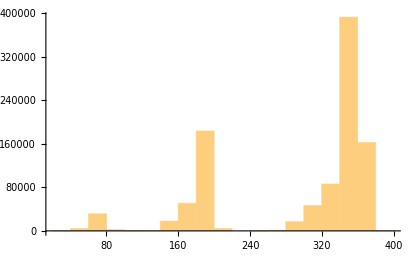

381

45

```mathematica
StringSplit/@TrainSet$ON$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data0_valid.txt",TrainSet$ON$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data0_test.txt",TrainSet$ON$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data0_train.txt",TrainSet$ON$format3⟦3129;;1000000⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data0_valid.txt

../../dataset_storage/on_the_paper/dataset/data0_test.txt

../../dataset_storage/on_the_paper/dataset/data0_train.txt

#### evaluation

```mathematica
result=EvaluateSimplificationResult["./Evaluation/exp0/data0_test.txt","./Evaluation/exp0/exp0_predictions.txt",False,True];
```

```mathematica
result
```

{0.,0.665333,0.334667}

```mathematica
?EvaluateSimplificationResult
```

```mathematica
?PolySimplifyWithHint
```

```mathematica
?PolynomialDecomposite
```

```mathematica
?PolynomialReduce
```

```mathematica
PolynomialDecomposite[-3-5 a[3] a[9]-200 a[3]^2 a[9]^2-5 a[4] a[10]-400 a[3] a[4] a[9] a[10]-200 a[4]^2 a[10]^2-a[5] a[11]-80 a[3] a[5] a[9] a[11]-80 a[4] a[5] a[10] a[11]-8 a[5]^2 a[11]^2-a[6] a[12]-80 a[3] a[6] a[9] a[12]-80 a[4] a[6] a[10] a[12]-16 a[5] a[6] a[11] a[12]-8 a[6]^2 a[12]^2,-5 (a[3] a[9]+a[4] a[10])-a[5] a[11]-a[6] a[12]]
```

-3+(1-8 s) s

```mathematica
GenerateTrainSet$ON$CommonSet[1]
```

{{-3-5 a[3] a[9]-200 a[3]^2 a[9]^2-5 a[4] a[10]-400 a[3] a[4] a[9] a[10]-200 a[4]^2 a[10]^2-a[5] a[11]-80 a[3] a[5] a[9] a[11]-80 a[4] a[5] a[10] a[11]-8 a[5]^2 a[11]^2-a[6] a[12]-80 a[3] a[6] a[9] a[12]-80 a[4] a[6] a[10] a[12]-16 a[5] a[6] a[11] a[12]-8 a[6]^2 a[12]^2,-3+s-8 s^2,-5 (a[3] a[9]+a[4] a[10])-a[5] a[11]-a[6] a[12]}}

### produce training set

```mathematica
Get["MMA2TxtFormat1.m"];
```

```mathematica
GenerateTrainingSet$Format1[]:=Module[
{long,short,sub},
{long,short,sub}=RandomPolynomial$PolyNInPoly1$LSS[4,3,2,2,Table[a[i],{i,2}],ComplexityCriteria];

MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
];
GenerateTrainingSet$Format1[n_]:=Table[GenerateTrainingSet$Format1[],n];
```

```mathematica
trainingdata=GenerateTrainingSet$Format1[3]
```

{+ P 2 + * P 3 ^ a2 P 2 + * P 6 * a1 ^ a2 P 2 + * P 3 * ^ a1 P 2 ^ a2 P 2 + ^ a2 P 3 + * P 3 * a1 ^ a2 P 3 + * P 3 * ^ a1 P 2 ^ a2 P 3 * ^ a1 P 3 ^ a2 P 3 ? + a2 * a1 a2,+ P 35 + * P 51 a1 + * P 24 ^ a1 P 2 + * P 4 ^ a1 P 3 + * N 102 a2 + * N 45 * a1 a2 + * P 24 * ^ a1 P 2 a2 + * P 12 * ^ a1 P 3 a2 + * P 96 ^ a2 P 2 + * N 48 * a1 ^ a2 P 2 + * N 24 * ^ a1 P 2 ^ a2 P 2 + * P 12 * ^ a1 P 3 ^ a2 P 2 + * N 32 ^ a2 P 3 + * P 48 * a1 ^ a2 P 3 + * N 24 * ^ a1 P 2 ^ a2 P 3 * P 4 * ^ a1 P 3 ^ a2 P 3 ? + P 2 + a1 + * N 2 a2 * a1 a2,+ P 2 + * N 5 a2 + * N 10 * a1 a2 + * N 4 ^ a2 P 2 + * N 16 * a1 ^ a2 P 2 * N 16 * ^ a1 P 2 ^ a2 P 2 ? + N 1 + * N 1 a2 * N 2 * a1 a2}

```mathematica
Export["train_set.txt",trainingdata,"Text"]
```

train_set.txt

```mathematica
"train_set.txt"//LongSubPair$FromFile
```

{{2+3 a[2]^2+6 a[1] a[2]^2+3 a[1]^2 a[2]^2+a[2]^3+3 a[1] a[2]^3+3 a[1]^2 a[2]^3+a[1]^3 a[2]^3,a[2]+a[1] a[2]},{35+51 a[1]+24 a[1]^2+4 a[1]^3-102 a[2]-45 a[1] a[2]+24 a[1]^2 a[2]+12 a[1]^3 a[2]+96 a[2]^2-48 a[1] a[2]^2-24 a[1]^2 a[2]^2+12 a[1]^3 a[2]^2-32 a[2]^3+48 a[1] a[2]^3-24 a[1]^2 a[2]^3+4 a[1]^3 a[2]^3,2+a[1]-2 a[2]+a[1] a[2]},{2-5 a[2]-10 a[1] a[2]-4 a[2]^2-16 a[1] a[2]^2-16 a[1]^2 a[2]^2,-1-a[2]-2 a[1] a[2]}}

### 5 2 20 4 training set without complexity criteria(Exp14,32,33,...)

#### benchmark CommonSet without constraint

```mathematica
GenerateTrainSet$52204$wocriteria$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet=GenerateTrainSet$52204$wocriteria$CommonSet[3000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$wocriteria$CommonSet=DeleteDuplicates[TrainSet$52204$wocriteria$CommonSet];
Length[TrainSet$52204$wocriteria$CommonSet]
```

3000

```mathematica
TrainSet$52204$wocriteria$CommonSet⟦2⟧
```

{153-560 a[1]+1107 a[1]^2-1193 a[1]^3+245 a[1]^4+756 a[1]^5-1002 a[1]^6+180 a[1]^7+450 a[1]^8,1-3 s+2 s^2,-8+16 a[1]-17 a[1]^2+3 a[1]^3+15 a[1]^4}

#### benchmark CommonSet without constraint in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$wocriteria$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$wocriteria$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet$format3=GenerateTrainSet$52204$wocriteria$CommonSet$format3[Length[TrainSet$52204$wocriteria$CommonSet]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet$format3⟦1;;2⟧
```

{+ N 1 3 + * N 7 6 a1 + * N 4 8 ^ a1 P 2 + * N 8 0 ^ a1 P 3 * P 3 2 ^ a1 P 4 ? + N 3 + * N 1 9 a1 + * N 1 2 ^ a1 P 2 + * N 2 0 ^ a1 P 3 * P 8 ^ a1 P 4,+ P 1 5 3 + * N 5 6 0 a1 + * P 1 1 0 7 ^ a1 P 2 + * N 1 1 9 3 ^ a1 P 3 + * P 2 4 5 ^ a1 P 4 + * P 7 5 6 ^ a1 P 5 + * N 1 0 0 2 ^ a1 P 6 + * P 1 8 0 ^ a1 P 7 * P 4 5 0 ^ a1 P 8 ? + N 8 + * P 1 6 a1 + * N 1 7 ^ a1 P 2 + * P 3 ^ a1 P 3 * P 1 5 ^ a1 P 4}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
(*Export["../../dataset_storage/Exp34/valid_set_Exp34.txt",TrainSet$52204$wocriteria$CommonSet$format3⟦1;;128⟧,"Text"]*)
Export["../../dataset_storage/gen3/benchmark.txt",TrainSet$52204$wocriteria$CommonSet$format3⟦1;;3000⟧,"Text"]
(*Export["../../dataset_storage/Exp34/train_set_Exp34.txt",TrainSet$52204$wocriteria$CommonSet$format3⟦3129;;1003128⟧,"Text"]*)
```

../../dataset_storage/gen3/benchmark.txt

#### Generalization test3 on Exp33 ( without constraint, original coefficient out of scope : 6 - 10)

```mathematica
GenerateExp33$Gen3$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[6,10,2,0,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen3$CommonSet[2]
```

{{8-260 a[1]^2+800 a[1]^4,-10+10 s+8 s^2,1-10 a[1]^2},{-8+112 a[1]+2132 a[1]^2+3142 a[1]^3+3712 a[1]^4+1920 a[1]^5+800 a[1]^6,-8+7 s+8 s^2,16 a[1]+12 a[1]^2+10 a[1]^3}}

```mathematica
Exp33$Gen3$CommonSet=GenerateExp33$Gen3$CommonSet[3000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen3$CommonSet=DeleteDuplicates[Exp33$Gen3$CommonSet];
Length[Exp33$Gen3$CommonSet]
```

3000

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen3$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen3$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen3$format3=GenerateExp33$Gen3$format3[Length[Exp33$Gen3$CommonSet]];
```

```mathematica
Exp33$Gen3$format3⟦1;;2⟧
```

{+ N 1 3 3 + * N 1 1 3 4 a1 + * N 1 3 2 3 ^ a1 P 2 + * P 3 4 6 5 ^ a1 P 3 + * N 2 8 3 5 ^ a1 P 4 + * P 1 0 5 0 ^ a1 P 5 * N 1 7 5 ^ a1 P 6 ? + N 5 + * N 1 8 a1 + * P 1 5 ^ a1 P 2 * N 5 ^ a1 P 3,+ P 1 3 7 5 + * P 3 3 3 0 a1 + * P 2 2 4 7 ^ a1 P 2 + * N 2 3 9 4 ^ a1 P 3 + * N 7 6 7 1 ^ a1 P 4 + * N 5 6 1 6 ^ a1 P 5 + * P 9 3 6 ^ a1 P 6 + * P 4 3 2 0 ^ a1 P 7 * P 3 6 0 0 ^ a1 P 8 ? + P 1 2 + * P 1 5 a1 + ^ a1 P 2 + * N 1 2 ^ a1 P 3 * N 2 0 ^ a1 P 4}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/gen3/gen3_test.txt",Exp33$Gen3$format3⟦1;;3000⟧,"Text"]
```

../../dataset_storage/gen3/gen3_test.txt

#### Generalization test4 on Exp33 ( without constraint, sub coefficient out of scope : 21 - 30)

```mathematica
GenerateExp33$Gen4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[0,5,2,21,30,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen4$CommonSet[2]
```

{{2859-5258 a[1]+7439 a[1]^2-4620 a[1]^3+2205 a[1]^4,3-s+5 s^2,24-22 a[1]+21 a[1]^2},{-1386+3741 a[1]+186 a[1]^2-3654 a[1]^3-1323 a[1]^4,-3 s-3 s^2,-22+29 a[1]+21 a[1]^2}}

```mathematica
Exp33$Gen4$CommonSet=GenerateExp33$Gen4$CommonSet[3000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen4$CommonSet=DeleteDuplicates[Exp33$Gen4$CommonSet];
Length[Exp33$Gen4$CommonSet]
```

3000

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen4$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen4$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen4$format3=GenerateExp33$Gen4$format3[Length[Exp33$Gen4$CommonSet]];
```

```mathematica
Exp33$Gen4$format3⟦1;;2⟧
```

{+ P 2 4 3 6 + * N 4 9 5 9 a1 + * N 2 0 9 4 ^ a1 P 2 + * P 4 6 9 8 ^ a1 P 3 * P 2 1 8 7 ^ a1 P 4 ? + P 2 8 + * N 2 9 a1 * N 2 7 ^ a1 P 2,+ P 3 6 4 1 + * P 6 4 8 0 a1 + * P 1 0 1 7 0 ^ a1 P 2 + * P 1 3 7 7 0 ^ a1 P 3 + * P 3 1 0 5 ^ a1 P 4 + * P 1 0 5 0 ^ a1 P 5 + * N 3 3 7 5 ^ a1 P 6 + * N 7 0 2 0 ^ a1 P 7 * P 3 3 8 0 ^ a1 P 8 ? + N 2 7 + * N 2 4 a1 + * N 2 7 ^ a1 P 2 + * N 2 7 ^ a1 P 3 * P 2 6 ^ a1 P 4}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/gen4/gen4_test.txt",Exp33$Gen4$format3⟦1;;3000⟧,"Text"]
```

../../dataset_storage/gen4/gen4_test.txt

#### real benchmark CommonSet

```mathematica
GenerateTrainSet$52204$wocriteria$CommonSet1[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1=GenerateTrainSet$52204$wocriteria$CommonSet1[3500];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1=DeleteDuplicates[TrainSet$52204$wocriteria$CommonSet1];
Length[TrainSet$52204$wocriteria$CommonSet1]
```

3419

```mathematica
TrainSet$52204$wocriteria$CommonSet1⟦8⟧
```

{-66+17 a[1]-a[1]^2-17 a[1]^3+2 a[1]^4-a[1]^6,-5 s-s^2,6-a[1]+a[1]^3}

#### real benchmark CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$wocriteria$CommonSet1$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$wocriteria$CommonSet1⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1$format3=GenerateTrainSet$52204$wocriteria$CommonSet1$format3[Length[TrainSet$52204$wocriteria$CommonSet1]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1$format3⟦1;;2⟧
```

{+ P 1 4 2 5 + * N 3 0 2 0 a1 + * N 6 6 5 ^ a1 P 2 + * P 2 2 4 9 ^ a1 P 3 + * P 1 0 6 0 ^ a1 P 4 + * P 1 2 0 ^ a1 P 5 * P 4 ^ a1 P 6 ? + N 1 9 + * P 2 0 a1 + * P 1 5 ^ a1 P 2 ^ a1 P 3,+ N 1 2 6 + * P 4 6 8 a1 + * N 1 0 9 5 ^ a1 P 2 + * P 1 1 8 5 ^ a1 P 3 + * N 7 9 5 ^ a1 P 4 + * N 1 0 2 ^ a1 P 5 * N 3 ^ a1 P 6 ? + P 6 + * N 1 2 a1 + * P 1 7 ^ a1 P 2 ^ a1 P 3}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
(*Export["../../dataset_storage/Exp34/valid_set_Exp34.txt",TrainSet$52204$wocriteria$CommonSet$format3⟦1;;128⟧,"Text"]*)
Export["../../dataset_storage/gen3/real_benchmark.txt",TrainSet$52204$wocriteria$CommonSet1$format3⟦1;;3000⟧,"Text"]
(*Export["../../dataset_storage/Exp34/train_set_Exp34.txt",TrainSet$52204$wocriteria$CommonSet$format3⟦3129;;1003128⟧,"Text"]*)
```

../../dataset_storage/gen3/real_benchmark.txt

#### Generalization test5 on Exp33 ( without constraint, original coefficient out of scope : 6 - 10)

```mathematica
GenerateExp33$Gen5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[6,10,2,0,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen5$CommonSet[2]
```

{{120 a[1]+3994 a[1]^2-400 a[1]^3+10 a[1]^4,-6 s+10 s^2,-20 a[1]+a[1]^2},{-1044+366 a[1]^2+732 a[1]^3-215 a[1]^4-128 a[1]^5-96 a[1]^6+64 a[1]^7-8 a[1]^8,9 s-8 s^2,12-2 a[1]^2-4 a[1]^3+a[1]^4}}

```mathematica
Exp33$Gen5$CommonSet=GenerateExp33$Gen5$CommonSet[1000000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen5$CommonSet=DeleteDuplicates[Exp33$Gen5$CommonSet];
Length[Exp33$Gen5$CommonSet]
```

628218

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen5$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen5$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen5$format3=GenerateExp33$Gen5$format3[Length[Exp33$Gen5$CommonSet]];
```

```mathematica
Exp33$Gen5$format3⟦1;;2⟧
```

{+ P 3 0 0 0 + * P 2 9 0 a1 * P 7 ^ a1 P 2 ? + P 2 0 a1,+ P 5 1 3 + * P 1 3 2 0 ^ a1 P 2 + * N 8 4 0 ^ a1 P 3 + * P 7 2 7 ^ a1 P 4 + * N 1 0 7 8 ^ a1 P 5 + * P 1 8 9 ^ a1 P 6 + * P 9 8 ^ a1 P 7 * P 7 ^ a1 P 8 ? + N 9 + * N 1 1 ^ a1 P 2 + * P 7 ^ a1 P 3 ^ a1 P 4}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/gen5/gen5_big_test.txt",Exp33$Gen5$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_big_valid.txt",Exp33$Gen5$format3⟦3001;;3128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_train1.txt",Exp33$Gen5$format3⟦3129;;103128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_train2.txt",Exp33$Gen5$format3⟦103129;;203128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_train3.txt",Exp33$Gen5$format3⟦203129;;303128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_train4.txt",Exp33$Gen5$format3⟦303129;;403128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_train5.txt",Exp33$Gen5$format3⟦403129;;503128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_tiny_train.txt",Exp33$Gen5$format3⟦3129;;13368⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_small_train.txt",Exp33$Gen5$format3⟦3129;;28128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_middle_train.txt",Exp33$Gen5$format3⟦3129;;53128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_big_train.txt",Exp33$Gen5$format3⟦3129;;253128⟧,"Text"]
Export["../../dataset_storage/gen5/gen5_bigbig_train.txt",Exp33$Gen5$format3⟦3129;;503128⟧,"Text"]
```

../../dataset_storage/gen5/gen5_big_test.txt

../../dataset_storage/gen5/gen5_big_valid.txt

../../dataset_storage/gen5/gen5_train1.txt

../../dataset_storage/gen5/gen5_train2.txt

../../dataset_storage/gen5/gen5_train3.txt

../../dataset_storage/gen5/gen5_train4.txt

../../dataset_storage/gen5/gen5_train5.txt

../../dataset_storage/gen5/gen5_tiny_train.txt

../../dataset_storage/gen5/gen5_small_train.txt

../../dataset_storage/gen5/gen5_middle_train.txt

../../dataset_storage/gen5/gen5_big_train.txt

../../dataset_storage/gen5/gen5_bigbig_train.txt

#### Generalization test6 on Exp33 ( without constraint, sub coefficient out of scope : 21 - 30)

```mathematica
GenerateExp33$Gen6$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[0,5,2,21,30,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen6$CommonSet[2]
```

{{2808-212 a[1]+4 a[1]^2,4 s+4 s^2,-27+a[1]},{-2116-184 a[1]-4 a[1]^2,-4 s^2,23+a[1]}}

```mathematica
Exp33$Gen6$CommonSet=GenerateExp33$Gen6$CommonSet[1000000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen6$CommonSet=DeleteDuplicates[Exp33$Gen6$CommonSet];
Length[Exp33$Gen6$CommonSet]
```

526963

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen6$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen6$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen6$format3=GenerateExp33$Gen6$format3[Length[Exp33$Gen6$CommonSet]];
```

```mathematica
Exp33$Gen6$format3⟦1;;3⟧
```

{+ P 1 1 5 0 + * N 2 1 1 2 a1 + * N 1 8 1 6 ^ a1 P 2 + * P 2 4 5 6 ^ a1 P 3 + * P 1 7 7 0 ^ a1 P 4 + * P 1 1 6 ^ a1 P 5 * P 2 ^ a1 P 6 ? + N 2 5 + * P 2 2 a1 + * P 2 9 ^ a1 P 2 ^ a1 P 3,+ N 1 0 5 6 + * P 2 2 0 8 a1 + * P 1 2 4 0 ^ a1 P 2 + * N 2 5 8 8 ^ a1 P 3 + * N 1 2 5 6 ^ a1 P 4 + * P 1 0 4 ^ a1 P 5 * N 2 ^ a1 P 6 ? + P 2 2 + * N 2 4 a1 + * N 2 6 ^ a1 P 2 ^ a1 P 3,+ P 2 0 5 2 + * P 1 5 7 a1 * P 3 ^ a1 P 2 ? + P 2 7 a1}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/gen6/gen6_big_test.txt",Exp33$Gen6$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_big_valid.txt",Exp33$Gen6$format3⟦3001;;3128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train1.txt",Exp33$Gen6$format3⟦3129;;103128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train2.txt",Exp33$Gen6$format3⟦103129;;203128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train3.txt",Exp33$Gen6$format3⟦203129;;303128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train4.txt",Exp33$Gen6$format3⟦303129;;403128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train5.txt",Exp33$Gen6$format3⟦403129;;503128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_tiny_train.txt",Exp33$Gen6$format3⟦3129;;13368⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_small_train.txt",Exp33$Gen6$format3⟦3129;;28128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_middle_train.txt",Exp33$Gen6$format3⟦3129;;53128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_big_train.txt",Exp33$Gen6$format3⟦3129;;253128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_bigbig_train.txt",Exp33$Gen6$format3⟦3129;;503128⟧,"Text"]
```

../../dataset_storage/gen6/gen6_big_test.txt

../../dataset_storage/gen6/gen6_big_valid.txt

../../dataset_storage/gen6/gen6_train1.txt

../../dataset_storage/gen6/gen6_train2.txt

../../dataset_storage/gen6/gen6_train3.txt

../../dataset_storage/gen6/gen6_train4.txt

../../dataset_storage/gen6/gen6_train5.txt

../../dataset_storage/gen6/gen6_tiny_train.txt

../../dataset_storage/gen6/gen6_small_train.txt

../../dataset_storage/gen6/gen6_middle_train.txt

../../dataset_storage/gen6/gen6_big_train.txt

../../dataset_storage/gen6/gen6_bigbig_train.txt

#### dataset with a different variable, CommonSet ( a[1] -> a[5] )

```mathematica
GenerateTrainSet$52204$wocriteria$CommonSet2[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[5,2,20,4,{a[5]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet2=GenerateTrainSet$52204$wocriteria$CommonSet2[2100000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$wocriteria$CommonSet2=DeleteDuplicates[TrainSet$52204$wocriteria$CommonSet2];
Length[TrainSet$52204$wocriteria$CommonSet2]
```

1218021

```mathematica
TrainSet$52204$wocriteria$CommonSet2⟦5⟧
```

{-50-275 a[5]+87 a[5]^2+1163 a[5]^3-1038 a[5]^4+108 a[5]^5-3 a[5]^6,5 s-3 s^2,5+11 a[5]-18 a[5]^2+a[5]^3}

#### dataset with a different variable in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$wocriteria$CommonSet2$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$wocriteria$CommonSet2⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet2$format3=GenerateTrainSet$52204$wocriteria$CommonSet2$format3[Length[TrainSet$52204$wocriteria$CommonSet2]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet2$format3⟦1;;2⟧
```

{+ P 1 2 + * N 2 0 a5 + * N 1 4 2 ^ a5 P 2 + * P 1 1 0 ^ a5 P 3 + * P 4 5 8 ^ a5 P 4 + * P 6 0 ^ a5 P 5 * P 2 ^ a5 P 6 ? + N 3 + * P 2 a5 + * P 1 5 ^ a5 P 2 ^ a5 P 3,+ N 5 + * N 6 a5 * N 1 ^ a5 P 2 ? + P 5 a5}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/newvar/valid_set_newvar1.txt",TrainSet$52204$wocriteria$CommonSet2$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/newvar/test_set_newvar1.txt",TrainSet$52204$wocriteria$CommonSet2$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/newvar/train_set_newvar1.txt",TrainSet$52204$wocriteria$CommonSet2$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/newvar/valid_set_newvar1.txt

../../dataset_storage/newvar/test_set_newvar1.txt

../../dataset_storage/newvar/train_set_newvar1.txt

### 5 2 20 4 training set with complexity criteria(Exp34)

#### CommonSet

```mathematica
GenerateTrainSet$52204$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[5,2,20,4,{a[1]},ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52204$CommonSet=GenerateTrainSet$52204$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$CommonSet=DeleteDuplicates[TrainSet$52204$CommonSet];
Length[TrainSet$52204$CommonSet]
```

1299216

#### CommonSet in a format 1

```mathematica
Get["MMA2TxtFormat1.m"];
GenerateTrainSet$52204$CommonSet$format1[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$CommonSet$format1=GenerateTrainSet$52204$CommonSet$format1[Length[TrainSet$52204$CommonSet]]
```

#### CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$CommonSet$format3=GenerateTrainSet$52204$CommonSet$format3[Length[TrainSet$52204$CommonSet]];
```

```mathematica
TrainSet$52204$CommonSet$format3⟦1;;2⟧
```

{+ N 4 3 6 + * P 1 2 6 ^ a1 P 2 + * P 5 0 4 ^ a1 P 3 + * N 9 ^ a1 P 4 + * N 7 2 ^ a1 P 5 * N 1 4 4 ^ a1 P 6 ? + N 2 0 + * P 3 ^ a1 P 2 * P 1 2 ^ a1 P 3,+ N 1 6 0 3 + * P 1 7 9 0 a1 + * N 3 2 1 ^ a1 P 2 + * N 8 1 6 ^ a1 P 3 + * P 3 7 9 6 ^ a1 P 4 + * N 1 8 6 0 ^ a1 P 5 + * N 2 7 0 ^ a1 P 6 + * P 7 6 0 ^ a1 P 7 * N 1 8 0 5 ^ a1 P 8 ? + N 1 8 + * P 1 0 a1 + ^ a1 P 2 + * N 4 ^ a1 P 3 * P 1 9 ^ a1 P 4}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp34/valid_set_Exp34.txt",TrainSet$52204$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp34/test_set_Exp34.txt",TrainSet$52204$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp34/train_set_Exp34.txt",TrainSet$52204$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp34/valid_set_Exp34.txt

../../dataset_storage/Exp34/test_set_Exp34.txt

../../dataset_storage/Exp34/train_set_Exp34.txt

### 5 2 20 4 training set with complexity criteria with constraint no constant term for original, coefficient of highest degree term of sub 1

#### CommonSet

```mathematica
GenerateTrainSet$52204$constraint$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[5,2,20,4,{a[1]},ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52204$constraint$CommonSet=GenerateTrainSet$52204$constraint$CommonSet[1400000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$constraint$CommonSet=DeleteDuplicates[TrainSet$52204$constraint$CommonSet];
Length[TrainSet$52204$constraint$CommonSet]
```

1066470

#### CommonSet in a format 1

```mathematica
Get["MMA2TxtFormat1.m"];
GenerateTrainSet$52204$constraint$CommonSet$format1[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$constraint$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$constraint$CommonSet$format1=GenerateTrainSet$52204$constraint$CommonSet$format1[Length[TrainSet$52204$constraint$CommonSet]];
```

#### CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$constraint$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$constraint$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$constraint$CommonSet$format3=GenerateTrainSet$52204$constraint$CommonSet$format3[Length[TrainSet$52204$constraint$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp36/valid_set_Exp36.txt",TrainSet$52204$constraint$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp36/test_set_Exp36.txt",TrainSet$52204$constraint$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp36/train_set_Exp36.txt",TrainSet$52204$constraint$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp36/valid_set_Exp36.txt

../../dataset_storage/Exp36/test_set_Exp36.txt

../../dataset_storage/Exp36/train_set_Exp36.txt

### 5 2 10 2 training set with complexity criteria, with constraints

#### CommonSet

```mathematica
GenerateTrainSet$52102$two$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[5,2,10,2,{a[1],a[2],a[3]},ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$52102$two$CommonSet=GenerateTrainSet$52102$two$CommonSet[1];
%⟦1,1⟧
%%⟦1,2⟧
%%%⟦1,3⟧
```

-140+371 a[1]+126 a[1]^2-490 a[1]^3-245 a[1]^4-318 a[2]+367 a[1] a[2]+437 a[1]^2 a[2]+140 a[1]^3 a[2]+70 a[1]^4 a[2]+138 a[2]^2-1010 a[1] a[2]^2-262 a[1]^2 a[2]^2+1320 a[1]^3 a[2]^2+625 a[1]^4 a[2]^2+360 a[2]^3-540 a[1] a[2]^3-580 a[1]^2 a[2]^3-190 a[1]^3 a[2]^3-90 a[1]^4 a[2]^3-180 a[2]^4+600 a[1] a[2]^4+40 a[1]^2 a[2]^4-900 a[1]^3 a[2]^4-405 a[1]^4 a[2]^4-212 a[3]+810 a[1] a[3]-155 a[1]^2 a[3]-1050 a[1]^3 a[3]-350 a[1]^4 a[3]-293 a[2] a[3]+630 a[1] a[2] a[3]+642 a[1]^2 a[2] a[3]-130 a[1]^3 a[2] a[3]-230 a[1]^4 a[2] a[3]+74 a[2]^2 a[3]-1082 a[1] a[2]^2 a[3]+566 a[1]^2 a[2]^2 a[3]+2280 a[1]^3 a[2]^2 a[3]+1050 a[1]^4 a[2]^2 a[3]-60 a[2]^3 a[3]-360 a[1] a[2]^3 a[3]-870 a[1]^2 a[2]^3 a[3]+280 a[1]^3 a[2]^3 a[3]+280 a[1]^4 a[2]^3 a[3]+120 a[2]^4 a[3]+40 a[1] a[2]^4 a[3]-100 a[1]^2 a[2]^4 a[3]-1160 a[1]^3 a[2]^4 a[3]-720 a[1]^4 a[2]^4 a[3]-27 a[3]^2+701 a[1] a[3]^2-330 a[1]^2 a[3]^2-1690 a[1]^3 a[3]^2-825 a[1]^4 a[3]^2-351 a[2] a[3]^2+490 a[1] a[2] a[3]^2+2345 a[1]^2 a[2] a[3]^2+120 a[1]^3 a[2] a[3]^2-450 a[1]^4 a[2] a[3]^2-618 a[2]^2 a[3]^2-1251 a[1] a[2]^2 a[3]^2+1153 a[1]^2 a[2]^2 a[3]^2+3000 a[1]^3 a[2]^2 a[3]^2+1200 a[1]^4 a[2]^2 a[3]^2+340 a[2]^3 a[3]^2-570 a[1] a[2]^3 a[3]^2-1950 a[1]^2 a[2]^3 a[3]^2-300 a[1]^3 a[2]^3 a[3]^2+780 a[1]^4 a[2]^3 a[3]^2+40 a[2]^4 a[3]^2+240 a[1] a[2]^4 a[3]^2-1090 a[1]^2 a[2]^4 a[3]^2-850 a[1]^3 a[2]^4 a[3]^2-230 a[1]^4 a[2]^4 a[3]^2+40 a[3]^3+180 a[1] a[3]^3-350 a[1]^2 a[3]^3-1350 a[1]^3 a[3]^3-500 a[1]^4 a[3]^3-270 a[2] a[3]^3+370 a[1] a[2] a[3]^3+1610 a[1]^2 a[2] a[3]^3-280 a[1]^3 a[2] a[3]^3-650 a[1]^4 a[2] a[3]^3-90 a[2]^2 a[3]^3-100 a[1] a[2]^2 a[3]^3+1680 a[1]^2 a[2]^2 a[3]^3+1610 a[1]^3 a[2]^2 a[3]^3+550 a[1]^4 a[2]^2 a[3]^3-150 a[2]^3 a[3]^3-550 a[1] a[2]^3 a[3]^3-810 a[1]^2 a[2]^3 a[3]^3-320 a[1]^3 a[2]^3 a[3]^3+360 a[1]^4 a[2]^3 a[3]^3-20 a[2]^4 a[3]^3-180 a[1] a[2]^4 a[3]^3-340 a[1]^2 a[2]^4 a[3]^3-520 a[1]^3 a[2]^4 a[3]^3+80 a[1]^4 a[2]^4 a[3]^3-5 a[3]^4-70 a[1] a[3]^4-345 a[1]^2 a[3]^4-700 a[1]^3 a[3]^4-500 a[1]^4 a[3]^4+70 a[2] a[3]^4+590 a[1] a[2] a[3]^4+1350 a[1]^2 a[2] a[3]^4+650 a[1]^3 a[2] a[3]^4-500 a[1]^4 a[2] a[3]^4-235 a[2]^2 a[3]^4-560 a[1] a[2]^2 a[3]^4+430 a[1]^2 a[2]^2 a[3]^4+1130 a[1]^3 a[2]^2 a[3]^4-225 a[1]^4 a[2]^2 a[3]^4-70 a[2]^3 a[3]^4-590 a[1] a[2]^3 a[3]^4-580 a[1]^2 a[2]^3 a[3]^4+450 a[1]^3 a[2]^3 a[3]^4-50 a[1]^4 a[2]^3 a[3]^4-5 a[2]^4 a[3]^4-70 a[1] a[2]^4 a[3]^4-235 a[1]^2 a[2]^4 a[3]^4+70 a[1]^3 a[2]^4 a[3]^4-5 a[1]^4 a[2]^4 a[3]^4

3 s-5 s^2

-5+7 a[1]+7 a[1]^2-6 a[2]-a[1] a[2]-a[1]^2 a[2]+6 a[2]^2-10 a[1] a[2]^2-9 a[1]^2 a[2]^2-4 a[3]+10 a[1] a[3]+5 a[1]^2 a[3]-a[2] a[3]+4 a[1]^2 a[2] a[3]-2 a[2]^2 a[3]-4 a[1] a[2]^2 a[3]-8 a[1]^2 a[2]^2 a[3]+a[3]^2+7 a[1] a[3]^2+10 a[1]^2 a[3]^2-7 a[2] a[3]^2-10 a[1] a[2] a[3]^2+5 a[1]^2 a[2] a[3]^2-a[2]^2 a[3]^2-7 a[1] a[2]^2 a[3]^2+a[1]^2 a[2]^2 a[3]^2

### 9 2 9 3 training set with complexity criteria, with constraints, three variables, maximum number of terms : 3

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

8 y z+3 y z^2

```mathematica
RandomPolynomial$PolyNInPoly3$LSS[9,2,9,3,{a[1],a[2],a[3]},3,ComplexityCriteria]
```

{5-24 a[3]-30 a[1] a[2] a[3]+4 a[3]^2+40 a[1] a[2] a[3]^2+25 a[1]^2 a[2]^2 a[3]^2+16 a[3]^3+20 a[1] a[2] a[3]^3+4 a[3]^4,5-6 s+s^2,4 a[3]+5 a[1] a[2] a[3]+2 a[3]^2}

#### CommonSet

```mathematica
GenerateTrainSet$9293$three$6$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly3$LSS[9,2,9,3,{a[1],a[2],a[3]},3,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$9293$three$6$CommonSet=GenerateTrainSet$9293$three$6$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$9293$three$6$CommonSet=DeleteDuplicates[TrainSet$9293$three$6$CommonSet];
Length[TrainSet$9293$three$6$CommonSet]
```

1060370

#### CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$9293$three$6$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$9293$three$6$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$9293$three$6$CommonSet$format3=GenerateTrainSet$9293$three$6$CommonSet$format3[Length[TrainSet$9293$three$6$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp41/valid_set_Exp41.txt",TrainSet$9293$three$6$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp41/test_set_Exp41.txt",TrainSet$9293$three$6$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp41/train_set_Exp41.txt",TrainSet$9293$three$6$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp41/valid_set_Exp41.txt

../../dataset_storage/Exp41/test_set_Exp41.txt

../../dataset_storage/Exp41/train_set_Exp41.txt

#### CommonSet in a format 3 with short (Exp44)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$9293$three$6$CommonSet$format3$wshort[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$9293$three$6$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]<>" $ "<>MMAExprToJFString[short/.s->b0]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$9293$three$6$CommonSet$format3$wshort=GenerateTrainSet$9293$three$6$CommonSet$format3$wshort[Length[TrainSet$9293$three$6$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp44/valid_set_Exp44.txt",TrainSet$9293$three$6$CommonSet$format3$wshort⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp44/test_set_Exp44.txt",TrainSet$9293$three$6$CommonSet$format3$wshort⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp44/train_set_Exp44.txt",TrainSet$9293$three$6$CommonSet$format3$wshort⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp44/valid_set_Exp44.txt

../../dataset_storage/Exp44/test_set_Exp44.txt

../../dataset_storage/Exp44/train_set_Exp44.txt

### 5 3 6 3 training set with complexity criteria, with constraints, three variables, maximum number of terms : 4

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

8 y z+3 y z^2

```mathematica
RandomPolynomial$PolyNInPoly3$LSS[5,3,6,3,{a[1],a[2],a[3]},4,ComplexityCriteria]
```

{-3+5 a[1] a[3]+20 a[1] a[2] a[3]-10 a[2]^2 a[3]+2 a[1]^2 a[3]^2+16 a[1]^2 a[2] a[3]^2-8 a[1] a[2]^2 a[3]^2+32 a[1]^2 a[2]^2 a[3]^2-32 a[1] a[2]^3 a[3]^2+8 a[2]^4 a[3]^2-a[1]^3 a[3]^3-12 a[1]^3 a[2] a[3]^3+6 a[1]^2 a[2]^2 a[3]^3-48 a[1]^3 a[2]^2 a[3]^3+48 a[1]^2 a[2]^3 a[3]^3-64 a[1]^3 a[2]^3 a[3]^3-12 a[1] a[2]^4 a[3]^3+96 a[1]^2 a[2]^4 a[3]^3-48 a[1] a[2]^5 a[3]^3+8 a[2]^6 a[3]^3,-3-5 s+2 s^2+s^3,-a[1] a[3]-4 a[1] a[2] a[3]+2 a[2]^2 a[3]}

#### CommonSet

```mathematica
GenerateTrainSet$5363$three$4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly3$LSS[5,3,6,3,{a[1],a[2],a[3]},4,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$5363$three$4$CommonSet=GenerateTrainSet$5363$three$4$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$5363$three$4$CommonSet=DeleteDuplicates[TrainSet$5363$three$4$CommonSet];
Length[TrainSet$5363$three$4$CommonSet]
```

1190076

#### CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5363$three$4$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$5363$three$4$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5363$three$4$CommonSet$format3=GenerateTrainSet$5363$three$4$CommonSet$format3[Length[TrainSet$5363$three$4$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp42/valid_set_Exp42.txt",TrainSet$5363$three$4$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp42/test_set_Exp42.txt",TrainSet$5363$three$4$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp42/train_set_Exp42.txt",TrainSet$5363$three$4$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp42/valid_set_Exp42.txt

../../dataset_storage/Exp42/test_set_Exp42.txt

../../dataset_storage/Exp42/train_set_Exp42.txt

### 5 3 6 3 training set with complexity criteria, with constraints, three variables, maximum number of terms : 3

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

8 y z+3 y z^2

```mathematica
RandomPolynomial$PolyNInPoly3$LSS[5,3,6,3,{a[1],a[2],a[3]},3,ComplexityCriteria]
```

{3-15 a[1]^3+25 a[1]^6+125 a[1]^9-9 a[2]+30 a[1]^3 a[2]+225 a[1]^6 a[2]+9 a[2]^2+135 a[1]^3 a[2]^2+33 a[2]^3-20 a[1]^3 a[2]^3-150 a[1]^6 a[2]^3-12 a[2]^4-180 a[1]^3 a[2]^4-54 a[2]^5+4 a[2]^6+60 a[1]^3 a[2]^6+36 a[2]^7-8 a[2]^9,3-3 s+s^2+s^3,5 a[1]^3+3 a[2]-2 a[2]^3}

#### CommonSet

```mathematica
GenerateTrainSet$5363$three$3$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly3$LSS[5,3,6,3,{a[1],a[2],a[3]},3,ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$5363$three$3$CommonSet=GenerateTrainSet$5363$three$3$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$5363$three$3$CommonSet=DeleteDuplicates[TrainSet$5363$three$3$CommonSet];
Length[TrainSet$5363$three$3$CommonSet]
```

1111329

#### CommonSet in a format 3

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5363$three$3$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$5363$three$3$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5363$three$3$CommonSet$format3=GenerateTrainSet$5363$three$3$CommonSet$format3[Length[TrainSet$5363$three$3$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp43/valid_set_Exp43.txt",TrainSet$5363$three$3$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp43/test_set_Exp43.txt",TrainSet$5363$three$3$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp43/train_set_Exp43.txt",TrainSet$5363$three$3$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp43/valid_set_Exp43.txt

../../dataset_storage/Exp43/test_set_Exp43.txt

../../dataset_storage/Exp43/train_set_Exp43.txt

### 5 2 ( 5 2, 5 2 ) training set with complexity criteria, with constraints, three variables, maximum number of terms : 3 (each) (Exp45)

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

8 y z+3 y z^2

```mathematica
RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,3]
```

{-6 a[1]-12 a[1]^2+48 a[1]^4-15 a[2]-6 a[1] a[3]-15 a[2] a[3]+120 a[1]^2 a[2] a[3]-15 a[3]^2+120 a[1]^2 a[3]^2+75 a[2]^2 a[3]^2+150 a[2] a[3]^3+75 a[3]^4,-3 b[0]+3 b[1]+3 b[1]^2,2 a[1]+5 a[2]+2 a[1] a[3],-4 a[1]^2-5 a[2] a[3]-5 a[3]^2}

```mathematica
RandomPolynomial$PolyNInPoly4$LSS[4,5,2,5,2,{a[1],a[2],a[3]},3,3]
RandomPolynomial$PolyNInPoly4$LSS[4,5,2,4,5,2,{a[1],a[2],a[3]},3,3]
RandomPolynomial$PolyNInPoly4$LSS[0,5,2,4,5,2,{a[1],a[2],a[3]},3,3]
```

{10 a[2]^2+8 a[3]-20 a[2]^2 a[3]+20 a[3]^2-40 a[3]^3,-4 b[0]+5 b[1]+5 b[0] b[1],-2 a[3],2 a[2]^2+4 a[3]^2}

{-20 a[1]-16 a[1]^2-100 a[1]^3+20 a[2]+125 a[1] a[2]-20 a[1] a[3]-100 a[1]^3 a[3]+125 a[1] a[2] a[3]+20 a[3]^2+125 a[1] a[3]^2+125 a[1] a[3]^3,4 b[0]-4 b[1]+5 b[0] b[1],-4 a[1]^2+5 a[2]+5 a[3]^2,5 a[1]+5 a[1] a[3]}

{8 a[1]^2+20 a[3]-8 a[2] a[3],2 b[0]+4 b[1],4 a[1]^2-4 a[2] a[3],5 a[3]}

```mathematica
?RandomPolynomial$PolyNInPoly4$LSS
```

#### CommonSet in a format 3 with short (Exp45)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$525252$three$3$CommonSet$format3$wshort[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$525252$three$3$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wshort=GenerateTrainSet$525252$three$3$CommonSet$format3$wshort[Length[TrainSet$525252$three$3$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp45/valid_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp45/test_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp45/train_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp45/valid_set_Exp45.txt

../../dataset_storage/Exp45/test_set_Exp45.txt

../../dataset_storage/Exp45/train_set_Exp45.txt

#### Generalization test 0 on Exp52, 53 ( test Exp45 data(non split) on Exp52,53 )

```mathematica
GenerateExp45$generalization0[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization0=GenerateExp45$generalization0[1500];
```

```mathematica
Exp45$generalization0=DeleteDuplicates[Exp45$generalization0];
Length[Exp45$generalization0]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization0$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization0⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization0$format3=GenerateExp45$generalization0$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen0/gen0_test_Exp45.txt",Exp45$generalization0$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen0/gen0_test_Exp45.txt

#### Generalization test 1 on Exp45 ( original coefficient out of scope : 6 - 10 )

```mathematica
GenerateExp45$generalization1[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[6,10,2,5,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization1=GenerateExp45$generalization1[1500];
```

```mathematica
Exp45$generalization1=DeleteDuplicates[Exp45$generalization1];
Length[Exp45$generalization1]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization1$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization1⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization1$format3=GenerateExp45$generalization1$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen1/gen1_test_Exp45.txt",Exp45$generalization1$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen1/gen1_test_Exp45.txt

#### Generalization test 2 on Exp45 ( sub coefficient out of scope : 6 - 8 )

```mathematica
GenerateExp45$generalization2[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[0,5,2,6,8,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization2=GenerateExp45$generalization2[1500];
```

```mathematica
Exp45$generalization2=DeleteDuplicates[Exp45$generalization2];
Length[Exp45$generalization2]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization2$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization2⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization2$format3=GenerateExp45$generalization2$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen2/gen2_test_Exp45.txt",Exp45$generalization2$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen2/gen2_test_Exp45.txt

#### train model in different training set (Exp 55-1, 55-2)

```mathematica
GenerateTrainSet$Exp55$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$Exp55$CommonSet=GenerateTrainSet$Exp55$CommonSet[2300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$Exp55$CommonSet=DeleteDuplicates[TrainSet$Exp55$CommonSet];
Length[TrainSet$Exp55$CommonSet]
```

2283884

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$Exp55$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$Exp55$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$Exp55$CommonSet$format3=GenerateTrainSet$Exp55$CommonSet$format3[Length[TrainSet$Exp55$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp55/valid_set_Exp55.txt",TrainSet$Exp55$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp55/test_set_Exp55.txt",TrainSet$Exp55$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp55/train_set_Exp55_1.txt",TrainSet$Exp55$CommonSet$format3⟦3129;;1003128⟧,"Text"]
Export["../../dataset_storage/Exp55/train_set_Exp55_2.txt",TrainSet$Exp55$CommonSet$format3⟦1003129;;2003128⟧,"Text"]
```

../../dataset_storage/Exp55/valid_set_Exp55.txt

../../dataset_storage/Exp55/test_set_Exp55.txt

../../dataset_storage/Exp55/train_set_Exp55_1.txt

../../dataset_storage/Exp55/train_set_Exp55_2.txt

#### further training the model with longer expressions (Exp 56)

```mathematica
GenerateTrainSet$Exp56$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,2,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$Exp56$CommonSet=GenerateTrainSet$Exp56$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$Exp56$CommonSet=DeleteDuplicates[TrainSet$Exp56$CommonSet];
Length[TrainSet$Exp56$CommonSet]
```

1299911

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$Exp56$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$Exp56$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$Exp56$CommonSet$format3=GenerateTrainSet$Exp56$CommonSet$format3[Length[TrainSet$Exp56$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp56/valid_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp56/test_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp56/train_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp56/valid_set_Exp56.txt

../../dataset_storage/Exp56/test_set_Exp56.txt

../../dataset_storage/Exp56/train_set_Exp56.txt

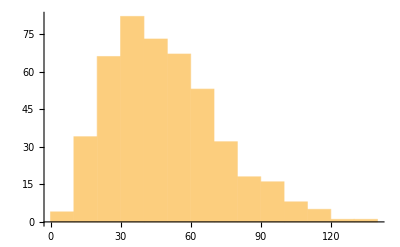

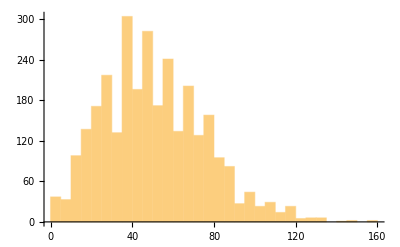

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdata$long=TestData$FromFile2["../../dataset_storage/Exp56/test_set_Exp56.txt"];
LeafCount/@testdata⟦hardcases⟧//Histogram
LeafCount/@testdata$long//Histogram
```

### 3 2 ( 3 2, 3 2 ) training set with complexity criteria, with constraints, two, four, four variables, maximum number of terms : 4 (each)

```mathematica
RandomPolynomial$maxlength$fix[3,2,{a,b,c,d},6]
```

a^2-3 a b-3 a c-b c-c d-2 d^2

```mathematica
RandomPolynomial$PolyNInPoly5$LSS[3,2,3,2,{a[1],a[2],a[3],a[4]},{a[5],a[6],a[7],a[8]},3,4]
```

{-4 a[1]^2 a[3]^2-18 a[5]^2 a[6]^2,-b[0]^2-2 b[1]^2,-2 a[1] a[3],3 a[5] a[6]}

#### CommonSet

```mathematica
GenerateTrainSet$Hirosi$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly5$LSS[3,2,3,2,{a[1],a[2],a[3],a[4]},{a[5],a[6],a[7],a[8]},3,4],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$Hirosi$CommonSet=GenerateTrainSet$Hirosi$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$Hirosi$CommonSet=DeleteDuplicates[TrainSet$Hirosi$CommonSet];
Length[TrainSet$Hirosi$CommonSet]
```

1291812

#### CommonSet in a format 3 with short (Exp50)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$Hirosi$CommonSet$format3$wshort[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$Hirosi$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$Hirosi$CommonSet$format3$wshort=GenerateTrainSet$Hirosi$CommonSet$format3$wshort[Length[TrainSet$Hirosi$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp50/valid_set_Exp50.txt",TrainSet$Hirosi$CommonSet$format3$wshort⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp50/test_set_Exp50.txt",TrainSet$Hirosi$CommonSet$format3$wshort⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp50/train_set_Exp50.txt",TrainSet$Hirosi$CommonSet$format3$wshort⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp50/valid_set_Exp50.txt

../../dataset_storage/Exp50/test_set_Exp50.txt

../../dataset_storage/Exp50/train_set_Exp50.txt

### Semiexpansion Experiment dataset form : Exp45

#### CommonSet in a format 3 with semiexpansion (simplification of subset of polynomial) (Exp 48)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSetWithSplit[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub1,sub2}=RandomPolynomialWithSplit$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]];
```

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wsplit=GenerateTrainSetWithSplit[600000]; (*600,000=>1,200,000 training cases*)
```

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wsplit=DeleteDuplicates[TrainSet$525252$three$3$CommonSet$format3$wsplit];
```

```mathematica
Export["../../dataset_storage/Exp48/valid_set_Exp48.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[1;;128]],"Text"]
Export["../../dataset_storage/Exp48/test_set_Exp48.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[129;;3128]],"Text"]
Export["../../dataset_storage/Exp48/train_set_Exp48.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[3129;;1003128]],"Text"]
```

#### CommonSet in a format 3 with semiexpansion (random split of coefficient/constant in polynomial (Jaeha’s suggestion) ) (Exp 52)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSetWithSplit[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub1,sub2}=RandomPolynomialWithSplit2$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]]
```

```mathematica
GenerateTrainSetWithSplit[1]
```

{+ * P 9 a0 + * N 1 ^ a0 P 2 * N 8 a1 ? a0 $ + * P 2 a0 * N 4 a1 & + * P 5 b0 + * N 1 ^ b0 P 2 * P 2 b1,+ * P 7 a0 + * P 2 a0 + N 0 + * N 1 ^ a0 P 2 + * N 4 a1 * N 4 a1 ? a0 $ + * P 2 a0 * N 4 a1 & + * P 5 b0 + * N 1 ^ b0 P 2 * P 2 b1}

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wsplit=GenerateTrainSetWithSplit[600000];
TrainSet$525252$three$3$CommonSet$format3$wsplit=DeleteDuplicates[TrainSet$525252$three$3$CommonSet$format3$wsplit];
```

```mathematica
Export["../../dataset_storage/Exp52/valid_set_Exp52.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[1;;128]],"Text"]
Export["../../dataset_storage/Exp52/test_set_Exp52.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[129;;3128]],"Text"]
Export["../../dataset_storage/Exp52/train_set_Exp52.txt",TrainSet$525252$three$3$CommonSet$format3$wsplit[[3129;;1003128]],"Text"]
```

../../dataset_storage/Exp52/valid_set_Exp52.txt

../../dataset_storage/Exp52/test_set_Exp52.txt

../../dataset_storage/Exp52/train_set_Exp52.txt

### Data with distribute without collection (2 variables sub & short) (Exp 58)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSetWithDistribute[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub1,sub2}=RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]];
```

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wdistribute=GenerateTrainSetWithSplit[800000]; (*800,000=>1,200,000 training cases (due to duplicates)*)
TrainSet$525252$three$3$CommonSet$format3$wdistribute=DeleteDuplicates[TrainSet$525252$three$3$CommonSet$format3$wdistribute];
```

$Aborted

```mathematica
Export["../../dataset_storage/Exp58/valid_set_Exp58.txt",TrainSet$525252$three$3$CommonSet$format3$wdistribute[[1;;128]],"Text"]
Export["../../dataset_storage/Exp58/test_set_Exp58.txt",TrainSet$525252$three$3$CommonSet$format3$wdistribute[[129;;3128]],"Text"]
Export["../../dataset_storage/Exp58/train_set_Exp58.txt",TrainSet$525252$three$3$CommonSet$format3$wdistribute[[3129;;1003128]],"Text"]
```

### Data with distribute without collection (3 variables sub & short) (Exp 59)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
GenerateTrainSetWithDistribute[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub1,sub2}=RandomPolynomialWithDistributeVar3$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1], a[2]},3,3];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]];
```

### Exp14 data with semiexpansion (random split of coefficient/constant in polynomial ) (Exp 54)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSetWithSplit[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub}=RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]]
```

```mathematica
RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}]
```

{-63+23 a[1]-71 a[1]^2-11 a[1]^3-14 a[1]^4-12 a[1]^5-2 a[1]^6,-63+23 a[1]+-4 a[1]^2+-67 a[1]^2+-8 a[1]^3+-3 a[1]^3+-7 a[1]^4+-7 a[1]^4+-11 a[1]^5+-a[1]^5+-a[1]^6+-a[1]^6,5 s-2 s^2,7-a[1]+3 a[1]^2+a[1]^3}

```mathematica
GenerateTrainSetWithSplit[1]
```

{+ * P 2 5 a1 + * N 2 2 0 ^ a1 P 2 + * P 9 6 5 ^ a1 P 3 + * N 1 9 5 0 ^ a1 P 4 + * P 5 2 0 ^ a1 P 5 + * P 1 4 5 ^ a1 P 6 + * N 3 0 ^ a1 P 7 * N 5 ^ a1 P 8 ? + N 1 + * P 5 a1 + * N 1 9 ^ a1 P 2 + * P 3 ^ a1 P 3 ^ a1 P 4,+ * P 6 a1 + * P 1 9 a1 + * N 2 2 0 ^ a1 P 2 + * P 8 9 1 ^ a1 P 3 + * P 7 4 ^ a1 P 3 + * N 1 9 5 0 ^ a1 P 4 + * P 1 4 5 ^ a1 P 5 + * P 3 7 5 ^ a1 P 5 + * P 5 3 ^ a1 P 6 + * P 9 2 ^ a1 P 6 + * N 3 0 ^ a1 P 7 + * N 3 ^ a1 P 8 * N 2 ^ a1 P 8 ? + N 1 + * P 5 a1 + * N 1 9 ^ a1 P 2 + * P 3 ^ a1 P 3 ^ a1 P 4}

```mathematica
TrainSet$52204$format3$wsplit=GenerateTrainSetWithSplit[600000];
TrainSet$52204$format3$wsplit=DeleteDuplicates[TrainSet$52204$format3$wsplit];
Length[TrainSet$52204$format3$wsplit]
```

958115

```mathematica
TrainSet$52204$format3$wsplit=RandomSample[TrainSet$52204$format3$wsplit];
```

```mathematica
Export["../../dataset_storage/Exp54/valid_set_Exp54.txt",TrainSet$52204$format3$wsplit[[1;;128]],"Text"]
Export["../../dataset_storage/Exp54/test_set_Exp54.txt",TrainSet$52204$format3$wsplit[[129;;3128]],"Text"]
Export["../../dataset_storage/Exp54/train_set_Exp54.txt",TrainSet$52204$format3$wsplit[[3129;;953128]],"Text"]
```

../../dataset_storage/Exp54/valid_set_Exp54.txt

../../dataset_storage/Exp54/test_set_Exp54.txt

../../dataset_storage/Exp54/train_set_Exp54.txt

### One-variable polynomial experiment ( previously exp 33 )

#### CommonSet

```mathematica
GenerateTrainSet$52204$wocriteria$CommonSet1[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$52204$wocriteria$CommonSet1[10]
```

{{-4+12 a[1]-128 a[1]^2-385 a[1]^3-232 a[1]^4+32 a[1]^5-a[1]^6,-4-s-s^2,-12 a[1]-16 a[1]^2+a[1]^3},{75-204 a[1]+161 a[1]^2-24 a[1]^3+a[1]^4,3-s+s^2,9-12 a[1]+a[1]^2},{-33+306 a[1]-427 a[1]^2-953 a[1]^3-266 a[1]^4+52 a[1]^5-2 a[1]^6,3-s-2 s^2,4-18 a[1]-13 a[1]^2+a[1]^3},{-100+364 a[1]-366 a[1]^2+52 a[1]^3-2 a[1]^4,-2-2 s^2,7-13 a[1]+a[1]^2},{-960-1116 a[1]+296 a[1]^2+484 a[1]^3-28 a[1]^4-40 a[1]^5-4 a[1]^6,4 s-4 s^2,-15-9 a[1]+5 a[1]^2+a[1]^3},{-92-646 a[1]-1916 a[1]^2-3024 a[1]^3-2726 a[1]^4-1416 a[1]^5-416 a[1]^6-64 a[1]^7-4 a[1]^8,-2+2 s-4 s^2,5+17 a[1]+20 a[1]^2+8 a[1]^3+a[1]^4},{148-432 a[1]+1044 a[1]^2-1128 a[1]^3+972 a[1]^4-120 a[1]^5+4 a[1]^6,4+4 s^2,-6+9 a[1]-15 a[1]^2+a[1]^3},{-1155-2242 a[1]-965 a[1]^2+114 a[1]^3-3 a[1]^4,5-2 s-3 s^2,-20-19 a[1]+a[1]^2},{193+140 a[1]-423 a[1]^2-132 a[1]^3+266 a[1]^4-32 a[1]^5+a[1]^6,-3+s^2,14+5 a[1]-16 a[1]^2+a[1]^3},{-165-114 a[1]+37 a[1]^2+20 a[1]^3-5 a[1]^4,-3-3 s-5 s^2,-6-2 a[1]+a[1]^2}}

```mathematica
TrainSet$52204$wocriteria$CommonSet1=GenerateTrainSet$52204$wocriteria$CommonSet1[1500000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1=DeleteDuplicates[TrainSet$52204$wocriteria$CommonSet1];
Length[TrainSet$52204$wocriteria$CommonSet1]
```

1432866

```mathematica
TrainSet$52204$wocriteria$CommonSet1⟦6⟧
```

{56 a[1]+616 a[1]^2+588 a[1]^3+143 a[1]^4-84 a[1]^5-42 a[1]^6+3 a[1]^8,-4 s+3 s^2,-14 a[1]-7 a[1]^2+a[1]^4}

#### CommonSet in a format 3 (new1)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$wocriteria$CommonSet1$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$wocriteria$CommonSet1⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1$format3=GenerateTrainSet$52204$wocriteria$CommonSet1$format3[1010000];
```

```mathematica
TrainSet$52204$wocriteria$CommonSet1$format3⟦1;;2⟧
```

{+ P 4 6 3 + * N 1 5 3 6 a1 + * P 1 3 7 6 ^ a1 P 2 + * N 1 6 0 ^ a1 P 3 * P 5 ^ a1 P 4 ? + P 1 0 + * N 1 6 a1 ^ a1 P 2,+ N 1 4 2 + * P 1 4 4 a1 + * N 1 2 ^ a1 P 2 + * N 1 2 ^ a1 P 3 * N 1 ^ a1 P 4 ? + N 1 0 + * P 6 a1 ^ a1 P 2}

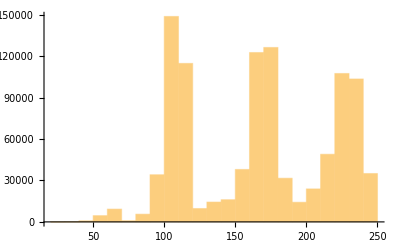

249

```mathematica
StringLength/@TrainSet$52204$wocriteria$CommonSet1$format3//Histogram
StringLength/@TrainSet$52204$wocriteria$CommonSet1$format3//Max
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/new1/valid_set_new1.txt",TrainSet$52204$wocriteria$CommonSet1$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/new1/test_set_new1.txt",TrainSet$52204$wocriteria$CommonSet1$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/new1/train_set_new1.txt",TrainSet$52204$wocriteria$CommonSet1$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/new1/valid_set_new1.txt

../../dataset_storage/new1/test_set_new1.txt

../../dataset_storage/new1/train_set_new1.txt

#### random split of coefficients of terms and constant (new2)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSetWithSplit[n_]:=Monitor[Flatten[Table[{longExpand,longSplit,short,sub}=RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}];
expandedForm=MMAExprToJFString[longExpand]<>" ? "<>MMAExprToJFString[sub];
splitForm=MMAExprToJFStringNonExpand[longSplit]<>" ? "<>MMAExprToJFString[sub];
{expandedForm,splitForm},{i,n}],1],Row[{"Generating element: ",i}]]
```

```mathematica
RandomPolynomialWithSplit2$PolyNInPoly2$LSS[5,2,20,4,{a[1]}]
```

{-90+448 a[1]-204 a[1]^2-976 a[1]^3-516 a[1]^4-72 a[1]^5-3 a[1]^6,-90+448 a[1]+-160 a[1]^2+-44 a[1]^2+-976 a[1]^3+-44 a[1]^4+-472 a[1]^4+-24 a[1]^5+-48 a[1]^5+-a[1]^6+-2 a[1]^6,-5+2 s-3 s^2,-5+14 a[1]+12 a[1]^2+a[1]^3}

```mathematica
-90+448 a[1]+-160 a[1]^2+-44 a[1]^2+-976 a[1]^3+-44 a[1]^4+-472 a[1]^4+-24 a[1]^5+-48 a[1]^5+-a[1]^6+-2 a[1]^6,-5+2 s-3 s^2,-5+14 a[1]+12 a[1]^2+a[1]^3
```

```mathematica
GenerateTrainSetWithSplit[2]
```

{+ P 7 1 2 + * P 1 4 9 8 a1 + * P 8 9 1 ^ a1 P 2 + * P 1 1 2 ^ a1 P 3 * P 4 ^ a1 P 4 ? + P 1 4 + * P 1 4 a1 ^ a1 P 2,+ P 7 1 2 + * P 1 3 5 6 a1 + * P 1 4 2 a1 + * P 1 4 8 ^ a1 P 2 + * P 7 4 3 ^ a1 P 2 + * P 5 0 ^ a1 P 3 + * P 6 2 ^ a1 P 3 + ^ a1 P 4 * P 3 ^ a1 P 4 ? + P 1 4 + * P 1 4 a1 ^ a1 P 2,+ P 2 3 + * N 1 8 9 a1 + * P 4 2 6 ^ a1 P 2 + * N 9 0 ^ a1 P 3 * P 5 ^ a1 P 4 ? + P 2 + * N 9 a1 ^ a1 P 2,+ P 2 3 + * N 1 8 9 a1 + * P 1 0 ^ a1 P 2 + * P 4 1 6 ^ a1 P 2 + * N 6 8 ^ a1 P 3 + * N 2 2 ^ a1 P 3 + ^ a1 P 4 * P 4 ^ a1 P 4 ? + P 2 + * N 9 a1 ^ a1 P 2}

```mathematica
TrainSet$52204$format3$wsplit=GenerateTrainSetWithSplit[700000];
TrainSet$52204$format3$wsplit=DeleteDuplicates[TrainSet$52204$format3$wsplit];
Length[TrainSet$52204$format3$wsplit]
```

1372319

```mathematica
TrainSet$52204$format3$wsplit=RandomSample[TrainSet$52204$format3$wsplit];
```

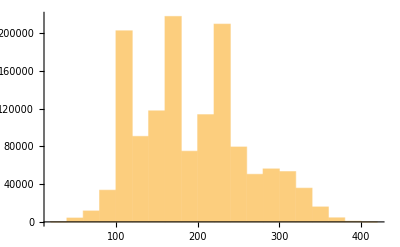

419

```mathematica
StringLength/@TrainSet$52204$format3$wsplit//Histogram
StringLength/@TrainSet$52204$format3$wsplit//Max
```

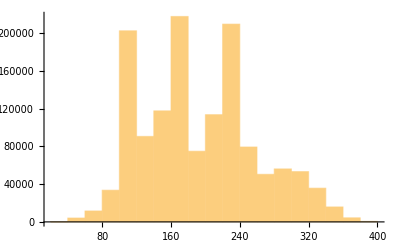

390

```mathematica
TrainSet$52204$format3$wsplit2=Select[TrainSet$52204$format3$wsplit,StringLength[#]<=390&];
StringLength/@TrainSet$52204$format3$wsplit2//Histogram
StringLength/@TrainSet$52204$format3$wsplit2//Max
```

```mathematica
Export["../../dataset_storage/new2/valid_set_new2.txt",TrainSet$52204$format3$wsplit2[[1;;128]],"Text"]
Export["../../dataset_storage/new2/test_set_new2.txt",TrainSet$52204$format3$wsplit2[[129;;3128]],"Text"]
Export["../../dataset_storage/new2/train_set_new2.txt",TrainSet$52204$format3$wsplit2[[3129;;1003128]],"Text"]
```

../../dataset_storage/new2/valid_set_new2.txt

../../dataset_storage/new2/test_set_new2.txt

../../dataset_storage/new2/train_set_new2.txt

#### new Generalization test5 on new1,2 ( without constraint, original coefficient out of scope : 6 - 10)

```mathematica
GenerateExp33$Gen5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[6,10,2,0,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen5$CommonSet[5]
```

{{1461+868 a[1]+4034 a[1]^2+935 a[1]^3+2528 a[1]^4-288 a[1]^5+8 a[1]^6,-8-9 s+8 s^2,-13-4 a[1]-18 a[1]^2+a[1]^3},{45-528 a[1]+1396 a[1]^2+2325 a[1]^3+3439 a[1]^4+2072 a[1]^5+1015 a[1]^6+154 a[1]^7+7 a[1]^8,9+9 s+7 s^2,-3+16 a[1]+12 a[1]^2+11 a[1]^3+a[1]^4},{711-2736 a[1]+2440 a[1]^2+288 a[1]^3+8 a[1]^4,-9-8 s+8 s^2,-9+18 a[1]+a[1]^2},{-1170-3296 a[1]-4364 a[1]^2+416 a[1]^3+3502 a[1]^4+2592 a[1]^5-2484 a[1]^6+288 a[1]^7-9 a[1]^8,6+10 s-9 s^2,12+16 a[1]+10 a[1]^2-16 a[1]^3+a[1]^4},{-4-130 a[1]+1542 a[1]^2-4072 a[1]^3+5374 a[1]^4-3440 a[1]^5+848 a[1]^6+192 a[1]^7+8 a[1]^8,-6+6 s+8 s^2,-1+13 a[1]-19 a[1]^2+12 a[1]^3+a[1]^4}}

```mathematica
Exp33$Gen5$CommonSet=GenerateExp33$Gen5$CommonSet[400000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen5$CommonSet=DeleteDuplicates[Exp33$Gen5$CommonSet];
Length[Exp33$Gen5$CommonSet]
```

394470

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen5$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen5$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen5$format3=GenerateExp33$Gen5$format3[Length[Exp33$Gen5$CommonSet]];
```

```mathematica
Exp33$Gen5$format3⟦1;;2⟧
```

{+ P 1 6 8 8 + * N 1 2 3 0 a1 + * P 4 7 1 ^ a1 P 2 + * N 9 0 ^ a1 P 3 * P 9 ^ a1 P 4 ? + P 1 4 + * N 5 a1 ^ a1 P 2,+ N 3 0 5 3 + * N 2 9 8 8 a1 + * N 1 0 6 1 ^ a1 P 2 + * P 1 7 0 ^ a1 P 3 + * P 1 5 3 ^ a1 P 4 + * P 1 8 ^ a1 P 5 * N 9 ^ a1 P 6 ? + N 1 8 + * N 9 a1 + * N 1 ^ a1 P 2 ^ a1 P 3}

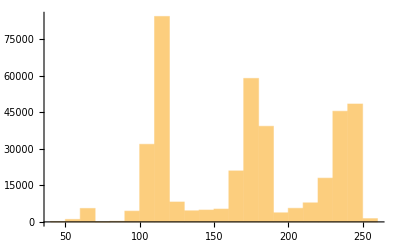

257

```mathematica
StringLength/@Exp33$Gen5$format3//Histogram
StringLength/@Exp33$Gen5$format3//Max
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/new_gen5/new_gen5_test.txt",Exp33$Gen5$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_valid.txt",Exp33$Gen5$format3⟦3001;;3128⟧,"Text"]

Export["../../dataset_storage/new_gen5/new_gen5_2560_train1.txt",Exp33$Gen5$format3⟦3129;;5688⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_2560_train2.txt",Exp33$Gen5$format3⟦5689;;8248⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_2560_train3.txt",Exp33$Gen5$format3⟦8249;;10808⟧,"Text"]

Export["../../dataset_storage/new_gen5/new_gen5_5120_train1.txt",Exp33$Gen5$format3⟦3129;;8248⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_5120_train2.txt",Exp33$Gen5$format3⟦8249;;13368⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_5120_train3.txt",Exp33$Gen5$format3⟦13369;;18488⟧,"Text"]

Export["../../dataset_storage/new_gen5/new_gen5_10240_train1.txt",Exp33$Gen5$format3⟦3129;;13368⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_10240_train2.txt",Exp33$Gen5$format3⟦13369;;23608⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_10240_train3.txt",Exp33$Gen5$format3⟦23609;;33848⟧,"Text"]

Export["../../dataset_storage/new_gen5/new_gen5_25k_train1.txt",Exp33$Gen5$format3⟦3129;;28128⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_25k_train2.txt",Exp33$Gen5$format3⟦28129;;53128⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_25k_train3.txt",Exp33$Gen5$format3⟦53129;;78128⟧,"Text"]

Export["../../dataset_storage/new_gen5/new_gen5_50k_train1.txt",Exp33$Gen5$format3⟦3129;;53128⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_50k_train2.txt",Exp33$Gen5$format3⟦53129;;103128⟧,"Text"]
Export["../../dataset_storage/new_gen5/new_gen5_50k_train3.txt",Exp33$Gen5$format3⟦103129;;153128⟧,"Text"]
```

../../dataset_storage/new_gen5/new_gen5_test.txt

../../dataset_storage/new_gen5/new_gen5_valid.txt

../../dataset_storage/new_gen5/new_gen5_2560_train1.txt

../../dataset_storage/new_gen5/new_gen5_2560_train2.txt

../../dataset_storage/new_gen5/new_gen5_2560_train3.txt

../../dataset_storage/new_gen5/new_gen5_5120_train1.txt

../../dataset_storage/new_gen5/new_gen5_5120_train2.txt

../../dataset_storage/new_gen5/new_gen5_5120_train3.txt

../../dataset_storage/new_gen5/new_gen5_10240_train1.txt

../../dataset_storage/new_gen5/new_gen5_10240_train2.txt

../../dataset_storage/new_gen5/new_gen5_10240_train3.txt

../../dataset_storage/new_gen5/new_gen5_25k_train1.txt

../../dataset_storage/new_gen5/new_gen5_25k_train2.txt

../../dataset_storage/new_gen5/new_gen5_25k_train3.txt

../../dataset_storage/new_gen5/new_gen5_50k_train1.txt

../../dataset_storage/new_gen5/new_gen5_50k_train2.txt

../../dataset_storage/new_gen5/new_gen5_50k_train3.txt

#### new Generalization test6 on new1,2 ( without constraint, sub coefficient out of scope : 21 - 30)

```mathematica
GenerateExp33$Gen6$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly2$LSS[0,5,2,21,30,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen6$CommonSet[2]
```

{{2808-212 a[1]+4 a[1]^2,4 s+4 s^2,-27+a[1]},{-2116-184 a[1]-4 a[1]^2,-4 s^2,23+a[1]}}

```mathematica
Exp33$Gen6$CommonSet=GenerateExp33$Gen6$CommonSet[1000000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen6$CommonSet=DeleteDuplicates[Exp33$Gen6$CommonSet];
Length[Exp33$Gen6$CommonSet]
```

526963

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen6$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen6$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen6$format3=GenerateExp33$Gen6$format3[Length[Exp33$Gen6$CommonSet]];
```

```mathematica
Exp33$Gen6$format3⟦1;;3⟧
```

{+ P 1 1 5 0 + * N 2 1 1 2 a1 + * N 1 8 1 6 ^ a1 P 2 + * P 2 4 5 6 ^ a1 P 3 + * P 1 7 7 0 ^ a1 P 4 + * P 1 1 6 ^ a1 P 5 * P 2 ^ a1 P 6 ? + N 2 5 + * P 2 2 a1 + * P 2 9 ^ a1 P 2 ^ a1 P 3,+ N 1 0 5 6 + * P 2 2 0 8 a1 + * P 1 2 4 0 ^ a1 P 2 + * N 2 5 8 8 ^ a1 P 3 + * N 1 2 5 6 ^ a1 P 4 + * P 1 0 4 ^ a1 P 5 * N 2 ^ a1 P 6 ? + P 2 2 + * N 2 4 a1 + * N 2 6 ^ a1 P 2 ^ a1 P 3,+ P 2 0 5 2 + * P 1 5 7 a1 * P 3 ^ a1 P 2 ? + P 2 7 a1}

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/gen6/gen6_big_test.txt",Exp33$Gen6$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_big_valid.txt",Exp33$Gen6$format3⟦3001;;3128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train1.txt",Exp33$Gen6$format3⟦3129;;103128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train2.txt",Exp33$Gen6$format3⟦103129;;203128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train3.txt",Exp33$Gen6$format3⟦203129;;303128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train4.txt",Exp33$Gen6$format3⟦303129;;403128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_train5.txt",Exp33$Gen6$format3⟦403129;;503128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_tiny_train.txt",Exp33$Gen6$format3⟦3129;;13368⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_small_train.txt",Exp33$Gen6$format3⟦3129;;28128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_middle_train.txt",Exp33$Gen6$format3⟦3129;;53128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_big_train.txt",Exp33$Gen6$format3⟦3129;;253128⟧,"Text"]
Export["../../dataset_storage/gen6/gen6_bigbig_train.txt",Exp33$Gen6$format3⟦3129;;503128⟧,"Text"]
```

../../dataset_storage/gen6/gen6_big_test.txt

../../dataset_storage/gen6/gen6_big_valid.txt

../../dataset_storage/gen6/gen6_train1.txt

../../dataset_storage/gen6/gen6_train2.txt

../../dataset_storage/gen6/gen6_train3.txt

../../dataset_storage/gen6/gen6_train4.txt

../../dataset_storage/gen6/gen6_train5.txt

../../dataset_storage/gen6/gen6_tiny_train.txt

../../dataset_storage/gen6/gen6_small_train.txt

../../dataset_storage/gen6/gen6_middle_train.txt

../../dataset_storage/gen6/gen6_big_train.txt

../../dataset_storage/gen6/gen6_bigbig_train.txt

#### new Generalization test7 on new1 ( release constraint on constant term )

```mathematica
GenerateExp33$Gen7$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$gen7$LSS[5,2,{{-40,40},{-20,20},{-20,20},{-20,20}},{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen7$CommonSet[2]
```

{{-4595-3636 a[1]+1098 a[1]^2-1098 a[1]^3-1203 a[1]^4+240 a[1]^5-120 a[1]^6-60 a[1]^7-5 a[1]^8,-5-3 s-5 s^2,30+12 a[1]-6 a[1]^2+6 a[1]^3+a[1]^4},{-3851-3655 a[1]-2587 a[1]^2+904 a[1]^3+839 a[1]^4+486 a[1]^5-144 a[1]^6-48 a[1]^7-3 a[1]^8,1-s-3 s^2,-36-17 a[1]-8 a[1]^2+8 a[1]^3+a[1]^4}}

```mathematica
Exp33$Gen7$CommonSet=GenerateExp33$Gen7$CommonSet[100000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen7$CommonSet=DeleteDuplicates[Exp33$Gen7$CommonSet];
Length[Exp33$Gen7$CommonSet]
```

100000

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen7$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen7$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen7$format3=GenerateExp33$Gen7$format3[Length[Exp33$Gen7$CommonSet]];
```

```mathematica
Exp33$Gen7$format3⟦1;;3⟧
```

{+ P 3 1 9 5 + * N 3 2 0 a1 + * P 3 0 4 8 ^ a1 P 2 + * P 6 4 8 ^ a1 P 3 + * P 8 4 2 ^ a1 P 4 + * P 3 7 2 ^ a1 P 5 + * P 1 2 6 ^ a1 P 6 + * P 2 0 ^ a1 P 7 * P 2 ^ a1 P 8 ? + P 4 0 + * N 2 a1 + * P 1 9 ^ a1 P 2 + * P 5 ^ a1 P 3 ^ a1 P 4,+ P 4 1 + * N 8 1 a1 + * N 3 3 3 ^ a1 P 2 + * P 9 6 0 ^ a1 P 3 + * P 3 5 3 ^ a1 P 4 + * N 2 7 7 0 ^ a1 P 5 + * P 2 1 4 0 ^ a1 P 6 + * N 2 0 0 ^ a1 P 7 * P 5 ^ a1 P 8 ? + N 3 + * P 3 a1 + * P 1 4 ^ a1 P 2 + * N 2 0 ^ a1 P 3 ^ a1 P 4,+ P 4 5 1 8 + * P 1 8 8 3 a1 + * P 7 3 4 ^ a1 P 2 + * N 2 3 0 9 ^ a1 P 3 + * N 2 1 9 ^ a1 P 4 + * N 8 8 ^ a1 P 5 + * P 3 4 0 ^ a1 P 6 + * N 7 2 ^ a1 P 7 * P 4 ^ a1 P 8 ? + P 3 3 + * P 7 a1 + * P 2 ^ a1 P 2 + * N 9 ^ a1 P 3 ^ a1 P 4}

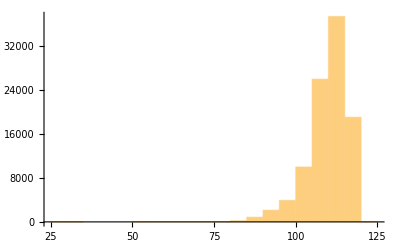

```mathematica
(Length/@StringSplit/@Exp33$Gen7$format3)//Histogram
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/datasets/gen7/gen7_test.txt",Exp33$Gen7$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_valid.txt",Exp33$Gen7$format3⟦3001;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_5120_train.txt",Exp33$Gen7$format3⟦3129;;8248⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_10240_train.txt",Exp33$Gen7$format3⟦8249;;18488⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_25k_train.txt",Exp33$Gen7$format3⟦18489;;43488⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_50k_train.txt",Exp33$Gen7$format3⟦43489;;93488⟧,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_2560_train.txt",Exp33$Gen7$format3⟦93489;;96048⟧,"Text"]
```

../../dataset_storage/datasets/gen7/gen7_test.txt

../../dataset_storage/datasets/gen7/gen7_valid.txt

../../dataset_storage/datasets/gen7/gen7_5120_train.txt

../../dataset_storage/datasets/gen7/gen7_10240_train.txt

../../dataset_storage/datasets/gen7/gen7_25k_train.txt

../../dataset_storage/datasets/gen7/gen7_50k_train.txt

../../dataset_storage/datasets/gen7/gen7_2560_train.txt

```mathematica
(* releasing constraint in other positions *)
```

```mathematica
GenerateExp33$Gen7$constant[n_]:=
Monitor[
Table[
{long,short,sub}=RandomPolynomial$gen7$LSS[5,2,{{21,40},{-20,20},{-20,20},{-20,20}},{a[1]}];
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen7$linear[n_]:=
Monitor[
Table[
{long,short,sub}=RandomPolynomial$gen7$LSS[5,2,{{-20,20},{21,40},{-20,20},{-20,20}},{a[1]}];
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]
];
GenerateExp33$Gen7$quadratic[n_]:=
Monitor[
Table[
{long,short,sub}=RandomPolynomial$gen7$LSS[5,2,{{-20,20},{-20,20},{21,40},{-20,20}},{a[1]}];
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]
];
GenerateExp33$Gen7$cube[n_]:=
Monitor[
Table[
{long,short,sub}=RandomPolynomial$gen7$LSS[5,2,{{-20,20},{-20,20},{-20,20},{21,40}},{a[1]}];
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Gen7$constant=GenerateExp33$Gen7$constant[3000];
Gen7$linear=GenerateExp33$Gen7$linear[3000];
Gen7$quadratic=GenerateExp33$Gen7$quadratic[3000];
Gen7$cube=GenerateExp33$Gen7$cube[3000];
```

```mathematica
Export["../../dataset_storage/datasets/gen7/gen7_constant_test.txt",Gen7$constant,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_linear_test.txt",Gen7$linear,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_quadratic_test.txt",Gen7$quadratic,"Text"]
Export["../../dataset_storage/datasets/gen7/gen7_cube_test.txt",Gen7$cube,"Text"]
```

../../dataset_storage/datasets/gen7/gen7_constant_test.txt

../../dataset_storage/datasets/gen7/gen7_linear_test.txt

../../dataset_storage/datasets/gen7/gen7_quadratic_test.txt

../../dataset_storage/datasets/gen7/gen7_cube_test.txt

#### new Generalization test8 on new1 ( release constraint on linear term )

```mathematica
GenerateExp33$Gen8$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$gen7$LSS[5,2,{{-20,20},{-40,40},{-20,20},{-20,20}},{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateExp33$Gen8$CommonSet[2]
```

{{398+1320 a[1]+1449 a[1]^2+674 a[1]^3+253 a[1]^4+102 a[1]^5+22 a[1]^6+4 a[1]^7+a[1]^8,2+4 s+s^2,18+33 a[1]+9 a[1]^2+2 a[1]^3+a[1]^4},{-426+1826 a[1]-359 a[1]^2-2763 a[1]^3-2593 a[1]^4-1240 a[1]^5-348 a[1]^6-56 a[1]^7-4 a[1]^8,3-5 s-4 s^2,-11+22 a[1]+19 a[1]^2+7 a[1]^3+a[1]^4}}

```mathematica
Exp33$Gen8$CommonSet=GenerateExp33$Gen8$CommonSet[100000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
Exp33$Gen8$CommonSet=DeleteDuplicates[Exp33$Gen8$CommonSet];
Length[Exp33$Gen8$CommonSet]
```

100000

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp33$Gen8$format3[n_]:=
Monitor[
Table[
{long,short,sub}=Exp33$Gen8$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp33$Gen8$format3=GenerateExp33$Gen8$format3[Length[Exp33$Gen8$CommonSet]];
```

```mathematica
Exp33$Gen8$format3⟦1;;3⟧
```

{+ N 1 5 1 3 + * N 1 0 4 4 a1 + * N 3 4 8 6 ^ a1 P 2 + * N 1 4 8 8 ^ a1 P 3 + * N 1 7 5 1 ^ a1 P 4 + * N 3 2 0 ^ a1 P 5 + * P 1 7 0 ^ a1 P 6 + * P 2 0 ^ a1 P 7 * N 5 ^ a1 P 8 ? + N 1 7 + * N 6 a1 + * N 1 9 ^ a1 P 2 + * N 2 ^ a1 P 3 ^ a1 P 4,+ P 6 4 + * N 1 7 6 a1 + * P 2 0 1 ^ a1 P 2 + * N 3 0 ^ a1 P 3 + * N 6 9 ^ a1 P 4 + * P 2 8 ^ a1 P 5 + * P 3 5 ^ a1 P 6 + * P 1 0 ^ a1 P 7 ^ a1 P 8 ? + P 8 + * N 1 1 a1 + * P 5 ^ a1 P 2 + * P 5 ^ a1 P 3 ^ a1 P 4,+ N 8 0 + * N 3 4 2 a1 + * N 2 7 1 ^ a1 P 2 + * P 4 7 8 ^ a1 P 3 + * P 5 6 5 ^ a1 P 4 + * N 1 9 8 ^ a1 P 5 + * N 2 4 6 ^ a1 P 6 + * P 3 2 ^ a1 P 7 * N 1 ^ a1 P 8 ? + P 9 + * P 1 9 a1 + * N 5 ^ a1 P 2 + * N 1 6 ^ a1 P 3 ^ a1 P 4}

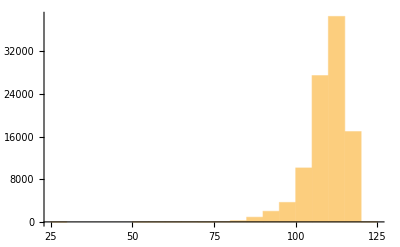

```mathematica
(Length/@StringSplit/@Exp33$Gen8$format3)//Histogram
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/datasets/gen8/gen8_test.txt",Exp33$Gen8$format3⟦1;;3000⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_valid.txt",Exp33$Gen8$format3⟦3001;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_5120_train.txt",Exp33$Gen8$format3⟦3129;;8248⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_10240_train.txt",Exp33$Gen8$format3⟦8249;;18488⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_25k_train.txt",Exp33$Gen8$format3⟦18489;;43488⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_50k_train.txt",Exp33$Gen8$format3⟦43489;;93488⟧,"Text"]
Export["../../dataset_storage/datasets/gen8/gen8_2560_train.txt",Exp33$Gen8$format3⟦93489;;96048⟧,"Text"]
```

../../dataset_storage/datasets/gen8/gen8_test.txt

../../dataset_storage/datasets/gen8/gen8_valid.txt

../../dataset_storage/datasets/gen8/gen8_5120_train.txt

../../dataset_storage/datasets/gen8/gen8_10240_train.txt

../../dataset_storage/datasets/gen8/gen8_25k_train.txt

../../dataset_storage/datasets/gen8/gen8_50k_train.txt

../../dataset_storage/datasets/gen8/gen8_2560_train.txt

#### new3 ( no constraint )

```mathematica
GenerateTrainSet$52204$new3$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[5,2,20,4,{a[1]}],{i,n}],
Row[{"Generating element: ", i}]
];
GenerateTrainSet$52204$new3$CommonSet2[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly1$LSS[5,2,20,4,{a[1]},ComplexityCriteria],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$52204$new3$CommonSet[10]//TableForm
```

-352+75 a[1]+896 a[1]^2+1029 a[1]^3-1971 a[1]^4-1304 a[1]^5+732 a[1]^6+2040 a[1]^7-1156 a[1]^8 | -2-5 s-4 s^2 | -10+a[1]+12 a[1]^2+15 a[1]^3-17 a[1]^4
-236+528 a[1]-376 a[1]^2+184 a[1]^3-104 a[1]^4+16 a[1]^5-8 a[1]^6 | 4-4 s-2 s^2 | 10-12 a[1]+2 a[1]^2-2 a[1]^3
48+56 a[1]-96 a[1]^2-64 a[1]^3+64 a[1]^4 | -4 s+4 s^2 | -3-2 a[1]+4 a[1]^2
-203-399 a[1]+431 a[1]^2-296 a[1]^3-1380 a[1]^4+1408 a[1]^5-1024 a[1]^6 | s-4 s^2 | -7-7 a[1]+11 a[1]^2-16 a[1]^3
-1655+3260 a[1]-2415 a[1]^2+2104 a[1]^3-565 a[1]^4-480 a[1]^5-56 a[1]^6-320 a[1]^7-100 a[1]^8 | 5-3 s-4 s^2 | 20-20 a[1]+5 a[1]^2-8 a[1]^3-5 a[1]^4
252-110 a[1]-868 a[1]^2-28 a[1]^3+816 a[1]^4+384 a[1]^5+48 a[1]^6 | -s+3 s^2 | -9+2 a[1]+16 a[1]^2+4 a[1]^3
-447+60 a[1]-482 a[1]^2+1232 a[1]^3+332 a[1]^4+604 a[1]^5-512 a[1]^6-720 a[1]^7-162 a[1]^8 | 1-4 s-2 s^2 | -16+a[1]-8 a[1]^2+20 a[1]^3+9 a[1]^4
-34-140 a[1]-227 a[1]^2+12 a[1]^3+330 a[1]^4+216 a[1]^5-243 a[1]^6 | -1+2 s-3 s^2 | -3-7 a[1]-4 a[1]^2+9 a[1]^3
-324+255 a[1]-815 a[1]^2+300 a[1]^3-450 a[1]^4 | 3 s-2 s^2 | -12+5 a[1]-15 a[1]^2
581-680 a[1]-276 a[1]^2+1028 a[1]^3+542 a[1]^4-828 a[1]^5-122 a[1]^6+572 a[1]^7+338 a[1]^8 | 5-4 s+2 s^2 | -16+10 a[1]+7 a[1]^2-11 a[1]^3-13 a[1]^4

```mathematica
TrainSet$52204$new3$CommonSet=GenerateTrainSet$52204$new3$CommonSet[120000];
```

```mathematica
TrainSet$52204$new3$CommonSet2=GenerateTrainSet$52204$new3$CommonSet2[12000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$52204$new3$CommonSet=DeleteDuplicates[TrainSet$52204$new3$CommonSet];
Length[TrainSet$52204$new3$CommonSet]
```

119991

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$52204$new3$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$new3$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
GenerateTrainSet$52204$new3$CommonSet2$format3[n_]:=
Monitor[
Table[
{long,short,sub}=TrainSet$52204$new3$CommonSet2⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$52204$new3$CommonSet$format3=GenerateTrainSet$52204$new3$CommonSet$format3[119000];
```

```mathematica
TrainSet$52204$new3$CommonSet2$format3=GenerateTrainSet$52204$new3$CommonSet2$format3[11900];
```

```mathematica
TrainSet$52204$new3$CommonSet$format3⟦1;;5⟧//TableForm
```

+ P 5 7 4 + * N 6 8 0 a1 + * N 4 ^ a1 P 2 + * N 9 0 0 ^ a1 P 3 + * P 6 1 8 ^ a1 P 4 + * P 1 8 0 ^ a1 P 5 * P 4 5 0 ^ a1 P 6 ? + N 1 6 + * P 1 0 a1 + * P 3 ^ a1 P 2 * P 1 5 ^ a1 P 3
+ N 2 9 5 + * N 5 8 8 a1 + * N 2 8 8 ^ a1 P 2 + * P 8 3 3 ^ a1 P 3 + * P 8 1 6 ^ a1 P 4 * N 5 7 8 ^ a1 P 6 ? + N 1 2 + * N 1 2 a1 * P 1 7 ^ a1 P 3
+ P 1 3 4 7 + * P 7 3 5 ^ a1 P 2 + * N 1 0 2 9 ^ a1 P 3 + * P 1 0 0 ^ a1 P 4 + * N 2 8 0 ^ a1 P 5 * P 1 9 6 ^ a1 P 6 ? + N 1 9 + * N 5 ^ a1 P 2 * P 7 ^ a1 P 3
+ P 2 0 8 + * N 4 1 a1 + * P 2 4 8 ^ a1 P 2 + * N 2 4 ^ a1 P 3 + * P 2 7 7 ^ a1 P 4 + * N 2 0 ^ a1 P 5 + * P 1 2 0 ^ a1 P 6 * P 5 0 ^ a1 P 8 ? + N 9 + a1 + * N 6 ^ a1 P 2 * N 5 ^ a1 P 4
+ N 9 0 + * P 1 9 8 a1 + * N 1 0 8 ^ a1 P 2 + * P 5 9 4 ^ a1 P 3 + * N 6 8 1 ^ a1 P 4 + * P 3 6 ^ a1 P 5 + * N 9 7 2 ^ a1 P 6 + * P 1 0 8 ^ a1 P 7 * N 3 ^ a1 P 8 ? + P 5 + * N 6 a1 + * N 1 8 ^ a1 P 3 ^ a1 P 4

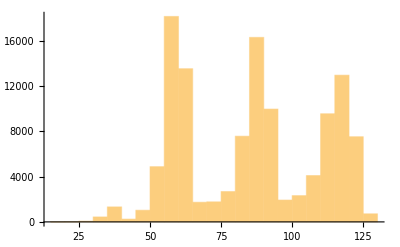

127

```mathematica
Length/@StringSplit/@TrainSet$52204$new3$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$52204$new3$CommonSet$format3//Max
```

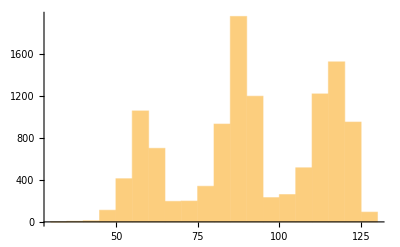

127

```mathematica
Length/@StringSplit/@TrainSet$52204$new3$CommonSet2$format3//Histogram
Length/@StringSplit/@TrainSet$52204$new3$CommonSet2$format3//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/new3/valid_set_new3.txt",TrainSet$52204$new3$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/new3/test_set_new3.txt",TrainSet$52204$new3$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/new3/train_set_new3.txt",TrainSet$52204$new3$CommonSet$format3⟦3129;;103128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/new3/valid_set_new3.txt

../../dataset_storage/datasets/new3/test_set_new3.txt

../../dataset_storage/datasets/new3/train_set_new3.txt

### Three-variable polynomial experiment ( previously exp 45 )

```mathematica
(* 5 2 (5 2,5 2) training set with complexity criteria,with constraints,three variables,maximum number of terms:3 (each) (Exp45) *)
```

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

-9 y+5 y^2 z

```mathematica
RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,3]
```

{12 a[1]+24 a[1]^3+36 a[1] a[2],-3 b[0]-3 b[0] b[1],-4 a[1],2 a[1]^2+3 a[2]}

```mathematica
RandomPolynomial$PolyNInPoly4$LSS[4,5,2,5,2,{a[1],a[2],a[3]},3,3]
RandomPolynomial$PolyNInPoly4$LSS[4,5,2,4,5,2,{a[1],a[2],a[3]},3,3]
RandomPolynomial$PolyNInPoly4$LSS[0,5,2,4,5,2,{a[1],a[2],a[3]},3,3]
```

{10 a[2]^2+8 a[3]-20 a[2]^2 a[3]+20 a[3]^2-40 a[3]^3,-4 b[0]+5 b[1]+5 b[0] b[1],-2 a[3],2 a[2]^2+4 a[3]^2}

{-20 a[1]-16 a[1]^2-100 a[1]^3+20 a[2]+125 a[1] a[2]-20 a[1] a[3]-100 a[1]^3 a[3]+125 a[1] a[2] a[3]+20 a[3]^2+125 a[1] a[3]^2+125 a[1] a[3]^3,4 b[0]-4 b[1]+5 b[0] b[1],-4 a[1]^2+5 a[2]+5 a[3]^2,5 a[1]+5 a[1] a[3]}

{8 a[1]^2+20 a[3]-8 a[2] a[3],2 b[0]+4 b[1],4 a[1]^2-4 a[2] a[3],5 a[3]}

#### CommonSet in a format 3 with short (Exp45)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$525252$three$3$CommonSet$format3$wshort[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$525252$three$3$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$525252$three$3$CommonSet$format3$wshort=GenerateTrainSet$525252$three$3$CommonSet$format3$wshort[Length[TrainSet$525252$three$3$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp45/valid_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp45/test_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp45/train_set_Exp45.txt",TrainSet$525252$three$3$CommonSet$format3$wshort⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp45/valid_set_Exp45.txt

../../dataset_storage/Exp45/test_set_Exp45.txt

../../dataset_storage/Exp45/train_set_Exp45.txt

#### Generalization test 0 on Exp52, 53 ( test Exp45 data(non split) on Exp52,53 )

```mathematica
GenerateExp45$generalization0[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization0=GenerateExp45$generalization0[1500];
```

```mathematica
Exp45$generalization0=DeleteDuplicates[Exp45$generalization0];
Length[Exp45$generalization0]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization0$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization0⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization0$format3=GenerateExp45$generalization0$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen0/gen0_test_Exp45.txt",Exp45$generalization0$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen0/gen0_test_Exp45.txt

#### Generalization test 1 on Exp45 ( original coefficient out of scope : 6 - 10 )

```mathematica
GenerateExp45$generalization1[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[6,10,2,5,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization1=GenerateExp45$generalization1[1500];
```

```mathematica
Exp45$generalization1=DeleteDuplicates[Exp45$generalization1];
Length[Exp45$generalization1]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization1$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization1⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization1$format3=GenerateExp45$generalization1$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen1/gen1_test_Exp45.txt",Exp45$generalization1$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen1/gen1_test_Exp45.txt

#### Generalization test 2 on Exp45 ( sub coefficient out of scope : 6 - 8 )

```mathematica
GenerateExp45$generalization2[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[0,5,2,6,8,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
Exp45$generalization2=GenerateExp45$generalization2[1500];
```

```mathematica
Exp45$generalization2=DeleteDuplicates[Exp45$generalization2];
Length[Exp45$generalization2]
```

1500

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateExp45$generalization2$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=Exp45$generalization2⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
Exp45$generalization2$format3=GenerateExp45$generalization2$format3[1500];
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/gen2/gen2_test_Exp45.txt",Exp45$generalization2$format3⟦1;;1500⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/gen2/gen2_test_Exp45.txt

#### train model in different training set (Exp 55-1, 55-2)

```mathematica
GenerateTrainSet$Exp55$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$Exp55$CommonSet=GenerateTrainSet$Exp55$CommonSet[2300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$Exp55$CommonSet=DeleteDuplicates[TrainSet$Exp55$CommonSet];
Length[TrainSet$Exp55$CommonSet]
```

2283884

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$Exp55$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$Exp55$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$Exp55$CommonSet$format3=GenerateTrainSet$Exp55$CommonSet$format3[Length[TrainSet$Exp55$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp55/valid_set_Exp55.txt",TrainSet$Exp55$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp55/test_set_Exp55.txt",TrainSet$Exp55$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp55/train_set_Exp55_1.txt",TrainSet$Exp55$CommonSet$format3⟦3129;;1003128⟧,"Text"]
Export["../../dataset_storage/Exp55/train_set_Exp55_2.txt",TrainSet$Exp55$CommonSet$format3⟦1003129;;2003128⟧,"Text"]
```

../../dataset_storage/Exp55/valid_set_Exp55.txt

../../dataset_storage/Exp55/test_set_Exp55.txt

../../dataset_storage/Exp55/train_set_Exp55_1.txt

../../dataset_storage/Exp55/train_set_Exp55_2.txt

#### further training the model with longer expressions (Exp 56)

```mathematica
GenerateTrainSet$Exp56$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly4$LSS[5,2,5,2,{a[1],a[2],a[3]},3,2,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$Exp56$CommonSet=GenerateTrainSet$Exp56$CommonSet[1300000];
```

```mathematica
(* remove the duplication *)
```

```mathematica
TrainSet$Exp56$CommonSet=DeleteDuplicates[TrainSet$Exp56$CommonSet];
Length[TrainSet$Exp56$CommonSet]
```

1299911

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$Exp56$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$Exp56$CommonSet⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[sub1]<>" $ "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[short]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$Exp56$CommonSet$format3=GenerateTrainSet$Exp56$CommonSet$format3[Length[TrainSet$Exp56$CommonSet]];
```

```mathematica
(* outputing in text file *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jaeha/inequality/MMA_package

```mathematica
Export["../../dataset_storage/Exp56/valid_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/Exp56/test_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/Exp56/train_set_Exp56.txt",TrainSet$Exp56$CommonSet$format3⟦3129;;1003128⟧,"Text"]
```

../../dataset_storage/Exp56/valid_set_Exp56.txt

../../dataset_storage/Exp56/test_set_Exp56.txt

../../dataset_storage/Exp56/train_set_Exp56.txt

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdata$long=TestData$FromFile2["../../dataset_storage/Exp56/test_set_Exp56.txt"];
LeafCount/@testdata⟦hardcases⟧//Histogram
LeafCount/@testdata$long//Histogram
```

-Graphics-

-Graphics-

### Five-variable polynomial experiment ( extension of exp 45 )

```mathematica
(* 5 2 (5 2,5 2) training set with complexity criteria,with constraints,three variables,maximum number of terms:3 (each) (Exp45) *)
```

```mathematica
RandomPolynomial$maxlength[9,3,{x,y,z},3]
```

-3 x y z+5 y^2 z-3 z^2

```mathematica
RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},3,3]
```

{400 a[0] a[1]^6 a[3]^2+80 a[0]^2 a[1]^4 a[3]^3-32 a[0]^2 a[1]^3 a[3]^4-16 a[0]^2 a[1]^2 a[2] a[3]^4+16 a[0] a[1]^2 a[2] a[3]^5+32 a[0] a[1]^2 a[2]^2 a[3]^3 a[4],5 b[1]^2 b[2]-b[0] b[1] b[3]-b[1] b[3] b[4],-2 a[0] a[1] a[3]+2 a[2]^2 a[4],4 a[1]^2 a[3],5 a[0] a[1]^2+a[0]^2 a[3],-4 a[0] a[3]^2,-a[0] a[2] a[3]+a[2] a[3]^2}

#### CommonSet in a format 3 with short 3 VARIABLES (Exp59)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3vars$10310355$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[10,3,10,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$3vars$10310355$CommonSet = GenerateTrainSet$3vars$10310355$CommonSet[100000];
TrainSet$3vars$10310355$CommonSet = DeleteDuplicates[TrainSet$3vars$10310355$CommonSet];
Length[TrainSet$3vars$10310355$CommonSet]
```

100000

```mathematica
TrainSet$3vars$10310355$CommonSet[[1]]
```

{1029 a[0] a[1]^8-735 a[1]^9+294 a[0]^3 a[1]^5 a[2]+525 a[0]^2 a[1]^6 a[2]-2730 a[0] a[1]^7 a[2]+1050 a[1]^8 a[2]+21 a[0]^5 a[1]^2 a[2]^2-57 a[0]^4 a[1]^3 a[2]^2-1398 a[0]^3 a[1]^4 a[2]^2-180 a[0]^2 a[1]^5 a[2]^2+4365 a[0] a[1]^6 a[2]^2-711 a[1]^7 a[2]^2-21 a[0]^6 a[2]^3-252 a[0]^5 a[1] a[2]^3-546 a[0]^4 a[1]^2 a[2]^3+1680 a[0]^3 a[1]^3 a[2]^3-741 a[0]^2 a[1]^4 a[2]^3-876 a[0] a[1]^5 a[2]^3-1020 a[1]^6 a[2]^3-384 a[0]^4 a[1] a[2]^4-2088 a[0]^3 a[1]^2 a[2]^4+3036 a[0]^2 a[1]^3 a[2]^4-144 a[0] a[1]^4 a[2]^4-540 a[1]^5 a[2]^4-2016 a[0]^2 a[1]^2 a[2]^5+216 a[1]^3 a[2]^6,-3 b[0] b[1]^2-10 b[0] b[1] b[2]-6 b[1]^2 b[2]-8 b[0] b[2]^2-b[2]^3,-7 a[0] a[1]^2+5 a[1]^3+7 a[0]^2 a[2],-7 a[1]^3-a[0]^2 a[2]-6 a[0] a[1] a[2]+5 a[1]^2 a[2],-6 a[1] a[2]^2}

```mathematica
GenerateTrainSet$3vars$10310355$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3}=TrainSet$3vars$10310355$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$3vars$10310355$CommonSet$format3=GenerateTrainSet$3vars$10310355$CommonSet$format3[100000];
```

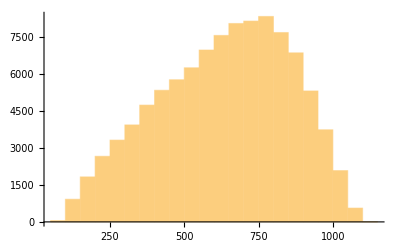

1136

```mathematica
Length/@StringSplit/@TrainSet$3vars$10310355$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$3vars$10310355$CommonSet$format3//Max
```

```mathematica
TrainSet$3vars$10310355$CommonSet$format3$reduced=Select[TrainSet$3vars$10310355$CommonSet$format3,Length[StringSplit[#]]<5000&];
Length[%]
Length/@StringSplit/@TrainSet$3vars$10310355$CommonSet$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3vars$10310355$CommonSet$format3$reduced//Max
```

100000

-Graphics-

1136

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_3var1.txt",TrainSet$3vars$10310355$CommonSet$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_3var1.txt",TrainSet$3vars$10310355$CommonSet$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_3var1.txt",TrainSet$3vars$10310355$CommonSet$format3$reduced⟦3129;;99961⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_3var1.txt

../../dataset_storage/datasets/multi/test_set_3var1.txt

../../dataset_storage/datasets/multi/train_set_3var1.txt

#### CommonSet in a format 3 with short 4 VARIABLES (Exp59)

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$4vars$10310355$CommonSet[n_]:=Monitor[Table[RandomPolynomial$PolyNInPoly6$LSS[10,3,10,3,{b[0],b[1],b[2], b[3]},{a[0],a[1],a[2], a[3]},5,5],{i,n}],Row[{"Generating element: ",i}]];
```

```mathematica
TrainSet$4vars$10310355$CommonSet=GenerateTrainSet$4vars$10310355$CommonSet[100000];
TrainSet$4vars$10310355$CommonSet=DeleteDuplicates[TrainSet$4vars$10310355$CommonSet];
Length[TrainSet$4vars$10310355$CommonSet]
```

100000

```mathematica
GenerateTrainSet$4vars$10310355$CommonSet$format3[n_]:=Monitor[Table[{long,short,sub1,sub2,sub3, sub4}=TrainSet$4vars$10310355$CommonSet[[i]];
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4],{i,n}],Row[{"Generating element: ",i}]];
```

```mathematica
TrainSet$4vars$10310355$CommonSet$format3=GenerateTrainSet$4vars$10310355$CommonSet$format3[100000];
```

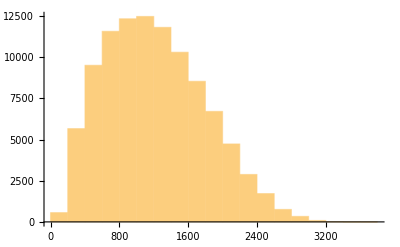

3624

```mathematica
Length/@StringSplit/@TrainSet$4vars$10310355$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$4vars$10310355$CommonSet$format3//Max
```

```mathematica
TrainSet$4vars$10310355$CommonSet$format3$reduced=Select[TrainSet$4vars$10310355$CommonSet$format3,Length[StringSplit[#]]<5000&];
Length[%]
Length/@StringSplit/@TrainSet$4vars$10310355$CommonSet$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$4vars$10310355$CommonSet$format3$reduced//Max
```

100000

-Graphics-

3624

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_4var1.txt",TrainSet$4vars$10310355$CommonSet$format3$reduced[[1;;128]],"Text"]
Export["../../dataset_storage/datasets/multi/test_set_4var1.txt",TrainSet$4vars$10310355$CommonSet$format3$reduced[[129;;3128]],"Text"]
Export["../../dataset_storage/datasets/multi/train_set_4var1.txt",TrainSet$4vars$10310355$CommonSet$format3$reduced[[3129;;99961]],"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_4var1.txt

../../dataset_storage/datasets/multi/test_set_4var1.txt

../../dataset_storage/datasets/multi/train_set_4var1.txt

#### CommonSet in a format 3 with short 5 VARIABLE (same setting with Exp45)

```mathematica
(* both original and substitution has fixed degree terms / original has a fixed number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5vars$535355$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},5,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$5vars$535355$CommonSet[5]//TableForm
```

-128 a[1]^9+25 a[0]^8 a[2]-10 a[0]^5 a[1]^3 a[2]+a[0]^2 a[1]^6 a[2]-375 a[0]^6 a[1] a[2]^2+150 a[0]^3 a[1]^4 a[2]^2-15 a[1]^7 a[2]^2-375 a[0]^8 a[3]+150 a[0]^5 a[1]^3 a[3]-495 a[0]^2 a[1]^6 a[3]-600 a[0]^4 a[1]^3 a[3]^2-250 a[0]^6 a[3]^3-150 a[0]^6 a[2]^2 a[4]+60 a[0]^3 a[1]^3 a[2]^2 a[4]-6 a[1]^6 a[2]^2 a[4]-125 a[0]^6 a[3] a[4]^2+50 a[0]^3 a[1]^3 a[3] a[4]^2-5 a[1]^6 a[3] a[4]^2-384 a[1]^6 a[4]^3-960 a[0]^2 a[1]^3 a[3] a[4]^3-600 a[0]^4 a[3]^2 a[4]^3-384 a[1]^3 a[4]^6-480 a[0]^2 a[3] a[4]^6-128 a[4]^9 | 2 b[1]^3-b[0]^2 b[2]+3 b[0]^2 b[3] | 5 a[0]^3-a[1]^3 | -4 a[1]^3-5 a[0]^2 a[3]-4 a[4]^3 | 2 a[0]^2 a[2]+5 a[3] a[4]^2 | a[0]^2 a[2]-5 a[1] a[2]^2-5 a[0]^2 a[3]-2 a[2]^2 a[4] | -2 a[1]^2 a[4]+4 a[1] a[3] a[4]+2 a[0] a[4]^2+a[2] a[4]^2
-40 a[0]^6 a[3]^3-24 a[0] a[1] a[2]^4 a[3]^3-128 a[2]^6 a[3]^3-18 a[0]^2 a[1] a[2]^2 a[3]^4+12 a[0] a[1] a[2]^3 a[3]^4-288 a[0] a[2]^4 a[3]^4+192 a[2]^5 a[3]^4-216 a[0]^2 a[2]^2 a[3]^5+288 a[0] a[2]^3 a[3]^5-96 a[2]^4 a[3]^5-54 a[0]^3 a[3]^6+108 a[0]^2 a[2] a[3]^6-72 a[0] a[2]^2 a[3]^6+16 a[2]^3 a[3]^6-30 a[0]^2 a[1] a[2]^2 a[3]^3 a[4]+48 a[1] a[2]^4 a[3]^3 a[4]+36 a[0] a[1] a[2]^2 a[3]^4 a[4]-24 a[1] a[2]^3 a[3]^4 a[4]+8 a[0] a[1] a[2]^4 a[3] a[4]^2+6 a[0]^2 a[1] a[2]^2 a[3]^2 a[4]^2-4 a[0] a[1] a[2]^3 a[3]^2 a[4]^2+66 a[0] a[1] a[2]^2 a[3]^3 a[4]^2+48 a[1] a[2]^3 a[3]^3 a[4]^2+96 a[2]^4 a[3]^3 a[4]^2+36 a[0] a[1] a[2] a[3]^4 a[4]^2+144 a[0] a[2]^2 a[3]^4 a[4]^2-24 a[1] a[2]^2 a[3]^4 a[4]^2-96 a[2]^3 a[3]^4 a[4]^2+54 a[0]^2 a[3]^5 a[4]^2-72 a[0] a[2] a[3]^5 a[4]^2+24 a[2]^2 a[3]^5 a[4]^2+10 a[0]^2 a[1] a[2]^2 a[3] a[4]^3-16 a[1] a[2]^4 a[3] a[4]^3-12 a[0] a[1] a[2]^2 a[3]^2 a[4]^3+8 a[1] a[2]^3 a[3]^2 a[4]^3+60 a[0] a[1] a[2] a[3]^3 a[4]^3-12 a[1] a[2]^2 a[3]^3 a[4]^3-22 a[0] a[1] a[2]^2 a[3] a[4]^4-16 a[1] a[2]^3 a[3] a[4]^4-12 a[0] a[1] a[2] a[3]^2 a[4]^4+8 a[1] a[2]^2 a[3]^2 a[4]^4-12 a[1] a[2] a[3]^3 a[4]^4-24 a[2]^2 a[3]^3 a[4]^4-18 a[0] a[3]^4 a[4]^4+12 a[2] a[3]^4 a[4]^4-20 a[0] a[1] a[2] a[3] a[4]^5+4 a[1] a[2]^2 a[3] a[4]^5+4 a[1] a[2] a[3] a[4]^6+2 a[3]^3 a[4]^6 | 2 b[0]^3+5 b[3]^3+2 b[0] b[2] b[4]+5 b[1] b[2] b[4] | -4 a[2]^2 a[3]-3 a[0] a[3]^2+2 a[2] a[3]^2+a[3] a[4]^2 | -2 a[0] a[3] a[4] | -a[0] a[2]^2+2 a[2]^2 a[4]+2 a[2] a[4]^2 | -2 a[0]^2 a[3] | -3 a[1] a[3]^2+a[1] a[4]^2
250 a[0]^3 a[1]^6+150 a[0]^2 a[1]^6 a[4]+64 a[0]^2 a[1]^2 a[2] a[3]^3 a[4]+30 a[0] a[1]^6 a[4]^2+32 a[0] a[1]^3 a[2] a[3]^2 a[4]^2+5 a[0] a[1]^2 a[2]^2 a[3]^2 a[4]^2+32 a[0] a[1]^2 a[2] a[3]^3 a[4]^2+6 a[1] a[2]^3 a[3]^3 a[4]^2+10 a[2]^3 a[3]^4 a[4]^2+2 a[1]^6 a[4]^3+4 a[1]^4 a[2] a[3] a[4]^3+8 a[1]^3 a[2] a[3]^2 a[4]^3+a[1]^2 a[2]^2 a[3]^2 a[4]^3+6 a[1] a[2]^3 a[3]^2 a[4]^3+4 a[1]^2 a[2] a[3]^3 a[4]^3+2 a[2]^2 a[3]^2 a[4]^5 | 2 b[0] b[1]^2+b[1]^2 b[2]+2 b[2]^3-4 b[1] b[3]^2 | 3 a[1] a[2] a[3]+5 a[2] a[3]^2+3 a[1] a[2] a[4]+a[4]^3 | -a[2] a[3] a[4] | 5 a[0] a[1]^2+a[1]^2 a[4] | 4 a[0] a[1] a[3]+a[1]^2 a[4]+a[1] a[3] a[4] | -5 a[0] a[1] a[2]-5 a[2] a[3]^2
-192 a[1]^9+144 a[0]^2 a[1]^6 a[2]-116 a[0]^4 a[1]^3 a[2]^2+23 a[0]^6 a[2]^3-240 a[0]^2 a[1]^3 a[2]^4+60 a[0]^4 a[2]^5-180 a[1]^3 a[2]^6+45 a[0]^2 a[2]^7-576 a[0] a[1]^6 a[2] a[3]+288 a[0]^3 a[1]^3 a[2]^2 a[3]-116 a[0]^5 a[2]^3 a[3]-400 a[0]^2 a[1]^3 a[2]^3 a[3]+100 a[0]^4 a[2]^4 a[3]-240 a[0]^3 a[2]^5 a[3]-600 a[1]^3 a[2]^5 a[3]+150 a[0]^2 a[2]^6 a[3]-180 a[0] a[2]^7 a[3]+320 a[0]^3 a[1]^3 a[2] a[3]^2-80 a[0]^5 a[2]^2 a[3]^2-576 a[0]^2 a[1]^3 a[2]^2 a[3]^2+144 a[0]^4 a[2]^3 a[3]^2+480 a[0] a[1]^3 a[2]^3 a[3]^2-520 a[0]^3 a[2]^4 a[3]^2-500 a[1]^3 a[2]^4 a[3]^2+125 a[0]^2 a[2]^5 a[3]^2-600 a[0] a[2]^6 a[3]^2-576 a[1]^6 a[3]^3+288 a[0]^2 a[1]^3 a[2] a[3]^3+204 a[0]^4 a[2]^2 a[3]^3+800 a[0] a[1]^3 a[2]^2 a[3]^3-392 a[0]^3 a[2]^3 a[3]^3+240 a[0]^2 a[2]^4 a[3]^3-500 a[0] a[2]^5 a[3]^3-180 a[2]^6 a[3]^3-320 a[0]^2 a[1]^3 a[3]^4+80 a[0]^4 a[2] a[3]^4-1152 a[0] a[1]^3 a[2] a[3]^4+288 a[0]^3 a[2]^2 a[3]^4+400 a[0]^2 a[2]^3 a[3]^4-600 a[2]^5 a[3]^4-576 a[0]^2 a[2]^2 a[3]^5+480 a[0] a[2]^3 a[3]^5-500 a[2]^4 a[3]^5-576 a[1]^3 a[3]^6+144 a[0]^2 a[2] a[3]^6+800 a[0] a[2]^2 a[3]^6-320 a[0]^2 a[3]^7-576 a[0] a[2] a[3]^7-192 a[3]^9-20 a[1]^3 a[2]^4 a[3] a[4]-55 a[1]^3 a[2]^3 a[3]^2 a[4]+15 a[1]^3 a[2]^2 a[3]^3 a[4]-16 a[1]^2 a[2]^2 a[3]^4 a[4]-44 a[1]^2 a[2] a[3]^5 a[4]+12 a[1]^2 a[3]^6 a[4]+12 a[1]^5 a[2]^2 a[4]^2-3 a[0]^2 a[1]^2 a[2]^3 a[4]^2+72 a[1]^5 a[2] a[3] a[4]^2-18 a[0]^2 a[1]^2 a[2]^2 a[3] a[4]^2+108 a[1]^5 a[3]^2 a[4]^2-27 a[0]^2 a[1]^2 a[2] a[3]^2 a[4]^2+39 a[0] a[1]^2 a[2]^2 a[3]^2 a[4]^2+117 a[0] a[1]^2 a[2] a[3]^3 a[4]^2+12 a[1]^2 a[2]^2 a[3]^3 a[4]^2+72 a[1]^2 a[2] a[3]^4 a[4]^2+108 a[1]^2 a[3]^5 a[4]^2-576 a[1]^6 a[4]^3+288 a[0]^2 a[1]^3 a[2] a[4]^3-116 a[0]^4 a[2]^2 a[4]^3+18 a[1]^3 a[2]^3 a[4]^3-240 a[0]^2 a[2]^4 a[4]^3-180 a[2]^6 a[4]^3-1152 a[0] a[1]^3 a[2] a[3] a[4]^3+288 a[0]^3 a[2]^2 a[3] a[4]^3+72 a[1]^3 a[2]^2 a[3] a[4]^3-400 a[0]^2 a[2]^3 a[3] a[4]^3-100 a[1]^2 a[2]^3 a[3] a[4]^3-600 a[2]^5 a[3] a[4]^3+320 a[0]^3 a[2] a[3]^2 a[4]^3+81 a[1]^3 a[2] a[3]^2 a[4]^3-576 a[0]^2 a[2]^2 a[3]^2 a[4]^3+25 a[1]^2 a[2]^2 a[3]^2 a[4]^3+480 a[0] a[2]^3 a[3]^2 a[4]^3-500 a[2]^4 a[3]^2 a[4]^3-1071 a[1]^3 a[3]^3 a[4]^3+288 a[0]^2 a[2] a[3]^3 a[4]^3+12 a[1]^2 a[2] a[3]^3 a[4]^3+800 a[0] a[2]^2 a[3]^3 a[4]^3-320 a[0]^2 a[3]^4 a[4]^3+36 a[1]^2 a[3]^4 a[4]^3-1152 a[0] a[2] a[3]^4 a[4]^3-80 a[1] a[2] a[3]^4 a[4]^3+20 a[1] a[3]^5 a[4]^3-576 a[3]^6 a[4]^3+120 a[1]^4 a[2] a[4]^4-30 a[0]^2 a[1] a[2]^2 a[4]^4+9 a[0] a[1]^2 a[2]^2 a[4]^4+360 a[1]^4 a[3] a[4]^4-90 a[0]^2 a[1] a[2] a[3] a[4]^4+27 a[0] a[1]^2 a[2] a[3] a[4]^4+60 a[0] a[1] a[2]^2 a[3] a[4]^4+375 a[0] a[1] a[2] a[3]^2 a[4]^4+120 a[1] a[2] a[3]^3 a[4]^4+360 a[1] a[3]^4 a[4]^4+132 a[1]^2 a[2]^2 a[4]^5+342 a[1]^2 a[2] a[3] a[4]^5+513 a[1]^2 a[3]^2 a[4]^5+60 a[1] a[3]^3 a[4]^5-276 a[1]^3 a[4]^6+69 a[0]^2 a[2] a[4]^6+45 a[0] a[1] a[2] a[4]^6-276 a[0] a[2] a[3] a[4]^6-276 a[3]^3 a[4]^6+345 a[1] a[2] a[4]^7+1035 a[1] a[3] a[4]^7+483 a[4]^9 | 3 b[0]^3+3 b[0]^2 b[3]-5 b[1]^2 b[3]-3 b[3]^3-b[0] b[2] b[4] | a[1] a[2] a[4]+3 a[1] a[3] a[4]+5 a[4]^3 | 2 a[0]^2 a[2]+3 a[2]^3+5 a[2]^2 a[3]-4 a[0] a[3]^2 | 5 a[1] a[2]^2+4 a[3]^3+3 a[0] a[2] a[4] | 4 a[1]^3-a[0]^2 a[2]+4 a[0] a[2] a[3]+4 a[3]^3+4 a[4]^3 | 4 a[1] a[2] a[3]-a[1] a[3]^2-3 a[1] a[4]^2
-2 a[0] a[1]^4 a[2]^3 a[4]-10 a[0]^2 a[1]^2 a[2]^4 a[4]-2 a[0] a[1]^2 a[2]^5 a[4]-4 a[0]^2 a[1]^4 a[2] a[3] a[4]+3 a[1]^6 a[2] a[3] a[4]-20 a[0]^3 a[1]^2 a[2]^2 a[3] a[4]+15 a[0] a[1]^4 a[2]^2 a[3] a[4]-4 a[0]^2 a[1]^2 a[2]^3 a[3] a[4]+3 a[1]^4 a[2]^3 a[3] a[4]+a[1]^5 a[2] a[3]^2 a[4]+5 a[0] a[1]^3 a[2]^2 a[3]^2 a[4]+a[1]^3 a[2]^3 a[3]^2 a[4]+10 a[0]^2 a[1]^4 a[2] a[4]^2+50 a[0]^3 a[1]^2 a[2]^2 a[4]^2+a[0] a[1]^4 a[2]^2 a[4]^2+15 a[0]^2 a[1]^2 a[2]^3 a[4]^2+a[0] a[1]^2 a[2]^4 a[4]^2+4 a[0]^4 a[1]^2 a[4]^3-4 a[1]^6 a[4]^3+5 a[0] a[1]^4 a[2] a[4]^3+25 a[0]^2 a[1]^2 a[2]^2 a[4]^3+5 a[0] a[1]^2 a[2]^3 a[4]^3+4 a[0]^3 a[1]^2 a[4]^4+a[0]^2 a[1]^2 a[4]^5 | 4 b[1]^3-b[1] b[2]^2-b[0] b[1] b[3]-5 b[1] b[2] b[3] | 2 a[0] a[2]^2+4 a[0]^2 a[3]-3 a[1]^2 a[3]-a[1] a[3]^2-a[0] a[2] a[4] | -a[1]^2 a[4] | -2 a[0]^2 a[4]-a[0] a[4]^2 | -a[1]^2 a[2]-5 a[0] a[2]^2-a[2]^3 | 3 a[1]^2 a[2]-2 a[0] a[3] a[4]

```mathematica
TrainSet$5vars$535355$CommonSet = GenerateTrainSet$5vars$535355$CommonSet[100000];
TrainSet$5vars$535355$CommonSet = DeleteDuplicates[TrainSet$5vars$535355$CommonSet];
Length[TrainSet$5vars$535355$CommonSet]
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$5vars$535355$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5vars$535355$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5vars$535355$CommonSet$format3=GenerateTrainSet$5vars$535355$CommonSet$format3[100000];
```

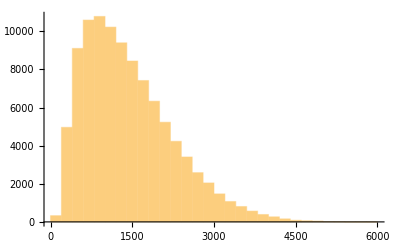

5814

```mathematica
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format3//Max
```

```mathematica
StringSplit@TrainSet$5vars$535355$CommonSet$format3$reduced⟦1⟧
```

{+,*,P,1,2,5,*,^,a2,P,6,^,a3,P,3,+,*,P,1,0,0,*,^,a0,P,3,*,^,a1,P,2,*,^,a2,P,3,a4,+,*,P,3,0,0,*,^,a0,P,2,*,^,a1,P,3,*,^,a2,P,2,*,a3,a4,+,*,P,1,0,0,*,^,a0,P,2,*,^,a1,P,2,*,^,a2,P,3,*,a3,a4,+,*,P,2,2,5,*,a0,*,^,a1,P,4,*,a2,*,^,a3,P,2,a4,+,*,N,4,0,0,*,^,a0,P,2,*,^,a2,P,4,*,^,a3,P,2,a4,+,*,P,5,0,0,*,^,a0,P,2,*,^,a2,P,4,*,a3,^,a4,P,2,+,*,P,2,0,0,*,a0,*,^,a2,P,4,*,^,a3,P,2,^,a4,P,2,+,*,N,2,0,0,*,^,a0,P,2,*,a1,*,^,a2,P,2,^,a4,P,4,+,*,N,3,0,0,*,a0,*,^,a1,P,2,*,a2,*,a3,^,a4,P,4,*,P,1,0,0,*,a0,*,a2,^,a4,P,7,?,+,*,N,4,*,b0,^,b1,P,2,+,^,b1,P,3,+,*,N,4,*,b1,*,b2,b4,+,*,N,5,*,^,b3,P,2,b4,*,P,4,*,b1,^,b4,P,2,&,*,P,4,*,^,a0,P,2,a4,&,*,P,5,*,^,a2,P,2,a3,&,+,*,a0,^,a1,P,2,*,P,2,*,a2,*,a3,a4,&,+,*,N,2,*,a0,*,a1,a2,+,*,N,3,*,^,a1,P,2,a3,*,P,2,^,a4,P,3,&,*,N,5,*,a0,*,a2,a4}

99961

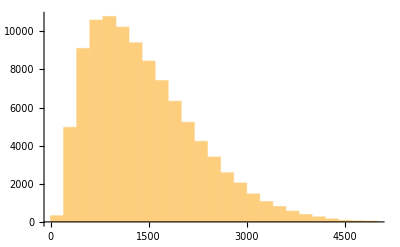

4993

```mathematica
TrainSet$5vars$535355$CommonSet$format3$reduced=Select[TrainSet$5vars$535355$CommonSet$format3,Length[StringSplit[#]]<5000&];
Length[%]
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_5var1.txt",TrainSet$5vars$535355$CommonSet$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_5var1.txt",TrainSet$5vars$535355$CommonSet$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_5var1.txt",TrainSet$5vars$535355$CommonSet$format3$reduced⟦3129;;99961⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_5var1.txt

../../dataset_storage/datasets/multi/test_set_5var1.txt

../../dataset_storage/datasets/multi/train_set_5var1.txt

#### in a format 4 (base10)

```mathematica
Get["MMA2TxtFormat4.m"];
```

```mathematica
GenerateTrainSet$5vars$535355$CommonSet$format4[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5vars$535355$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5vars$535355$CommonSet$format4=GenerateTrainSet$5vars$535355$CommonSet$format4[100000];
```

```mathematica
TrainSet$5vars$535355$CommonSet$format4⟦1⟧
```

+ * P 1 25 * ^ a2 P 6 ^ a3 P 3 + * P 1 0 * ^ a0 P 3 * ^ a1 P 2 * ^ a2 P 3 a4 + * P 3 0 * ^ a0 P 2 * ^ a1 P 3 * ^ a2 P 2 * a3 a4 + * P 1 0 * ^ a0 P 2 * ^ a1 P 2 * ^ a2 P 3 * a3 a4 + * P 2 25 * a0 * ^ a1 P 4 * a2 * ^ a3 P 2 a4 + * N 4 0 * ^ a0 P 2 * ^ a2 P 4 * ^ a3 P 2 a4 + * P 5 0 * ^ a0 P 2 * ^ a2 P 4 * a3 ^ a4 P 2 + * P 2 0 * a0 * ^ a2 P 4 * ^ a3 P 2 ^ a4 P 2 + * N 2 0 * ^ a0 P 2 * a1 * ^ a2 P 2 ^ a4 P 4 + * N 3 0 * a0 * ^ a1 P 2 * a2 * a3 ^ a4 P 4 * P 1 0 * a0 * a2 ^ a4 P 7 ? + * N 4 * b N 0 ^ b P 1 P 2 + ^ b P 1 P 3 + * N 4 * b P 1 * b P 2 b P 4 + * N 5 * ^ b P 3 P 2 b P 4 * P 4 * b P 1 ^ b P 4 P 2 & * P 4 * ^ a0 P 2 a4 & * P 5 * ^ a2 P 2 a3 & + * a0 ^ a1 P 2 * P 2 * a2 * a3 a4 & + * N 2 * a0 * a1 a2 + * N 3 * ^ a1 P 2 a3 * P 2 ^ a4 P 3 & * N 5 * a0 * a2 a4

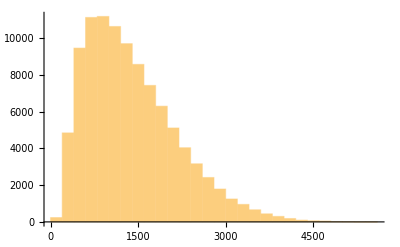

5578

```mathematica
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format4//Histogram
Length/@StringSplit/@TrainSet$5vars$535355$CommonSet$format4//Max
```

#### 5353 3terms, 3terms in format 3 ( Exp 60, 5var2 )

```mathematica
GenerateTrainSet$5vars$535333$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$5vars$535333$CommonSet = GenerateTrainSet$5vars$535333$CommonSet[100000];
TrainSet$5vars$535333$CommonSet = DeleteDuplicates[TrainSet$5vars$535333$CommonSet];
Length[TrainSet$5vars$535333$CommonSet]
```

100000

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$5vars$535333$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5vars$535333$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5vars$535333$CommonSet$format3=GenerateTrainSet$5vars$535333$CommonSet$format3[100000];
```

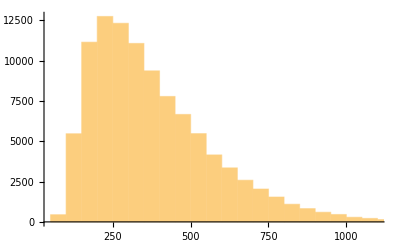

1513

```mathematica
Length/@StringSplit/@TrainSet$5vars$535333$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$5vars$535333$CommonSet$format3//Max
```

```mathematica
TrainSet$5vars$535333$CommonSet$format3$reduced=Select[TrainSet$5vars$535333$CommonSet$format3,Length[StringSplit[#]]<1300&];
Length[%]
```

99962

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_5var2.txt",TrainSet$5vars$535333$CommonSet$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_5var2.txt",TrainSet$5vars$535333$CommonSet$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_5var2.txt",TrainSet$5vars$535333$CommonSet$format3$reduced⟦3129;;99962⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_5var2.txt

../../dataset_storage/datasets/multi/test_set_5var2.txt

../../dataset_storage/datasets/multi/train_set_5var2.txt

#### 5351 9terms, 5terms in format 3 ( Exp 61, 5var3 )

```mathematica
(* both original and substitution has fixed degree terms / original has a fixed number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5vars$535195$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,1,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},9,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$5vars$535195$CommonSet[5]//TableForm
```

-57 a[0]^3-608 a[0]^2 a[1]-1405 a[0] a[1]^2-860 a[1]^3+72 a[0]^2 a[2]+605 a[0] a[1] a[2]+755 a[1]^2 a[2]-15 a[0] a[2]^2-135 a[1] a[2]^2-101 a[0]^2 a[3]-635 a[0] a[1] a[3]-413 a[1]^2 a[3]+175 a[0] a[2] a[3]+334 a[1] a[2] a[3]-28 a[2]^2 a[3]+76 a[0] a[3]^2-223 a[1] a[3]^2+62 a[2] a[3]^2+58 a[3]^3+212 a[0]^2 a[4]+640 a[0] a[1] a[4]+696 a[1]^2 a[4]-220 a[0] a[2] a[4]-448 a[1] a[2] a[4]+56 a[2]^2 a[4]+224 a[0] a[3] a[4]-112 a[1] a[3] a[4]-132 a[2] a[3] a[4]-76 a[3]^2 a[4]-16 a[0] a[4]^2-224 a[1] a[4]^2+16 a[2] a[4]^2-80 a[3] a[4]^2 | 2 b[0]^2 b[1]-2 b[0] b[2]^2-3 b[0] b[1] b[3]-4 b[2]^2 b[3]+5 b[1] b[3]^2-4 b[2] b[3]^2+2 b[1]^2 b[4]-5 b[2] b[3] b[4]+2 b[1] b[4]^2 | a[3] | a[0]-5 a[1] | 2 a[0]+5 a[1]+2 a[3]-4 a[4] | -3 a[0]-4 a[1]+a[2]-3 a[3] | -3 a[0]-3 a[1]+2 a[2]+3 a[3]+4 a[4]
62 a[0]^2 a[1]-129 a[0] a[1]^2+48 a[1]^3-20 a[0]^2 a[2]-36 a[0] a[1] a[2]+81 a[1]^2 a[2]+40 a[0] a[2]^2+14 a[1] a[2]^2-36 a[2]^3+10 a[0]^2 a[3]-310 a[0] a[1] a[3]+320 a[1]^2 a[3]+100 a[0] a[2] a[3]+150 a[1] a[2] a[3]-150 a[2]^2 a[3]-25 a[0] a[3]^2+400 a[1] a[3]^2-175 a[2] a[3]^2+6 a[0]^2 a[4]+246 a[0] a[1] a[4]-260 a[1]^2 a[4]-84 a[0] a[2] a[4]-34 a[1] a[2] a[4]+70 a[2]^2 a[4]+50 a[0] a[3] a[4]-600 a[1] a[3] a[4]+170 a[2] a[3] a[4]-100 a[3]^2 a[4]+39 a[0] a[4]^2+248 a[1] a[4]^2-93 a[2] a[4]^2+40 a[3] a[4]^2+60 a[4]^3 | -b[0]^3-4 b[0] b[1] b[2]-3 b[1]^2 b[2]+5 b[1] b[2]^2+b[0] b[3]^2-2 b[1] b[3]^2-b[1] b[2] b[4]-4 b[2]^2 b[4]+2 b[2] b[4]^2 | -a[0]-a[2]-4 a[4] | 2 a[2] | -2 a[0]+a[1]+2 a[2]+5 a[3]-4 a[4] | -a[0]-a[1]+3 a[2]+5 a[3]-a[4] | -4 a[1]+3 a[2]
156 a[0]^3-154 a[0]^2 a[1]+105 a[0] a[1]^2+a[1]^3-108 a[0]^2 a[2]+28 a[0] a[1] a[2]-6 a[0] a[2]^2-4 a[1] a[2]^2-162 a[0]^2 a[3]+440 a[0] a[1] a[3]-96 a[1]^2 a[3]+84 a[0] a[2] a[3]-16 a[1] a[2] a[3]-6 a[2]^2 a[3]+186 a[0] a[3]^2-268 a[1] a[3]^2+60 a[2] a[3]^2-55 a[3]^3-138 a[0]^2 a[4]-14 a[0] a[1] a[4]-96 a[1]^2 a[4]+24 a[0] a[2] a[4]-44 a[1] a[2] a[4]-6 a[2]^2 a[4]-456 a[0] a[3] a[4]-40 a[1] a[3] a[4]+96 a[2] a[3] a[4]+390 a[3]^2 a[4]+15 a[0] a[4]^2+179 a[1] a[4]^2+36 a[2] a[4]^2+516 a[3] a[4]^2-54 a[4]^3 | -4 b[0] b[1] b[2]+2 b[1]^2 b[2]+b[2]^3+2 b[1] b[3]^2-b[0]^2 b[4]-4 b[0] b[1] b[4]+b[4]^3 | -a[0]+2 a[2]-2 a[3]+5 a[4] | 3 a[0]-3 a[3]-3 a[4] | 5 a[3] | -4 a[0]+4 a[1]+a[2]+5 a[3]-3 a[4] | 3 a[0]+a[1]
4 a[0]^3-10 a[0]^2 a[2]+50 a[0] a[2]^2-975 a[2]^3-150 a[0] a[2] a[3]+225 a[2]^2 a[3]-22 a[0]^2 a[4]-208 a[0] a[2] a[4]-375 a[2]^2 a[4]+18 a[0] a[3] a[4]+54 a[0] a[4]^2-495 a[2] a[4]^2-135 a[3] a[4]^2-315 a[4]^3 | 4 b[0]^3+2 b[0]^2 b[1]+4 b[0] b[2]^2-3 b[1] b[2] b[3]-2 b[2]^2 b[4]-2 b[0] b[3] b[4]+3 b[2] b[3] b[4]-3 b[3] b[4]^2-4 b[4]^3 | -a[0]+3 a[4] | 4 a[0]-5 a[2]-5 a[4] | 5 a[2] | -3 a[2]+3 a[3]+5 a[4] | 5 a[2]+3 a[4]
-825 a[0]^3+150 a[0]^2 a[1]-1820 a[0]^2 a[2]+240 a[0] a[1] a[2]-1328 a[0] a[2]^2+96 a[1] a[2]^2-320 a[2]^3+1912 a[0]^2 a[3]+27 a[0] a[1] a[3]-27 a[1]^2 a[3]+3068 a[0] a[2] a[3]-36 a[1] a[2] a[3]+1200 a[2]^2 a[3]-1610 a[0] a[3]^2-105 a[1] a[3]^2-1380 a[2] a[3]^2+475 a[3]^3-2233 a[0]^2 a[4]+647 a[0] a[1] a[4]-59 a[1]^2 a[4]-2908 a[0] a[2] a[4]+396 a[1] a[2] a[4]-960 a[2]^2 a[4]+3528 a[0] a[3] a[4]-203 a[1] a[3] a[4]+2604 a[2] a[3] a[4]-1511 a[3]^2 a[4]-1605 a[0] a[4]^2+404 a[1] a[4]^2-876 a[2] a[4]^2+1525 a[3] a[4]^2-136 a[4]^3 | -5 b[0]^3-b[1] b[2]^2-2 b[0]^2 b[3]-b[0] b[1] b[4]+5 b[0] b[2] b[4]+5 b[1] b[2] b[4]-b[0] b[3] b[4]+b[3]^2 b[4]+4 b[1] b[4]^2 | 5 a[0]+4 a[2]-5 a[3]+4 a[4] | 2 a[4] | 5 a[0]-4 a[1]-2 a[3]-a[4] | 4 a[0]-3 a[1] | -3 a[3]-3 a[4]

```mathematica
TrainSet$5vars$535195$CommonSet = GenerateTrainSet$5vars$535195$CommonSet[410000];
TrainSet$5vars$535195$CommonSet = DeleteDuplicates[TrainSet$5vars$535195$CommonSet];
Length[TrainSet$5vars$535195$CommonSet]
```

410000

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$5vars$535195$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5vars$535195$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5vars$535195$CommonSet$format3=GenerateTrainSet$5vars$535195$CommonSet$format3[410000];
```

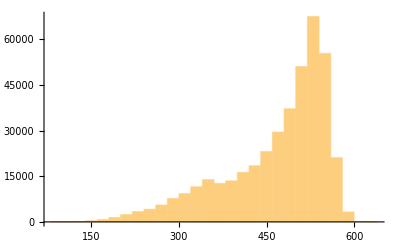

623

```mathematica
Length/@StringSplit/@TrainSet$5vars$535195$CommonSet$format3;
%//Histogram
%%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_5var3.txt",TrainSet$5vars$535195$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_5var3.txt",TrainSet$5vars$535195$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_5var3.txt",TrainSet$5vars$535195$CommonSet$format3⟦3129;;403128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_5var3.txt

../../dataset_storage/datasets/multi/test_set_5var3.txt

../../dataset_storage/datasets/multi/train_set_5var3.txt

#### 5351 10terms, 5terms in format 3 ( Exp 62, 63, 5var4 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5var4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly7$LSS[5,3,5,1,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},10,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$5var4$CommonSet[5]//TableForm
```

48 a[0]^3+292 a[0]^2 a[1]+263 a[0] a[1]^2+57 a[1]^3+301 a[0]^2 a[2]+873 a[0] a[1] a[2]+370 a[1]^2 a[2]+544 a[0] a[2]^2+644 a[1] a[2]^2+304 a[2]^3-300 a[0]^2 a[3]-732 a[0] a[1] a[3]-295 a[1]^2 a[3]-1014 a[0] a[2] a[3]-1069 a[1] a[2] a[3]-816 a[2]^2 a[3]+456 a[0] a[3]^2+440 a[1] a[3]^2+713 a[2] a[3]^2-204 a[3]^3-106 a[0]^2 a[4]-688 a[0] a[1] a[4]-330 a[1]^2 a[4]-573 a[0] a[2] a[4]-1043 a[1] a[2] a[4]-572 a[2]^2 a[4]+624 a[0] a[3] a[4]+884 a[1] a[3] a[4]+1117 a[2] a[3] a[4]-518 a[3]^2 a[4]+29 a[0] a[4]^2+399 a[1] a[4]^2+232 a[2] a[4]^2-301 a[3] a[4]^2+36 a[4]^3 | -b[2] b[3]^2-3 b[2]^2 b[4]+b[2] b[3] b[4] | 4 a[1]-4 a[2]-2 a[3]-a[4] | a[0]-3 a[1]+2 a[2]+4 a[3]+4 a[4] | -3 a[0]-a[1]-4 a[2]+3 a[3]+4 a[4] | 4 a[0]+5 a[1]+5 a[2]-4 a[3]-5 a[4] | -4 a[1]-3 a[2]+4 a[3]-2 a[4]
44 a[0]^3-184 a[0]^2 a[1]-92 a[0] a[1]^2+318 a[1]^3+124 a[0]^2 a[2]+224 a[0] a[1] a[2]-794 a[1]^2 a[2]-117 a[0] a[2]^2+654 a[1] a[2]^2-178 a[2]^3-180 a[0]^2 a[3]+520 a[0] a[1] a[3]+430 a[1]^2 a[3]-340 a[0] a[2] a[3]-820 a[1] a[2] a[3]+375 a[2]^2 a[3]+180 a[0] a[3]^2-310 a[1] a[3]^2+190 a[2] a[3]^2+10 a[3]^3-316 a[0]^2 a[4]-216 a[0] a[1] a[4]+1096 a[1]^2 a[4]+286 a[0] a[2] a[4]-1832 a[1] a[2] a[4]+756 a[2]^2 a[4]+1060 a[0] a[3] a[4]+1080 a[1] a[3] a[4]-1070 a[2] a[3] a[4]-880 a[3]^2 a[4]-217 a[0] a[4]^2+1204 a[1] a[4]^2-1004 a[2] a[4]^2+905 a[3] a[4]^2+372 a[4]^3 | -2 b[1]^3+5 b[0] b[2]^2 | 3 a[0]+4 a[1]-4 a[2]-3 a[3]+4 a[4] | 2 a[0]+a[1]-a[2]-5 a[3]+4 a[4] | -2 a[0]+4 a[1]-3 a[2]+4 a[3]+5 a[4] | -2 a[0]+a[1]-5 a[3]+2 a[4] | 3 a[0]-2 a[1]-2 a[2]-2 a[3]
-53 a[0]^3+124 a[0]^2 a[1]+58 a[0] a[1]^2+48 a[1]^3+328 a[0]^2 a[2]+330 a[0] a[1] a[2]-25 a[1]^2 a[2]-112 a[0] a[2]^2+51 a[1] a[2]^2+19 a[2]^3-196 a[0]^2 a[3]+538 a[0] a[1] a[3]+321 a[1]^2 a[3]+1030 a[0] a[2] a[3]-134 a[1] a[2] a[3]-215 a[2]^2 a[3]+1362 a[0] a[3]^2+343 a[1] a[3]^2-555 a[2] a[3]^2-321 a[3]^3+326 a[0]^2 a[4]+16 a[0] a[1] a[4]-175 a[1]^2 a[4]-715 a[0] a[2] a[4]+82 a[1] a[2] a[4]+146 a[2]^2 a[4]-51 a[0] a[3] a[4]-534 a[1] a[3] a[4]-92 a[2] a[3] a[4]-446 a[3]^2 a[4]-355 a[0] a[4]^2+164 a[1] a[4]^2+201 a[2] a[4]^2+209 a[3] a[4]^2+40 a[4]^3 | -2 b[0] b[1]^2+4 b[1]^3+5 b[1] b[2]^2-b[0]^2 b[3]-2 b[1]^2 b[3]-5 b[1] b[3]^2+5 b[3]^3+b[1]^2 b[4]-3 b[2] b[3] b[4]+b[0] b[4]^2 | -5 a[0]+3 a[1]+5 a[2]+3 a[3]+5 a[4] | a[0]+3 a[1]+4 a[3]-2 a[4] | -4 a[0]-2 a[2]-a[4] | 3 a[0]-2 a[2]-4 a[3]-a[4] | -3 a[0]-2 a[1]+3 a[2]-5 a[3]+4 a[4]
-2 a[0] a[1]^2+2 a[1]^3-16 a[0] a[1] a[2]+13 a[1]^2 a[2]-32 a[0] a[2]^2+8 a[1] a[2]^2-48 a[2]^3-20 a[0] a[1] a[3]+23 a[1]^2 a[3]-80 a[0] a[2] a[3]+74 a[1] a[2] a[3]-72 a[2]^2 a[3]-50 a[0] a[3]^2+80 a[1] a[3]^2+45 a[2] a[3]^2+75 a[3]^3+4 a[0] a[1] a[4]-4 a[1]^2 a[4]+16 a[0] a[2] a[4]-10 a[1] a[2] a[4]+24 a[2]^2 a[4]+20 a[0] a[3] a[4]-26 a[1] a[3] a[4]+6 a[2] a[3] a[4]-30 a[3]^2 a[4]-2 a[0] a[4]^2+2 a[1] a[4]^2-3 a[2] a[4]^2+3 a[3] a[4]^2 | -b[3]^2 b[4] | -5 a[0]+a[1]-a[2]-2 a[3]-4 a[4] | 3 a[0]+a[1]+3 a[2]-2 a[3]+4 a[4] | -2 a[0]+a[2]-2 a[3]+a[4] | a[1]+4 a[2]+5 a[3]-a[4] | 2 a[0]-2 a[1]+3 a[2]-3 a[3]
85 a[0]^3+332 a[0]^2 a[1]+530 a[0] a[1]^2+321 a[1]^3+78 a[0]^2 a[2]+72 a[0] a[1] a[2]+21 a[1]^2 a[2]+27 a[0] a[2]^2+135 a[1] a[2]^2+135 a[2]^3-218 a[0]^2 a[3]-652 a[0] a[1] a[3]-595 a[1]^2 a[3]-36 a[0] a[2] a[3]-162 a[1] a[2] a[3]-333 a[2]^2 a[3]+194 a[0] a[3]^2+407 a[1] a[3]^2+249 a[2] a[3]^2-133 a[3]^3+222 a[0]^2 a[4]+624 a[0] a[1] a[4]+518 a[1]^2 a[4]+60 a[0] a[2] a[4]+12 a[1] a[2] a[4]-36 a[2]^2 a[4]-384 a[0] a[3] a[4]-620 a[1] a[3] a[4]+36 a[2] a[3] a[4]+174 a[3]^2 a[4]+152 a[0] a[4]^2+268 a[1] a[4]^2-60 a[2] a[4]^2-140 a[3] a[4]^2+8 a[4]^3 | -4 b[1]^2 b[3]-b[3]^3-b[2] b[4]^2 | -5 a[0]-4 a[1]+3 a[2]-a[3]-4 a[4] | 2 a[0]+3 a[1]-3 a[2]+2 a[4] | -5 a[0]-4 a[1]+2 a[3]+2 a[4] | -2 a[0]-5 a[1]-3 a[2]+5 a[3]-2 a[4] | -3 a[0]-2 a[1]-3 a[2]+2 a[3]-4 a[4]

```mathematica
TrainSet$5var4$CommonSet = GenerateTrainSet$5var4$CommonSet[410000];
```

410000

```mathematica
TrainSet$5var4$CommonSet = DeleteDuplicatesBy[TrainSet$5var4$CommonSet,First];
Length[TrainSet$5var4$CommonSet]
```

409957

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$5var4$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5var4$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5var4$CommonSet$format3=GenerateTrainSet$5var4$CommonSet$format3[409957];
```

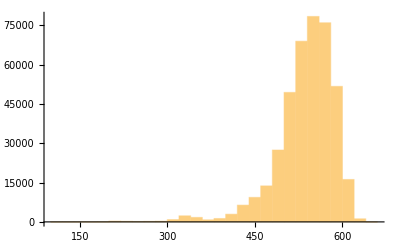

642

```mathematica
Length/@StringSplit/@TrainSet$5var4$CommonSet$format3;
%//Histogram
%%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_5var4.txt",TrainSet$5var4$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_5var4.txt",TrainSet$5var4$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_5var4.txt",TrainSet$5var4$CommonSet$format3⟦3129;;403128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_5var4.txt

../../dataset_storage/datasets/multi/test_set_5var4.txt

../../dataset_storage/datasets/multi/train_set_5var4.txt

#### 5351 5terms, 5terms in format 3 ( Exp 64, 5var5 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$5var5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly7$LSS[5,3,5,1,{b[0],b[1],b[2],b[3],b[4]},{a[0],a[1],a[2],a[3],a[4]},10,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$5var5$CommonSet[5]//TableForm
```

-175 a[0]^3+178 a[0]^2 a[1]-45 a[0] a[1]^2-2 a[1]^3-124 a[0]^2 a[2]+91 a[0] a[1] a[2]+39 a[1]^2 a[2]-379 a[0] a[2]^2-90 a[1] a[2]^2+76 a[2]^3+89 a[0]^2 a[3]-113 a[0] a[1] a[3]+48 a[1]^2 a[3]-1094 a[0] a[2] a[3]+275 a[1] a[2] a[3]-839 a[2]^2 a[3]-67 a[0] a[3]^2+61 a[1] a[3]^2-438 a[2] a[3]^2-271 a[3]^3-312 a[0]^2 a[4]+264 a[0] a[1] a[4]-8 a[1]^2 a[4]-811 a[0] a[2] a[4]-171 a[1] a[2] a[4]+424 a[2]^2 a[4]-981 a[0] a[3] a[4]+295 a[1] a[3] a[4]-1163 a[2] a[3] a[4]-599 a[3]^2 a[4]-338 a[0] a[4]^2-82 a[1] a[4]^2+208 a[2] a[4]^2-426 a[3] a[4]^2+24 a[4]^3 | -4 b[0] b[1]^2+b[1]^3+2 b[1]^2 b[3]+3 b[0] b[2] b[3]-b[1] b[2] b[3]-3 b[1]^2 b[4]-2 b[0] b[3] b[4] | 4 a[0]-2 a[1]-3 a[2]+4 a[3] | a[0]-a[1]+5 a[2]+3 a[3]+4 a[4] | -4 a[0]+5 a[1]-4 a[2]+2 a[3]+a[4] | 2 a[0]-a[2]-5 a[3]+2 a[4] | 4 a[0]+3 a[1]+3 a[2]+2 a[3]+2 a[4]
559 a[0]^3+2029 a[0]^2 a[1]+2415 a[0] a[1]^2+940 a[1]^3+1205 a[0]^2 a[2]+2018 a[0] a[1] a[2]+964 a[1]^2 a[2]+207 a[0] a[2]^2+570 a[1] a[2]^2+251 a[2]^3+643 a[0]^2 a[3]+874 a[0] a[1] a[3]+395 a[1]^2 a[3]-866 a[0] a[2] a[3]+254 a[1] a[2] a[3]+679 a[2]^2 a[3]-756 a[0] a[3]^2-39 a[1] a[3]^2+1031 a[2] a[3]^2+520 a[3]^3+382 a[0]^2 a[4]+1058 a[0] a[1] a[4]+502 a[1]^2 a[4]+222 a[0] a[2] a[4]-164 a[1] a[2] a[4]+378 a[2]^2 a[4]+420 a[0] a[3] a[4]-46 a[1] a[3] a[4]+758 a[2] a[3] a[4]+288 a[3]^2 a[4]-23 a[0] a[4]^2-260 a[1] a[4]^2-818 a[2] a[4]^2-775 a[3] a[4]^2+6 a[4]^3 | 3 b[0]^2 b[2]+3 b[0] b[1] b[2]+5 b[1]^2 b[2]+2 b[0] b[1] b[3]+3 b[1]^2 b[3]-5 b[0] b[2] b[3]-3 b[2]^2 b[4]-4 b[2] b[3] b[4]+2 b[3] b[4]^2 | -2 a[0]-a[1]+3 a[2]+3 a[3]+a[4] | -2 a[0]-4 a[1]-a[2]-2 a[3]-2 a[4] | a[0]+4 a[1]+4 a[2]+5 a[3]+2 a[4] | 5 a[0]+4 a[1]-a[2]-5 a[3]+4 a[4] | -5 a[0]-2 a[1]-4 a[2]+5 a[4]
-96 a[0]^3+176 a[0]^2 a[1]+10 a[0] a[1]^2-100 a[1]^3-352 a[0]^2 a[2]+512 a[0] a[1] a[2]-90 a[1]^2 a[2]-416 a[0] a[2]^2+336 a[1] a[2]^2-160 a[2]^3-64 a[0]^2 a[3]+344 a[0] a[1] a[3]-330 a[1]^2 a[3]-64 a[0] a[2] a[3]+264 a[1] a[2] a[3]+136 a[0] a[3]^2-216 a[1] a[3]^2+120 a[2] a[3]^2-40 a[3]^3-96 a[0]^2 a[4]+56 a[0] a[1] a[4]+80 a[1]^2 a[4]-256 a[0] a[2] a[4]+136 a[1] a[2] a[4]-160 a[2]^2 a[4]-112 a[0] a[3] a[4]+232 a[1] a[3] a[4]-80 a[2] a[3] a[4]+80 a[3]^2 a[4]-24 a[0] a[4]^2-16 a[1] a[4]^2-40 a[2] a[4]^2-40 a[3] a[4]^2 | -2 b[0]^2 b[2] | 4 a[0]-5 a[1]+4 a[2]-2 a[3]+2 a[4] | -2 a[0]-3 a[1]-a[2]+2 a[3]-5 a[4] | 3 a[0]+2 a[1]+5 a[2]+5 a[3] | 5 a[0]+3 a[1]-3 a[2]+5 a[3]+5 a[4] | -5 a[0]-a[1]-5 a[2]-2 a[4]
161 a[0]^3+666 a[0]^2 a[1]+669 a[0] a[1]^2-200 a[1]^3+794 a[0]^2 a[2]+1670 a[0] a[1] a[2]+668 a[1]^2 a[2]+1008 a[0] a[2]^2+1026 a[1] a[2]^2+378 a[2]^3+367 a[0]^2 a[3]+730 a[0] a[1] a[3]+37 a[1]^2 a[3]+1130 a[0] a[2] a[3]+742 a[1] a[2] a[3]+660 a[2]^2 a[3]+268 a[0] a[3]^2+80 a[1] a[3]^2+356 a[2] a[3]^2+62 a[3]^3-1131 a[0]^2 a[4]-2691 a[0] a[1] a[4]-534 a[1]^2 a[4]-2950 a[0] a[2] a[4]-3131 a[1] a[2] a[4]-1822 a[2]^2 a[4]-1547 a[0] a[3] a[4]-1153 a[1] a[3] a[4]-1773 a[2] a[3] a[4]-452 a[3]^2 a[4]+2283 a[0] a[4]^2+2076 a[1] a[4]^2+2869 a[2] a[4]^2+1307 a[3] a[4]^2-1417 a[4]^3 | -5 b[0]^2 b[1]+5 b[0] b[1] b[2]-4 b[1] b[2]^2+4 b[0]^2 b[3]+b[0] b[1] b[3]+b[1]^2 b[3]-3 b[1] b[2] b[3]-b[3]^3-3 b[0] b[2] b[4]+2 b[2] b[3] b[4] | -3 a[1]-a[2]+a[3]+4 a[4] | -4 a[0]+a[1]-4 a[2]-a[3]+5 a[4] | 4 a[0]+5 a[1]+3 a[2]+5 a[3]-5 a[4] | -a[0]-2 a[1]+2 a[2]-a[3]+a[4] | 4 a[0]+2 a[1]+2 a[2]-4 a[4]
-510 a[0]^3+1170 a[0]^2 a[1]+1552 a[0] a[1]^2+199 a[1]^3+1296 a[0]^2 a[2]+3080 a[0] a[1] a[2]+263 a[1]^2 a[2]+1426 a[0] a[2]^2-161 a[1] a[2]^2-235 a[2]^3+167 a[0]^2 a[3]-2676 a[0] a[1] a[3]-1412 a[1]^2 a[3]-2945 a[0] a[2] a[3]-2444 a[1] a[2] a[3]-1002 a[2]^2 a[3]+544 a[0] a[3]^2+1617 a[1] a[3]^2+1549 a[2] a[3]^2-415 a[3]^3+1046 a[0]^2 a[4]-532 a[0] a[1] a[4]+513 a[1]^2 a[4]-732 a[0] a[2] a[4]+522 a[1] a[2] a[4]+195 a[2]^2 a[4]-941 a[0] a[3] a[4]-1144 a[1] a[3] a[4]-361 a[2] a[3] a[4]+887 a[3]^2 a[4]+112 a[0] a[4]^2+1785 a[1] a[4]^2+1363 a[2] a[4]^2-1058 a[3] a[4]^2-41 a[4]^3 | -4 b[1]^2 b[2]+3 b[2]^3+3 b[0]^2 b[3]-4 b[3]^3-5 b[0] b[1] b[4]+4 b[0] b[2] b[4]+2 b[3] b[4]^2 | -4 a[0]+4 a[1]+4 a[2]+a[3] | 3 a[0]+4 a[1]+4 a[2]-3 a[3]-5 a[4] | -4 a[0]+a[1]-a[2]+5 a[4] | -3 a[0]-5 a[1]-4 a[2]+5 a[3]-3 a[4] | -3 a[0]+3 a[2]+2 a[3]+2 a[4]

```mathematica
TrainSet$5var5$CommonSet = GenerateTrainSet$5var5$CommonSet[410000];
```

```mathematica
TrainSet$5var5$CommonSet = DeleteDuplicatesBy[TrainSet$5var5$CommonSet,First];
Length[TrainSet$5var5$CommonSet]
```

409972

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$5var5$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4,sub5}=TrainSet$5var5$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]<>" & "<>MMAExprToJFString[sub5]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$5var5$CommonSet$format3=GenerateTrainSet$5var5$CommonSet$format3[409972];
```

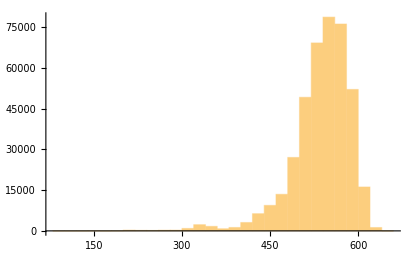

643

```mathematica
Length/@StringSplit/@TrainSet$5var5$CommonSet$format3;
%//Histogram
%%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_5var5.txt",TrainSet$5var5$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_5var5.txt",TrainSet$5var5$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_5var5.txt",TrainSet$5var5$CommonSet$format3⟦3129;;403128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_5var5.txt

../../dataset_storage/datasets/multi/test_set_5var5.txt

../../dataset_storage/datasets/multi/train_set_5var5.txt

### Four-variable polynomial experiment ( extension of exp 45 )

#### 5351 4terms, 4terms in format 3 ( Exp 65, 4var1 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$4var1$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly7$LSS[5,3,5,1,{b[0],b[1],b[2],b[3]},{a[0],a[1],a[2],a[3]},4,4],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$4var1$CommonSet[5]//TableForm
```

623 a[0]^3+744 a[0]^2 a[1]+294 a[0] a[1]^2+38 a[1]^3+1155 a[0]^2 a[2]+960 a[0] a[1] a[2]+210 a[1]^2 a[2]+525 a[0] a[2]^2+120 a[1] a[2]^2+385 a[2]^3+18 a[0]^2 a[3]+36 a[0] a[1] a[3]+18 a[1]^2 a[3]-180 a[0] a[2] a[3]-180 a[1] a[2] a[3]+450 a[2]^2 a[3]-54 a[0] a[3]^2-54 a[1] a[3]^2+270 a[2] a[3]^2+54 a[3]^3 | 5 b[0]^3-2 b[2]^3 | 5 a[0]+2 a[1]+3 a[2] | 4 a[0]+4 a[1]-a[2]+2 a[3] | a[0]+a[1]-5 a[2]-3 a[3] | -2 a[0]-a[1]+2 a[2]-3 a[3]
16 a[0]^3-88 a[0]^2 a[1]+160 a[0] a[1]^2-96 a[1]^3-72 a[0]^2 a[2]+248 a[0] a[1] a[2]-208 a[1]^2 a[2]+60 a[0] a[2]^2-70 a[1] a[2]^2+50 a[2]^3+24 a[0]^2 a[3]-88 a[0] a[1] a[3]+80 a[1]^2 a[3]-72 a[0] a[2] a[3]+124 a[1] a[2] a[3]+30 a[2]^2 a[3]+12 a[0] a[3]^2-22 a[1] a[3]^2-18 a[2] a[3]^2+2 a[3]^3 | -2 b[1] b[3]^2 | 5 a[0]+a[1]-5 a[2]-a[3] | -2 a[0]+3 a[1]-a[2]-a[3] | -5 a[0]-2 a[1]-a[2]+5 a[3] | 2 a[0]-4 a[1]-5 a[2]+a[3]
35 a[0]^3+349 a[0]^2 a[1]-447 a[0] a[1]^2+135 a[1]^3+598 a[0]^2 a[2]+4 a[0] a[1] a[2]-210 a[1]^2 a[2]+991 a[0] a[2]^2-281 a[1] a[2]^2+428 a[2]^3-199 a[0]^2 a[3]+594 a[0] a[1] a[3]-279 a[1]^2 a[3]-154 a[0] a[2] a[3]+414 a[1] a[2] a[3]+65 a[2]^2 a[3]+228 a[0] a[3]^2-72 a[1] a[3]^2+96 a[2] a[3]^2+216 a[3]^3 | 4 b[1] b[2]^2+3 b[2] b[3]^2 | 3 a[0]+a[1]+a[2]+4 a[3] | -a[0]+4 a[1]+2 a[2]+2 a[3] | 5 a[0]-3 a[1]+4 a[2]+3 a[3] | 3 a[0]-a[1]+5 a[2]-4 a[3]
-240 a[0]^3+236 a[0]^2 a[1]+640 a[0] a[1]^2-700 a[1]^3-16 a[0]^2 a[2]-234 a[0] a[1] a[2]+370 a[1]^2 a[2]+44 a[0] a[2]^2-26 a[1] a[2]^2-4 a[2]^3+204 a[0]^2 a[3]+785 a[0] a[1] a[3]-1405 a[1]^2 a[3]-166 a[0] a[2] a[3]+465 a[1] a[2] a[3]-14 a[2]^2 a[3]+240 a[0] a[3]^2-931 a[1] a[3]^2+146 a[2] a[3]^2-204 a[3]^3 | 3 b[0] b[1] b[3]+3 b[1] b[2] b[3]+2 b[1] b[3]^2 | -5 a[0]+4 a[1]+2 a[2]+a[3] | -3 a[0]-5 a[1]+a[2]-3 a[3] | a[0]+2 a[1]+2 a[3] | -4 a[0]+5 a[1]-2 a[2]+4 a[3]
-240 a[0]^3+480 a[0]^2 a[1]-300 a[0] a[1]^2+60 a[1]^3-624 a[0]^2 a[2]+864 a[0] a[1] a[2]-276 a[1]^2 a[2]-528 a[0] a[2]^2+384 a[1] a[2]^2-144 a[2]^3+120 a[0]^2 a[3]-180 a[0] a[1] a[3]+60 a[1]^2 a[3]+192 a[0] a[2] a[3]-156 a[1] a[2] a[3]+72 a[2]^2 a[3]-15 a[0] a[3]^2+15 a[1] a[3]^2-9 a[2] a[3]^2 | -3 b[0] b[3]^2 | 5 a[0]-5 a[1]+3 a[2] | 2 a[1]-a[3] | -a[0]-4 a[1]-2 a[2]+4 a[3] | 4 a[0]-2 a[1]+4 a[2]-a[3]

```mathematica
TrainSet$4var1$CommonSet = GenerateTrainSet$4var1$CommonSet[810000];
```

```mathematica
TrainSet$4var1$CommonSet = DeleteDuplicatesBy[TrainSet$4var1$CommonSet,First];
Length[TrainSet$4var1$CommonSet]
```

797046

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$4var1$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4}=TrainSet$4var1$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$4var1$CommonSet$format3=GenerateTrainSet$4var1$CommonSet$format3[797046];
```

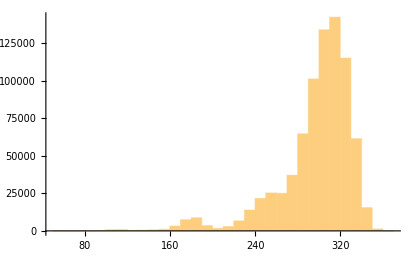

362

119

```mathematica
StringSplit/@TrainSet$4var1$CommonSet$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_4var1_2.txt",TrainSet$4var1$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_4var1_2.txt",TrainSet$4var1$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_4var1_2.txt",TrainSet$4var1$CommonSet$format3⟦3129;;793128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_4var1_2.txt

../../dataset_storage/datasets/multi/test_set_4var1_2.txt

../../dataset_storage/datasets/multi/train_set_4var1_2.txt

#### 5351 2terms, 4terms in format 3 ( Exp 66, 4var2 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$4var2$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly7$LSS[5,3,5,1,{b[0],b[1],b[2],b[3]},{a[0],a[1],a[2],a[3]},2,4],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$4var2$CommonSet[5]//TableForm
```

-8 a[0]^3-78 a[0]^2 a[1]-20 a[0] a[1]^2-19 a[1]^3-22 a[0]^2 a[2]-228 a[0] a[1] a[2]+25 a[1]^2 a[2]-20 a[0] a[2]^2-118 a[1] a[2]^2-34 a[2]^3-20 a[0]^2 a[3]+24 a[0] a[1] a[3]-4 a[1]^2 a[3]-24 a[0] a[2] a[3]+66 a[1] a[2] a[3]+72 a[2]^2 a[3]+4 a[0] a[3]^2+9 a[1] a[3]^2-11 a[2] a[3]^2+6 a[3]^3 | -b[0] b[1]^2-2 b[2]^2 b[3] | 4 a[0]+a[1]+a[2]-2 a[3] | -2 a[0]-3 a[1]-4 a[2]-a[3] | a[0]-a[1]+3 a[2]-a[3] | -4 a[0]+5 a[1]+a[2]-2 a[3]
168 a[0]^3+372 a[0]^2 a[1]+252 a[0] a[1]^2+48 a[1]^3-54 a[0]^2 a[2]+9 a[0] a[1] a[2]+60 a[1]^2 a[2]+27 a[0] a[2]^2+6 a[1] a[2]^2-6 a[2]^3-228 a[0]^2 a[3]-228 a[0] a[1] a[3]-12 a[1]^2 a[3]-57 a[0] a[2] a[3]-165 a[1] a[2] a[3]-3 a[2]^2 a[3]-48 a[0] a[3]^2-144 a[1] a[3]^2+111 a[2] a[3]^2+108 a[3]^3 | 3 b[0] b[1]^2-3 b[1] b[2] b[3] | 3 a[0]+a[1]+2 a[2]+2 a[3] | -4 a[0]-4 a[1]+a[2]+4 a[3] | -2 a[0]-a[1]+4 a[2]-a[3] | -a[0]+a[2]+a[3]
-90 a[0]^3+210 a[0]^2 a[1]+465 a[0] a[1]^2-225 a[1]^3+150 a[0]^2 a[2]+510 a[0] a[1] a[2]+105 a[1]^2 a[2]+195 a[0] a[2]^2+255 a[1] a[2]^2+45 a[2]^3+180 a[0]^2 a[3]+200 a[0] a[1] a[3]+490 a[1]^2 a[3]+280 a[0] a[2] a[3]+620 a[1] a[2] a[3]+30 a[2]^2 a[3]+136 a[0] a[3]^2+200 a[1] a[3]^2-168 a[2] a[3]^2-144 a[3]^3 | -2 b[0] b[1]^2+5 b[0] b[3]^2 | 3 a[0]+5 a[1]+a[2]-2 a[3] | -5 a[0]+5 a[1]-2 a[3] | -2 a[0]+a[1]-2 a[2]-2 a[3] | -2 a[0]-a[1]-3 a[2]-4 a[3]
-10 a[0]^3-65 a[0]^2 a[1]+140 a[0] a[1]^2-125 a[1]^3-35 a[0]^2 a[2]+410 a[0] a[1] a[2]-515 a[1]^2 a[2]+240 a[0] a[2]^2-720 a[1] a[2]^2-320 a[2]^3-140 a[0]^2 a[3]+40 a[0] a[1] a[3]-60 a[1]^2 a[3]+320 a[0] a[2] a[3]-160 a[1] a[2] a[3]-240 a[2]^2 a[3]-265 a[0] a[3]^2+75 a[1] a[3]^2+340 a[2] a[3]^2-85 a[3]^3 | -5 b[1]^3-5 b[2] b[3]^2 | -5 a[0]+4 a[1]-a[2] | -a[0]+3 a[1]+4 a[2]+a[3] | 3 a[0]-2 a[1]-5 a[2]+a[3] | a[0]+a[1]+4 a[3]
-8 a[0]^2 a[1]+10 a[0]^2 a[2]+80 a[0] a[1] a[2]-100 a[0] a[2]^2-200 a[1] a[2]^2+250 a[2]^3+4 a[0]^2 a[3]+16 a[0] a[1] a[3]-60 a[0] a[2] a[3]-80 a[1] a[2] a[3]+200 a[2]^2 a[3]-8 a[0] a[3]^2-8 a[1] a[3]^2+50 a[2] a[3]^2+4 a[3]^3 | 2 b[2]^2 b[3] | 5 a[0]-2 a[1]+4 a[2]+3 a[3] | a[0]+3 a[1]+4 a[2]-2 a[3] | -a[0]+5 a[2]+a[3] | -4 a[1]+5 a[2]+2 a[3]

```mathematica
TrainSet$4var2$CommonSet = GenerateTrainSet$4var2$CommonSet[10];
```

```mathematica
TrainSet$4var2$CommonSet = DeleteDuplicatesBy[TrainSet$4var2$CommonSet,First];
Length[TrainSet$4var2$CommonSet]
```

768592

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$4var2$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3,sub4}=TrainSet$4var2$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]<>" & "<>MMAExprToJFString[sub4]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$4var2$CommonSet$format3=GenerateTrainSet$4var2$CommonSet$format3[768592];
```

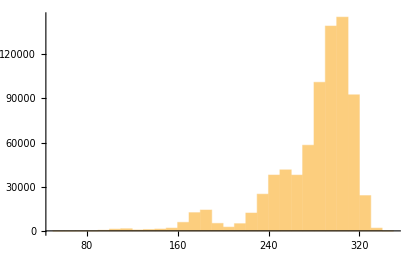

343

99

```mathematica
StringSplit/@TrainSet$4var2$CommonSet$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_4var2.txt",TrainSet$4var2$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_4var2.txt",TrainSet$4var2$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_4var2.txt",TrainSet$4var2$CommonSet$format3⟦3129;;763128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_4var2.txt

../../dataset_storage/datasets/multi/test_set_4var2.txt

../../dataset_storage/datasets/multi/train_set_4var2.txt

#### 5351 2vars for original 4terms, 4terms in format 3 ( Exp 69, 4var3 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$4var3$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly7$LSS[5,3,5,1,{b[0],b[1]},{a[0],a[1],a[2],a[3]},4,4],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$4var3$CommonSet[5]//TableForm
```

-144 a[0]^2 a[1]+48 a[0] a[1]^2+96 a[1]^3+108 a[0]^2 a[2]-240 a[0] a[1] a[2]-188 a[1]^2 a[2]+153 a[0] a[2]^2+71 a[1] a[2]^2+12 a[2]^3-72 a[0]^2 a[3]-480 a[0] a[1] a[3]+232 a[1]^2 a[3]+276 a[0] a[2] a[3]-628 a[1] a[2] a[3]+316 a[2]^2 a[3]-252 a[0] a[3]^2-324 a[1] a[3]^2+96 a[2] a[3]^2-208 a[3]^3 | 4 b[0]^2 b[1]+5 b[0] b[1]^2 | -3 a[0]+3 a[1]-4 a[2]-4 a[3] | -4 a[1]+3 a[2]-2 a[3]
-750 a[0]^3-300 a[0]^2 a[1]-840 a[0] a[1]^2-216 a[1]^3+1250 a[0]^2 a[2]-1000 a[0] a[1] a[2]+20 a[1]^2 a[2]-1250 a[0] a[2]^2+350 a[1] a[2]^2+375 a[2]^3-900 a[0]^2 a[3]-240 a[0] a[1] a[3]-336 a[1]^2 a[3]+1000 a[0] a[2] a[3]-400 a[1] a[2] a[3]-500 a[2]^2 a[3]-360 a[0] a[3]^2-48 a[1] a[3]^2+200 a[2] a[3]^2-48 a[3]^3 | 3 b[0]^3-b[0]^2 b[1]+b[0] b[1]^2+3 b[1]^3 | -5 a[0]-4 a[1]-2 a[3] | -5 a[0]+2 a[1]+5 a[2]-2 a[3]
-54 a[0]^3-216 a[0]^2 a[1]-288 a[0] a[1]^2-128 a[1]^3+270 a[0]^2 a[2]+720 a[0] a[1] a[2]+480 a[1]^2 a[2]-450 a[0] a[2]^2-600 a[1] a[2]^2+250 a[2]^3-108 a[0]^2 a[3]-288 a[0] a[1] a[3]-192 a[1]^2 a[3]+360 a[0] a[2] a[3]+480 a[1] a[2] a[3]-300 a[2]^2 a[3]-72 a[0] a[3]^2-96 a[1] a[3]^2+120 a[2] a[3]^2-16 a[3]^3 | 2 b[0]^3 | -3 a[0]-4 a[1]+5 a[2]-2 a[3] | -5 a[0]+a[1]-a[3]
-8 a[1]^3+24 a[1]^2 a[2]-24 a[1] a[2]^2+8 a[2]^3+36 a[1]^2 a[3]-72 a[1] a[2] a[3]+36 a[2]^2 a[3]-54 a[1] a[3]^2+54 a[2] a[3]^2+27 a[3]^3 | -b[0]^3 | 2 a[1]-2 a[2]-3 a[3] | a[0]+3 a[2]-2 a[3]
-211 a[0]^3-241 a[0]^2 a[1]-1783 a[0] a[1]^2+473 a[1]^3+268 a[0]^2 a[2]+844 a[0] a[1] a[2]+358 a[1]^2 a[2]-174 a[0] a[2]^2-216 a[1] a[2]^2+34 a[2]^3+4 a[0]^2 a[3]+1740 a[0] a[1] a[3]-1066 a[1]^2 a[3]-332 a[0] a[2] a[3]-208 a[1] a[2] a[3]+78 a[2]^2 a[3]-446 a[0] a[3]^2+712 a[1] a[3]^2+22 a[2] a[3]^2-150 a[3]^3 | -2 b[0]^3+4 b[0]^2 b[1]-4 b[0] b[1]^2-3 b[1]^3 | 5 a[0]-4 a[1]-a[2]+3 a[3] | 3 a[0]+5 a[1]-2 a[2]-2 a[3]

```mathematica
TrainSet$4var3$CommonSet = GenerateTrainSet$4var3$CommonSet[500000];
```

```mathematica
TrainSet$4var3$CommonSet = DeleteDuplicatesBy[TrainSet$4var3$CommonSet,First];
Length[TrainSet$4var3$CommonSet]
```

472317

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$4var3$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2}=TrainSet$4var3$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$4var3$CommonSet$format3=GenerateTrainSet$4var3$CommonSet$format3[453128];
```

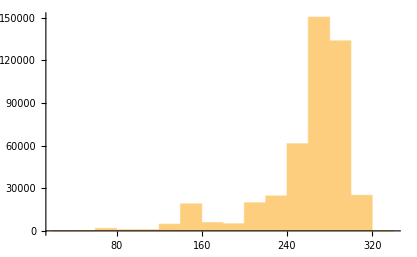

322

75

```mathematica
StringSplit/@TrainSet$4var3$CommonSet$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/valid_set_4var3.txt",TrainSet$4var3$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/test_set_4var3.txt",TrainSet$4var3$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/train_set_4var3.txt",TrainSet$4var3$CommonSet$format3⟦3129;;453128⟧,"Text"]
```

/Users/jaeha/inequality/MMA_package

../../dataset_storage/datasets/multi/valid_set_4var3.txt

../../dataset_storage/datasets/multi/test_set_4var3.txt

../../dataset_storage/datasets/multi/train_set_4var3.txt

### CURRICULUM LEARNING for 3 Variable in format 3

```mathematica
numTrain = 100000;
```

#### Short (5, 3, 5) / Sub (5, 3, 5) / Distribute

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$5distribute$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS$Distribute[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$5distribute$CommonSet[1]//TableForm
```

-128 a[0]^7 a[1] a[2]-192 a[0]^5 a[1]^3 a[2]-72 a[0]^3 a[1]^5 a[2]+64 a[0]^6 a[1] a[2]^2-80 a[0]^5 a[1]^2 a[2]^2+48 a[0]^4 a[1]^3 a[2]^2-60 a[0]^3 a[1]^4 a[2]^2-8 a[0]^5 a[1] a[2]^3+20 a[0]^4 a[1]^2 a[2]^3+192 a[0]^4 a[1] a[2]^4+144 a[0]^2 a[1]^3 a[2]^4-48 a[0]^3 a[1] a[2]^5+60 a[0]^2 a[1]^2 a[2]^5-64 a[0] a[1]^3 a[2]^5+160 a[0] a[1]^2 a[2]^6+192 a[1]^3 a[2]^6-172 a[0] a[1] a[2]^7-720 a[1]^2 a[2]^7+900 a[1] a[2]^8-375 a[2]^9 | -100 a[0] a[1] a[2]^7+80 a[0] a[1]^2 a[2]^6+80 a[0] a[1]^2 a[2]^6+-64 a[0] a[1]^3 a[2]^5+-375 a[2]^9+300 a[1] a[2]^8+300 a[1] a[2]^8+-240 a[1]^2 a[2]^7+300 a[1] a[2]^8+-240 a[1]^2 a[2]^7+-240 a[1]^2 a[2]^7+192 a[1]^3 a[2]^6+20 a[0]^4 a[1]^2 a[2]^3+-80 a[0]^5 a[1]^2 a[2]^2+-60 a[0]^3 a[1]^4 a[2]^2+60 a[0]^2 a[1]^2 a[2]^5+-128 a[0]^7 a[1] a[2]+96 a[0]^4 a[1] a[2]^4+32 a[0]^6 a[1] a[2]^2+-96 a[0]^5 a[1]^3 a[2]+96 a[0]^4 a[1] a[2]^4+-72 a[0] a[1] a[2]^7+-24 a[0]^3 a[1] a[2]^5+72 a[0]^2 a[1]^3 a[2]^4+32 a[0]^6 a[1] a[2]^2+-24 a[0]^3 a[1] a[2]^5+-8 a[0]^5 a[1] a[2]^3+24 a[0]^4 a[1]^3 a[2]^2+-96 a[0]^5 a[1]^3 a[2]+72 a[0]^2 a[1]^3 a[2]^4+24 a[0]^4 a[1]^3 a[2]^2+-72 a[0]^3 a[1]^5 a[2] | 3 b[0]^3+2 b[0]^2 b[1]+5 b[1]^2 b[2]+4 b[1] b[2]^2 | 4 a[1] a[2]^2-5 a[2]^3 | -2 a[0] a[1] a[2] | -4 a[0]^3-3 a[0] a[1]^2+a[0]^2 a[2]+3 a[2]^3

```mathematica
TrainSet$3var$5distribute$CommonSet = GenerateTrainSet$3var$5distribute$CommonSet[numTrain / 2];
```

```mathematica
TrainSet$3var$5distribute$CommonSet = DeleteDuplicatesBy[TrainSet$3var$5distribute$CommonSet,First];
Length[TrainSet$3var$5distribute$CommonSet]
```

50000

```mathematica
ByteCount[TrainSet$3var$5distribute$CommonSet]
```

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$5distribute$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm, distributedForm,short,sub1,sub2,sub3}=TrainSet$3var$5distribute$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
distributed=MMAExprToJFStringNonExpand[distributedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original,distributed}],{i,Min[n,Length[TrainSet$3var$5distribute$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$5distribute$format3=GenerateTrainSet$3var$5distribute$CommonSet$format3[50000];
Length[TrainSet$3var$5distribute$format3]
```

100000

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

```mathematica
Length[TrainSet$3var$5distribute$format3]
```

100000

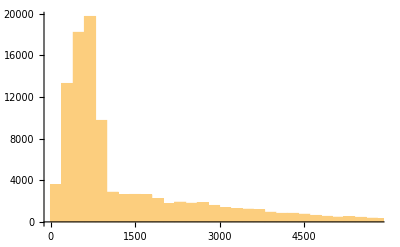

11177

```mathematica
Length/@StringSplit/@TrainSet$3var$5distribute$format3;
%//Histogram
%%//Max
```

99335

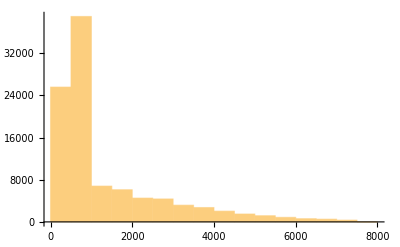

7500

```mathematica
TrainSet$3var$5distribute$format3$reduced=Select[TrainSet$3var$5distribute$format3,Length[StringSplit[#]]<=7500&];
Length[%]
Length/@StringSplit/@TrainSet$3var$5distribute$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$5distribute$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/valid_set_3var_5coef_distribute.txt",TrainSet$3var$5distribute$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/test_set_3var_5coef_distribute.txt",TrainSet$3var$5distribute$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/train_set_3var_5coef_distribute.txt",TrainSet$3var$5distribute$format3$reduced⟦3129;;99335⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/valid_set_3var_5coef_distribute.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/test_set_3var_5coef_distribute.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/train_set_3var_5coef_distribute.txt

#### Short (5, 3, 5) / Sub (5, 3, 5) / Expand

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3vars$535355$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$3vars$535355$CommonSet = GenerateTrainSet$3vars$535355$CommonSet[numTrain];
TrainSet$3vars$535355$CommonSet = DeleteDuplicates[TrainSet$3vars$535355$CommonSet];
Length[TrainSet$3vars$535355$CommonSet]
```

100000

```mathematica
TrainSet$3vars$535355$CommonSet[[1]]
```

{-135 a[0]^9+144 a[0]^7 a[2]^2-675 a[0]^6 a[2]^3-128 a[0]^3 a[1]^2 a[2]^4+480 a[0]^4 a[2]^5+128 a[0]^3 a[1] a[2]^5-1125 a[0]^3 a[2]^6+400 a[0] a[2]^8-625 a[2]^9,-5 b[1]^3-2 b[0]^2 b[2]+4 b[1]^2 b[2]+2 b[0] b[2]^2,4 a[0] a[1] a[2],3 a[0]^3+5 a[2]^3,4 a[0] a[2]^2}

```mathematica
GenerateTrainSet$3vars$535355$CommonSet$format3[n_]:=
Monitor[
Table[
{long,short,sub1,sub2,sub3}=TrainSet$3vars$535355$CommonSet ⟦i⟧;
MMAExprToJFString[long]<>" ? "<>MMAExprToJFString[short]<>" & "<>MMAExprToJFString[sub1]<>" & "<>MMAExprToJFString[sub2]<>" & "<>MMAExprToJFString[sub3]
,{i,n}],
Row[{"Generating element: ", i}]];
```

```mathematica
TrainSet$3vars$535355$CommonSet$format3=GenerateTrainSet$3vars$535355$CommonSet$format3[100000];
```

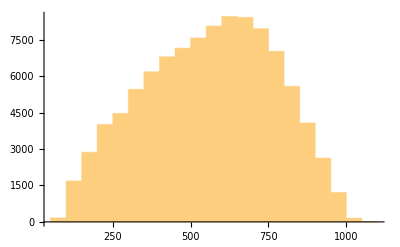

1060

```mathematica
Length/@StringSplit/@TrainSet$3vars$535355$CommonSet$format3//Histogram
Length/@StringSplit/@TrainSet$3vars$535355$CommonSet$format3//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/valid_set_3var_5coef_expand.txt",TrainSet$3vars$535355$CommonSet$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/test_set_3var_5coef_expand.txt",TrainSet$3vars$535355$CommonSet$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/train_set_3var_5coef_expand.txt",TrainSet$3vars$535355$CommonSet$format3⟦3129;;100000⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/valid_set_3var_5coef_expand.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/test_set_3var_5coef_expand.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_5/train_set_3var_5coef_expand.txt

#### Short (7, 3, 5) / Sub (7, 3, 5) / Distribute

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$7distribute$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS$Distribute[7,3,7,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,5],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$7distribute$CommonSet[1]//TableForm
```

436 a[0]^6 a[1]^3-588 a[0]^5 a[1]^4+468 a[0]^4 a[1]^5-1188 a[0]^6 a[1]^2 a[2]+250 a[0]^5 a[1]^3 a[2]+1178 a[0]^4 a[1]^4 a[2]+780 a[0]^3 a[1]^5 a[2]-12 a[0]^6 a[1] a[2]^2+2244 a[0]^5 a[1]^2 a[2]^2+703 a[0]^4 a[1]^3 a[2]^2+3046 a[0]^3 a[1]^4 a[2]^2+577 a[0]^2 a[1]^5 a[2]^2+448 a[0]^6 a[2]^3+1344 a[0]^5 a[1] a[2]^3+1968 a[0]^4 a[1]^2 a[2]^3+2840 a[0]^3 a[1]^3 a[2]^3+2976 a[0]^2 a[1]^4 a[2]^3+420 a[0] a[1]^5 a[2]^3-1584 a[0]^4 a[1] a[2]^4+2230 a[0]^3 a[1]^2 a[2]^4+5043 a[0]^2 a[1]^3 a[2]^4+1582 a[0] a[1]^4 a[2]^4+175 a[1]^5 a[2]^4+144 a[0]^4 a[2]^5+2128 a[0]^3 a[1] a[2]^5+2108 a[0]^2 a[1]^2 a[2]^5+1190 a[0] a[1]^3 a[2]^5+210 a[1]^4 a[2]^5-1541 a[0]^2 a[1] a[2]^6-434 a[0] a[1]^2 a[2]^6-756 a[1]^3 a[2]^6-1496 a[0]^2 a[2]^7-392 a[0] a[1] a[2]^7-182 a[1]^2 a[2]^7+7 a[1] a[2]^8-658 a[2]^9 | 686 a[0]^6 a[1]^3+-686 a[0]^4 a[1]^3 a[2]^2+-686 a[0]^4 a[1]^3 a[2]^2+686 a[0]^2 a[1]^3 a[2]^4+-686 a[0]^4 a[1]^3 a[2]^2+686 a[0]^2 a[1]^3 a[2]^4+686 a[0]^2 a[1]^3 a[2]^4+-686 a[1]^3 a[2]^6+-686 a[2]^9+-490 a[0]^2 a[1] a[2]^6+-392 a[0]^2 a[2]^7+-490 a[0]^2 a[1] a[2]^6+-350 a[0]^4 a[1]^2 a[2]^3+-280 a[0]^4 a[1] a[2]^4+-392 a[0]^2 a[2]^7+-280 a[0]^4 a[1] a[2]^4+-224 a[0]^4 a[2]^5+-490 a[0]^2 a[1] a[2]^6+-350 a[0]^4 a[1]^2 a[2]^3+-280 a[0]^4 a[1] a[2]^4+-350 a[0]^4 a[1]^2 a[2]^3+-250 a[0]^6 a[1]^3+-200 a[0]^6 a[1]^2 a[2]+-280 a[0]^4 a[1] a[2]^4+-200 a[0]^6 a[1]^2 a[2]+-160 a[0]^6 a[1] a[2]^2+-392 a[0]^2 a[2]^7+-280 a[0]^4 a[1] a[2]^4+-224 a[0]^4 a[2]^5+-280 a[0]^4 a[1] a[2]^4+-200 a[0]^6 a[1]^2 a[2]+-160 a[0]^6 a[1] a[2]^2+-224 a[0]^4 a[2]^5+-160 a[0]^6 a[1] a[2]^2+-128 a[0]^6 a[2]^3+98 a[0]^4 a[1]^2 a[2]^3+-490 a[0]^4 a[1]^4 a[2]+-588 a[0]^6 a[1]^2 a[2]+-588 a[0]^5 a[1]^4+-686 a[0]^5 a[1]^3 a[2]+-98 a[0]^2 a[1]^2 a[2]^5+490 a[0]^2 a[1]^4 a[2]^3+588 a[0]^4 a[1]^2 a[2]^3+588 a[0]^3 a[1]^4 a[2]^2+686 a[0]^3 a[1]^3 a[2]^3+-98 a[0]^2 a[1]^2 a[2]^5+490 a[0]^2 a[1]^4 a[2]^3+588 a[0]^4 a[1]^2 a[2]^3+588 a[0]^3 a[1]^4 a[2]^2+686 a[0]^3 a[1]^3 a[2]^3+98 a[1]^2 a[2]^7+-490 a[1]^4 a[2]^5+-588 a[0]^2 a[1]^2 a[2]^5+-588 a[0] a[1]^4 a[2]^4+-686 a[0] a[1]^3 a[2]^5+-7 a[0]^2 a[1] a[2]^6+35 a[0]^2 a[1]^3 a[2]^4+42 a[0]^3 a[1]^3 a[2]^3+42 a[0]^4 a[1] a[2]^4+49 a[0]^3 a[1]^2 a[2]^4+35 a[0]^2 a[1]^3 a[2]^4+-175 a[0]^2 a[1]^5 a[2]^2+-210 a[0]^3 a[1]^5 a[2]+-210 a[0]^4 a[1]^3 a[2]^2+-245 a[0]^3 a[1]^4 a[2]^2+42 a[0]^3 a[1]^3 a[2]^3+-210 a[0]^3 a[1]^5 a[2]+-252 a[0]^4 a[1]^5+-252 a[0]^5 a[1]^3 a[2]+-294 a[0]^4 a[1]^4 a[2]+42 a[0]^4 a[1] a[2]^4+-210 a[0]^4 a[1]^3 a[2]^2+-252 a[0]^5 a[1]^3 a[2]+-252 a[0]^6 a[1] a[2]^2+-294 a[0]^5 a[1]^2 a[2]^2+49 a[0]^3 a[1]^2 a[2]^4+-245 a[0]^3 a[1]^4 a[2]^2+-294 a[0]^4 a[1]^4 a[2]+-294 a[0]^5 a[1]^2 a[2]^2+-343 a[0]^4 a[1]^3 a[2]^2+7 a[1] a[2]^8+-35 a[1]^3 a[2]^6+-42 a[0] a[1]^3 a[2]^5+-42 a[0]^2 a[1] a[2]^6+-49 a[0] a[1]^2 a[2]^6+-35 a[1]^3 a[2]^6+175 a[1]^5 a[2]^4+210 a[0] a[1]^5 a[2]^3+210 a[0]^2 a[1]^3 a[2]^4+245 a[0] a[1]^4 a[2]^4+-42 a[0] a[1]^3 a[2]^5+210 a[0] a[1]^5 a[2]^3+252 a[0]^2 a[1]^5 a[2]^2+252 a[0]^3 a[1]^3 a[2]^3+294 a[0]^2 a[1]^4 a[2]^3+-42 a[0]^2 a[1] a[2]^6+210 a[0]^2 a[1]^3 a[2]^4+252 a[0]^3 a[1]^3 a[2]^3+252 a[0]^4 a[1] a[2]^4+294 a[0]^3 a[1]^2 a[2]^4+-49 a[0] a[1]^2 a[2]^6+245 a[0] a[1]^4 a[2]^4+294 a[0]^2 a[1]^4 a[2]^3+294 a[0]^3 a[1]^2 a[2]^4+343 a[0]^2 a[1]^3 a[2]^4+28 a[2]^9+-140 a[1]^2 a[2]^7+-168 a[0] a[1]^2 a[2]^6+-168 a[0]^2 a[2]^7+-196 a[0] a[1] a[2]^7+-140 a[1]^2 a[2]^7+700 a[1]^4 a[2]^5+840 a[0] a[1]^4 a[2]^4+840 a[0]^2 a[1]^2 a[2]^5+980 a[0] a[1]^3 a[2]^5+-168 a[0] a[1]^2 a[2]^6+840 a[0] a[1]^4 a[2]^4+1008 a[0]^2 a[1]^4 a[2]^3+1008 a[0]^3 a[1]^2 a[2]^4+1176 a[0]^2 a[1]^3 a[2]^4+-168 a[0]^2 a[2]^7+840 a[0]^2 a[1]^2 a[2]^5+1008 a[0]^3 a[1]^2 a[2]^4+1008 a[0]^4 a[2]^5+1176 a[0]^3 a[1] a[2]^5+-196 a[0] a[1] a[2]^7+980 a[0] a[1]^3 a[2]^5+1176 a[0]^2 a[1]^3 a[2]^4+1176 a[0]^3 a[1] a[2]^5+1372 a[0]^2 a[1]^2 a[2]^5+20 a[0]^2 a[1] a[2]^6+-100 a[0]^2 a[1]^3 a[2]^4+-120 a[0]^3 a[1]^3 a[2]^3+-120 a[0]^4 a[1] a[2]^4+-140 a[0]^3 a[1]^2 a[2]^4+-100 a[0]^2 a[1]^3 a[2]^4+500 a[0]^2 a[1]^5 a[2]^2+600 a[0]^3 a[1]^5 a[2]+600 a[0]^4 a[1]^3 a[2]^2+700 a[0]^3 a[1]^4 a[2]^2+-120 a[0]^3 a[1]^3 a[2]^3+600 a[0]^3 a[1]^5 a[2]+720 a[0]^4 a[1]^5+720 a[0]^5 a[1]^3 a[2]+840 a[0]^4 a[1]^4 a[2]+-120 a[0]^4 a[1] a[2]^4+600 a[0]^4 a[1]^3 a[2]^2+720 a[0]^5 a[1]^3 a[2]+720 a[0]^6 a[1] a[2]^2+840 a[0]^5 a[1]^2 a[2]^2+-140 a[0]^3 a[1]^2 a[2]^4+700 a[0]^3 a[1]^4 a[2]^2+840 a[0]^4 a[1]^4 a[2]+840 a[0]^5 a[1]^2 a[2]^2+980 a[0]^4 a[1]^3 a[2]^2+16 a[0]^2 a[2]^7+-80 a[0]^2 a[1]^2 a[2]^5+-96 a[0]^3 a[1]^2 a[2]^4+-96 a[0]^4 a[2]^5+-112 a[0]^3 a[1] a[2]^5+-80 a[0]^2 a[1]^2 a[2]^5+400 a[0]^2 a[1]^4 a[2]^3+480 a[0]^3 a[1]^4 a[2]^2+480 a[0]^4 a[1]^2 a[2]^3+560 a[0]^3 a[1]^3 a[2]^3+-96 a[0]^3 a[1]^2 a[2]^4+480 a[0]^3 a[1]^4 a[2]^2+576 a[0]^4 a[1]^4 a[2]+576 a[0]^5 a[1]^2 a[2]^2+672 a[0]^4 a[1]^3 a[2]^2+-96 a[0]^4 a[2]^5+480 a[0]^4 a[1]^2 a[2]^3+576 a[0]^5 a[1]^2 a[2]^2+576 a[0]^6 a[2]^3+672 a[0]^5 a[1] a[2]^3+-112 a[0]^3 a[1] a[2]^5+560 a[0]^3 a[1]^3 a[2]^3+672 a[0]^4 a[1]^3 a[2]^2+672 a[0]^5 a[1] a[2]^3+784 a[0]^4 a[1]^2 a[2]^3 | -2 b[0]^3-2 b[0]^2 b[1]+b[0] b[1]^2-4 b[1]^2 b[2]+2 b[2]^3 | -7 a[0]^2 a[1]+7 a[1] a[2]^2 | 6 a[0] a[1]^2+6 a[0]^2 a[2]+7 a[0] a[1] a[2]+5 a[1]^2 a[2]-a[2]^3 | -5 a[0]^2 a[1]-4 a[0]^2 a[2]-7 a[2]^3

```mathematica
numTrain = 100000;
TrainSet$3var$7distribute$CommonSet = GenerateTrainSet$3var$7distribute$CommonSet[numTrain / 2];
```

```mathematica
TrainSet$3var$7distribute$CommonSet = DeleteDuplicatesBy[TrainSet$3var$7distribute$CommonSet,First];
Length[TrainSet$3var$7distribute$CommonSet]
```

50000

```mathematica
ByteCount[TrainSet$3var$7distribute$CommonSet]
```

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$7distribute$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm, distributedForm,short,sub1,sub2,sub3}=TrainSet$3var$7distribute$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
distributed=MMAExprToJFStringNonExpand[distributedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original,distributed}],{i,Min[n,Length[TrainSet$3var$7distribute$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$7distribute$format3=GenerateTrainSet$3var$7distribute$CommonSet$format3[50000];
Length[TrainSet$3var$7distribute$format3]
```

100000

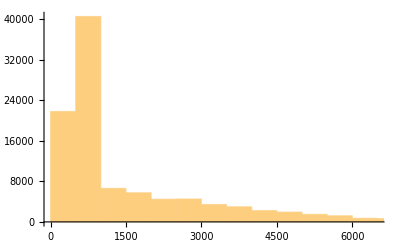

11533

```mathematica
Length/@StringSplit/@TrainSet$3var$7distribute$format3;
%//Histogram
%%//Max
```

98838

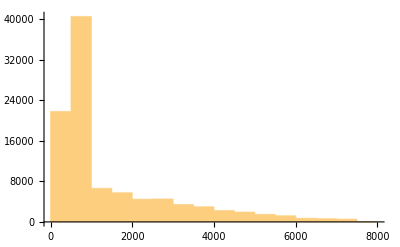

7500

```mathematica
TrainSet$3var$7distribute$format3$reduced=Select[TrainSet$3var$7distribute$format3,Length[StringSplit[#]]<=7500&];
Length[%]
Length/@StringSplit/@TrainSet$3var$7distribute$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$7distribute$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/valid_set_3var_7coef_distribute.txt",TrainSet$3var$7distribute$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/test_set_3var_7coef_distribute.txt",TrainSet$3var$7distribute$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/train_set_3var_7coef_distribute.txt",TrainSet$3var$7distribute$format3$reduced⟦3129;;98838⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/valid_set_3var_7coef_distribute.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/test_set_3var_7coef_distribute.txt

../../dataset_storage/datasets/multi/var_3_curriculum_learning/coef_7/train_set_3var_7coef_distribute.txt

### 3 VAR Experiment

```mathematica
numTrain = 1000000;
numTest = 4000;
```

#### Short (5, 3, 3) / Sub (5, 3, 3) / Distribute ( Data 8 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS$Distribute[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

-188 a[0]^3 a[1]^6-32 a[0]^2 a[1]^7-192 a[0] a[1]^8-556 a[0]^3 a[1]^5 a[2]+8 a[0]^2 a[1]^6 a[2]-480 a[0] a[1]^7 a[2]-560 a[0]^3 a[1]^4 a[2]^2+88 a[0]^2 a[1]^5 a[2]^2-396 a[0] a[1]^6 a[2]^2-192 a[0]^3 a[1]^3 a[2]^3-647 a[0]^2 a[1]^4 a[2]^3-68 a[0] a[1]^5 a[2]^3-240 a[1]^6 a[2]^3-1400 a[0]^2 a[1]^3 a[2]^4+190 a[0] a[1]^4 a[2]^4-360 a[1]^5 a[2]^4-720 a[0]^2 a[1]^2 a[2]^5+120 a[0] a[1]^3 a[2]^5-135 a[1]^4 a[2]^5-875 a[0] a[1]^2 a[2]^6+100 a[1]^3 a[2]^6-900 a[0] a[1] a[2]^7+75 a[1]^2 a[2]^7-375 a[2]^9 | -240 a[1]^6 a[2]^3+-192 a[0] a[1]^8+-192 a[0] a[1]^7 a[2]+-60 a[0] a[1]^5 a[2]^3+-48 a[0]^2 a[1]^7+-48 a[0]^2 a[1]^6 a[2]+-180 a[1]^5 a[2]^4+-144 a[0] a[1]^7 a[2]+-144 a[0] a[1]^6 a[2]^2+-60 a[0] a[1]^5 a[2]^3+-48 a[0]^2 a[1]^7+-48 a[0]^2 a[1]^6 a[2]+-15 a[0]^2 a[1]^4 a[2]^3+-12 a[0]^3 a[1]^6+-12 a[0]^3 a[1]^5 a[2]+-45 a[0] a[1]^4 a[2]^4+-36 a[0]^2 a[1]^6 a[2]+-36 a[0]^2 a[1]^5 a[2]^2+-180 a[1]^5 a[2]^4+-144 a[0] a[1]^7 a[2]+-144 a[0] a[1]^6 a[2]^2+-45 a[0] a[1]^4 a[2]^4+-36 a[0]^2 a[1]^6 a[2]+-36 a[0]^2 a[1]^5 a[2]^2+-135 a[1]^4 a[2]^5+-108 a[0] a[1]^6 a[2]^2+-108 a[0] a[1]^5 a[2]^3+25 a[0] a[1]^2 a[2]^6+20 a[0]^2 a[1]^4 a[2]^3+20 a[0]^2 a[1]^3 a[2]^4+20 a[0]^2 a[1]^4 a[2]^3+16 a[0]^3 a[1]^6+16 a[0]^3 a[1]^5 a[2]+20 a[0]^2 a[1]^3 a[2]^4+16 a[0]^3 a[1]^5 a[2]+16 a[0]^3 a[1]^4 a[2]^2+75 a[1]^2 a[2]^7+60 a[0] a[1]^4 a[2]^4+60 a[0] a[1]^3 a[2]^5+60 a[0] a[1]^4 a[2]^4+48 a[0]^2 a[1]^6 a[2]+48 a[0]^2 a[1]^5 a[2]^2+60 a[0] a[1]^3 a[2]^5+48 a[0]^2 a[1]^5 a[2]^2+48 a[0]^2 a[1]^4 a[2]^3+100 a[1]^3 a[2]^6+80 a[0] a[1]^5 a[2]^3+80 a[0] a[1]^4 a[2]^4+80 a[0] a[1]^5 a[2]^3+64 a[0]^2 a[1]^7+64 a[0]^2 a[1]^6 a[2]+80 a[0] a[1]^4 a[2]^4+64 a[0]^2 a[1]^6 a[2]+64 a[0]^2 a[1]^5 a[2]^2+-375 a[2]^9+-300 a[0] a[1]^2 a[2]^6+-300 a[0] a[1] a[2]^7+-300 a[0] a[1]^2 a[2]^6+-240 a[0]^2 a[1]^4 a[2]^3+-240 a[0]^2 a[1]^3 a[2]^4+-300 a[0] a[1] a[2]^7+-240 a[0]^2 a[1]^3 a[2]^4+-240 a[0]^2 a[1]^2 a[2]^5+-300 a[0] a[1]^2 a[2]^6+-240 a[0]^2 a[1]^4 a[2]^3+-240 a[0]^2 a[1]^3 a[2]^4+-240 a[0]^2 a[1]^4 a[2]^3+-192 a[0]^3 a[1]^6+-192 a[0]^3 a[1]^5 a[2]+-240 a[0]^2 a[1]^3 a[2]^4+-192 a[0]^3 a[1]^5 a[2]+-192 a[0]^3 a[1]^4 a[2]^2+-300 a[0] a[1] a[2]^7+-240 a[0]^2 a[1]^3 a[2]^4+-240 a[0]^2 a[1]^2 a[2]^5+-240 a[0]^2 a[1]^3 a[2]^4+-192 a[0]^3 a[1]^5 a[2]+-192 a[0]^3 a[1]^4 a[2]^2+-240 a[0]^2 a[1]^2 a[2]^5+-192 a[0]^3 a[1]^4 a[2]^2+-192 a[0]^3 a[1]^3 a[2]^3 | 3 b[0]^3+b[0]^2 b[2]+3 b[0] b[2]^2 | -4 a[0] a[1]^2-4 a[0] a[1] a[2]-5 a[2]^3 | -a[0]^2 a[1]-5 a[1]^3+2 a[0]^2 a[2] | a[0] a[1]^2+4 a[1]^3+3 a[1]^2 a[2]

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[numTrain / 2];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

498088

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

8175601656

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm, distributedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
distributed=MMAExprToJFStringNonExpand[distributedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original,distributed}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[numTrain / 2];
Length[TrainSet$3var$33$format3]
```

996176

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Plus[Times[12,a[0]],Times[-16,a[0],a[1]],Times[-24,Power[a[0],2],a[1]],Times[20,Power[a[1],2]],Times[-40,a[0],Power[a[1],3]]],Inactive[Plus][Times[-16,a[0],a[1]],Times[12,a[0]],Times[20,Power[a[1],2]],Times[-24,Power[a[0],2],a[1]],Times[-40,a[0],Power[a[1],3]]],Plus[Times[-4,b[0]],Times[4,b[1]],Times[-2,b[0],b[1]]],Plus[Times[-3,a[0]],Times[-5,Power[a[1],2]]],Times[-4,a[0],a[1]]]

```mathematica
Length[TrainSet$3var$33$format3]
```

996176

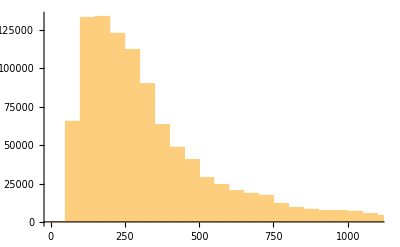

1626

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

967380

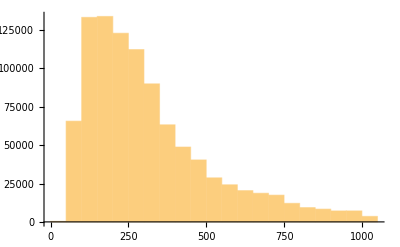

1024

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=1024&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/valid_set_3var_535333_distribute.txt",TrainSet$3var$33$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/test_set_3var_535333_distribute.txt",TrainSet$3var$33$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/train_set_3var_535333_distribute.txt",TrainSet$3var$33$format3$reduced⟦3129;;967380⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3/terms_33/valid_set_3var_535333_distribute.txt

../../dataset_storage/datasets/multi/var_3/terms_33/test_set_3var_535333_distribute.txt

../../dataset_storage/datasets/multi/var_3/terms_33/train_set_3var_535333_distribute.txt

#### Short (5, 3, 5) / Sub (5, 3, 3) / Distribute

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$53$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS$Distribute[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$53$CommonSet[1]//TableForm
```

-25 a[0]^4 a[1]^5+15 a[0]^2 a[1]^7+150 a[0]^5 a[1]^3 a[2]+65 a[0]^4 a[1]^4 a[2]-87 a[0]^2 a[1]^6 a[2]+3 a[0] a[1]^7 a[2]+60 a[0]^5 a[1]^2 a[2]^2+29 a[0]^4 a[1]^3 a[2]^2+117 a[0]^2 a[1]^5 a[2]^2-18 a[0] a[1]^6 a[2]^2+6 a[0]^5 a[1] a[2]^3+3 a[0]^4 a[1]^2 a[2]^3+27 a[0]^2 a[1]^4 a[2]^3+27 a[0] a[1]^5 a[2]^3 | 6 a[0]^5 a[1] a[2]^3+30 a[0]^5 a[1]^2 a[2]^2+30 a[0]^5 a[1]^2 a[2]^2+150 a[0]^5 a[1]^3 a[2]+-a[0]^4 a[1]^3 a[2]^2+3 a[0]^4 a[1]^2 a[2]^3+-5 a[0]^4 a[1]^4 a[2]+15 a[0]^4 a[1]^3 a[2]^2+-5 a[0]^4 a[1]^4 a[2]+15 a[0]^4 a[1]^3 a[2]^2+-25 a[0]^4 a[1]^5+75 a[0]^4 a[1]^4 a[2]+3 a[0] a[1]^7 a[2]+-9 a[0] a[1]^6 a[2]^2+-9 a[0] a[1]^6 a[2]^2+27 a[0] a[1]^5 a[2]^3+3 a[0]^2 a[1]^6 a[2]+-9 a[0]^2 a[1]^5 a[2]^2+-9 a[0]^2 a[1]^5 a[2]^2+27 a[0]^2 a[1]^4 a[2]^3+15 a[0]^2 a[1]^7+-45 a[0]^2 a[1]^6 a[2]+-45 a[0]^2 a[1]^6 a[2]+135 a[0]^2 a[1]^5 a[2]^2 | 2 b[0]^2 b[1]-b[0]^2 b[2]+3 b[0] b[2]^2+b[1] b[2]^2 | 5 a[0]^2 a[1]+a[0]^2 a[2] | 3 a[0] a[1] a[2] | a[1]^3-3 a[1]^2 a[2]

```mathematica
TrainSet$3var$53$CommonSet = GenerateTrainSet$3var$53$CommonSet[numTrain / 2];
```

```mathematica
TrainSet$3var$53$CommonSet = DeleteDuplicatesBy[TrainSet$3var$53$CommonSet,First];
Length[TrainSet$3var$53$CommonSet]
```

499974

```mathematica
ByteCount[TrainSet$3var$53$CommonSet]
```

12467222360

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$53$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm, distributedForm,short,sub1,sub2,sub3}=TrainSet$3var$53$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
distributed=MMAExprToJFStringNonExpand[distributedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original,distributed}],{i,Min[n,Length[TrainSet$3var$53$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$53$format3=GenerateTrainSet$3var$53$CommonSet$format3[numTrain / 2];
Length[TrainSet$3var$53$format3]
```

999948

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},5,3]]
```

List[Plus[Times[20,a[0]],Times[12,Power[a[0],2]],Times[-100,Power[a[0],3]],Times[-60,Power[a[0],4]],Times[-16,a[1]],Times[-75,a[0],a[1]],Times[35,Power[a[0],2],a[1]],Times[60,Power[a[1],2]],Times[125,a[0],Power[a[1],2]],Times[75,Power[a[0],2],Power[a[1],2]],Times[-100,Power[a[1],3]]],Inactive[Plus][Times[-16,a[1]],Times[20,a[0]],Times[12,Power[a[0],2]],Times[60,Power[a[1],2]],Times[80,Power[a[0],2],a[1]],Times[-100,Power[a[1],3]],Times[-75,a[0],a[1]],Times[-100,Power[a[0],3]],Times[125,a[0],Power[a[1],2]],Times[-45,Power[a[0],2],a[1]],Times[-60,Power[a[0],4]],Times[75,Power[a[0],2],Power[a[1],2]]],Plus[Times[4,b[0]],Times[5,b[0],b[1]]],Plus[Times[5,a[0]],Times[3,Power[a[0],2]],Times[-4,a[1]]],Plus[Times[-4,Power[a[0],2]],Times[-3,a[1]],Times[5,Power[a[1],2]]]]

```mathematica
Length[TrainSet$3var$53$format3]
```

999948

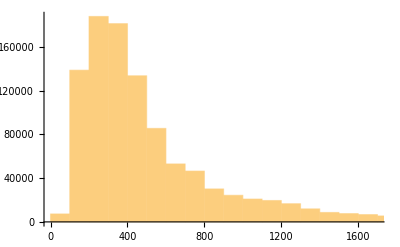

2662

```mathematica
Length/@StringSplit/@TrainSet$3var$53$format3;
%//Histogram
%%//Max
```

893414

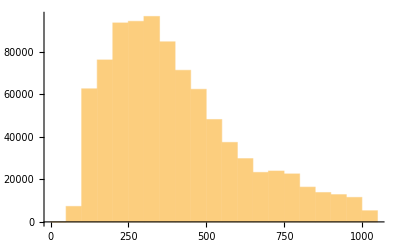

1024

```mathematica
TrainSet$3var$53$format3$reduced=Select[TrainSet$3var$53$format3,Length[StringSplit[#]]<=1024&];
Length[%]
Length/@StringSplit/@TrainSet$3var$53$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$53$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/valid_set_3var_535353_distribute.txt",TrainSet$3var$53$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/test_set_3var_535353_distribute.txt",TrainSet$3var$53$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/train_set_3var_535353_distribute.txt",TrainSet$3var$53$format3$reduced⟦3129;;893414⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3/terms_53/valid_set_3var_535353_distribute.txt

../../dataset_storage/datasets/multi/var_3/terms_53/test_set_3var_535353_distribute.txt

../../dataset_storage/datasets/multi/var_3/terms_53/train_set_3var_535353_distribute.txt

5000

```mathematica
numTest= 5000
```

5000

```mathematica
numTest= 5000
```

#### Short (5, 3, 3) / Sub (5, 3, 3) / Collect Test

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

-a[0]^3 a[1]^6-9 a[0]^2 a[1]^5 a[2]^2-18 a[0]^2 a[1]^3 a[2]^4 | -b[1]^3-2 b[0]^2 b[2]-3 b[0] b[1] b[2] | 3 a[0] a[2]^2 | a[0] a[1]^2 | a[1]^3

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[numTrain];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

995124

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

6879852896

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[numTrain];
Length[TrainSet$3var$33$format3]
```

995124

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Times[-10,a[0]],Times[-10,a[0]],Plus[Times[5,b[0]],b[1],Times[2,Power[b[1],2]]],Times[-2,a[0]],0]

```mathematica
Length[TrainSet$3var$33$format3]
```

995124

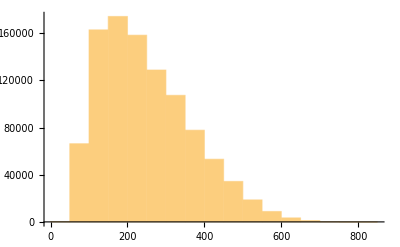

810

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=1024&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

995124

-Graphics-

810

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/valid_set_3var_535333_collect.txt",TrainSet$3var$33$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/test_set_3var_535333_collect.txt",TrainSet$3var$33$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_33/train_set_3var_535333_collect.txt",TrainSet$3var$33$format3$reduced⟦3129;;995124⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3/terms_33/valid_set_3var_535333_collect.txt

../../dataset_storage/datasets/multi/var_3/terms_33/test_set_3var_535333_collect.txt

../../dataset_storage/datasets/multi/var_3/terms_33/train_set_3var_535333_collect.txt

#### Short (5, 3, 5) / Sub (5, 3, 3) / Collect Test

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$53$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},5,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$53$CommonSet[1]//TableForm
```

4 a[0]^6 a[2]^3-5 a[0]^5 a[1] a[2]^3+427 a[0]^3 a[1]^3 a[2]^3+136 a[0]^2 a[1]^3 a[2]^4+36 a[0]^4 a[2]^5-30 a[0]^3 a[1] a[2]^5+116 a[0] a[1]^3 a[2]^5+32 a[1]^3 a[2]^6+108 a[0]^2 a[2]^7-45 a[0] a[1] a[2]^7+108 a[2]^9 | -4 b[0]^3+b[0]^2 b[1]+3 b[1]^3-b[1] b[2]^2+4 b[2]^3 | -2 a[0] a[1] a[2]-2 a[1] a[2]^2 | 5 a[0] a[1] a[2] | a[0]^2 a[2]+3 a[2]^3

```mathematica
TrainSet$3var$53$CommonSet = GenerateTrainSet$3var$53$CommonSet[numTrain];
```

```mathematica
TrainSet$3var$53$CommonSet = DeleteDuplicatesBy[TrainSet$3var$53$CommonSet,First];
Length[TrainSet$3var$53$CommonSet]
```

999898

```mathematica
ByteCount[TrainSet$3var$53$CommonSet]
```

9169256912

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$53$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$53$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$53$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$53$format3=GenerateTrainSet$3var$53$CommonSet$format3[numTrain];
Length[TrainSet$3var$53$format3]
```

999898

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},5,3]]
```

List[Plus[Times[-80,Power[a[0],2]],Times[200,Power[a[0],3]],Times[-125,Power[a[0],4]],Times[120,a[0],a[1]],Times[-150,Power[a[0],2],a[1]],Times[-45,Power[a[1],2]]],Plus[Times[-80,Power[a[0],2]],Times[200,Power[a[0],3]],Times[-125,Power[a[0],4]],Times[120,a[0],a[1]],Times[-150,Power[a[0],2],a[1]],Times[-45,Power[a[1],2]]],Plus[Times[-5,Power[b[0],2]],Times[5,b[1]],Times[5,b[0],b[1]],Times[5,Power[b[1],2]]],Plus[Times[4,a[0]],Times[-5,Power[a[0],2]],Times[-3,a[1]]],0]

```mathematica
Length[TrainSet$3var$53$format3]
```

999898

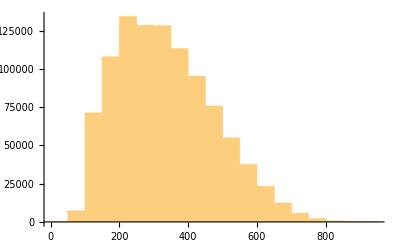

918

```mathematica
Length/@StringSplit/@TrainSet$3var$53$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$53$format3$reduced=Select[TrainSet$3var$53$format3,Length[StringSplit[#]]<=1024&];
Length[%]
Length/@StringSplit/@TrainSet$3var$53$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$53$format3$reduced//Max
```

999898

-Graphics-

918

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/valid_set_3var_535353_collect.txt",TrainSet$3var$53$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/test_set_3var_535353_collect.txt",TrainSet$3var$53$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/datasets/multi/var_3/terms_53/train_set_3var_535353_collect.txt",TrainSet$3var$53$format3$reduced⟦3129;;999898⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/datasets/multi/var_3/terms_53/valid_set_3var_535353_collect.txt

../../dataset_storage/datasets/multi/var_3/terms_53/test_set_3var_535353_collect.txt

../../dataset_storage/datasets/multi/var_3/terms_53/train_set_3var_535353_collect.txt

### Data 4, 5, 6, 7

```mathematica
(* (Coefficient, degree, number of terms, number of variable)*)
```

#### Short (5, 3, 3, 2) / Sub (5, 3, 3, 3) / Collect Test ( Data 4 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data4$CommonSet[3]//TableForm
```

500 a[0]^3 a[1]^6-500 a[0]^4 a[1]^4 a[2]-500 a[0]^5 a[1]^2 a[2]^2+500 a[0]^3 a[1]^4 a[2]^2+900 a[0]^2 a[1]^5 a[2]^2+1000 a[0]^4 a[1]^2 a[2]^3-600 a[0]^3 a[1]^3 a[2]^3+500 a[0]^2 a[1]^4 a[2]^3-300 a[0]^4 a[1] a[2]^4+500 a[0]^3 a[1]^2 a[2]^4+600 a[0]^2 a[1]^3 a[2]^4+540 a[0] a[1]^4 a[2]^4+600 a[0]^3 a[1] a[2]^5-1180 a[0]^2 a[1]^2 a[2]^5+600 a[0] a[1]^3 a[2]^5+300 a[0]^2 a[1] a[2]^6-320 a[0] a[1]^2 a[2]^6+108 a[1]^3 a[2]^6-600 a[0] a[1] a[2]^7+180 a[1]^2 a[2]^7-300 a[1] a[2]^8 | -4 b[0]^3-4 b[0]^2 b[1]+4 b[0] b[1]^2 | -5 a[0] a[1]^2-3 a[1] a[2]^2 | 5 a[0]^2 a[2]-5 a[0] a[2]^2-5 a[2]^3
-81 a[0]^6 a[1]^3+135 a[0]^4 a[1]^5-90 a[0]^6 a[1]^2 a[2]+135 a[0]^5 a[1]^2 a[2]^2-162 a[0]^4 a[1]^3 a[2]^2+180 a[0]^2 a[1]^5 a[2]^2-120 a[0]^4 a[1]^2 a[2]^3+180 a[0]^3 a[1]^2 a[2]^4-108 a[0]^2 a[1]^3 a[2]^4+60 a[1]^5 a[2]^4-40 a[0]^2 a[1]^2 a[2]^5+60 a[0] a[1]^2 a[2]^6-24 a[1]^3 a[2]^6 | -5 b[0] b[1]^2-3 b[1]^3 | -3 a[1]^3+2 a[0]^2 a[2]-3 a[0] a[2]^2 | 3 a[0]^2 a[1]+2 a[1] a[2]^2
12 a[0]^8 a[1]-90 a[0]^7 a[1]^2+12 a[0]^6 a[1]^3-45 a[0]^5 a[1]^4+3 a[0]^4 a[1]^5+24 a[0]^6 a[1]^2 a[2]-90 a[0]^5 a[1]^3 a[2]+12 a[0]^4 a[1]^4 a[2]-4 a[0]^7 a[2]^2+60 a[0]^6 a[1] a[2]^2-4 a[0]^5 a[1]^2 a[2]^2+42 a[0]^4 a[1]^3 a[2]^2-a[0]^3 a[1]^4 a[2]^2-8 a[0]^5 a[1] a[2]^3+60 a[0]^4 a[1]^2 a[2]^3-4 a[0]^3 a[1]^3 a[2]^3-10 a[0]^5 a[2]^4-9 a[0]^3 a[1]^2 a[2]^4-10 a[0]^3 a[1] a[2]^5 | 5 b[0]^2 b[1]-b[0] b[1]^2 | -3 a[0]^2 a[1]+a[0] a[2]^2 | -2 a[0]^3-a[0] a[1]^2-2 a[0] a[1] a[2]

```mathematica
TrainSet$data4$CommonSet = GenerateTrainSet$data4$CommonSet[1100000];
```

```mathematica
TrainSet$data4$CommonSet = DeleteDuplicatesBy[TrainSet$data4$CommonSet,First];
Length[TrainSet$data4$CommonSet]
```

1080612

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data4$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2}=TrainSet$data4$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2];
{original}],{i,Min[n,Length[TrainSet$data4$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data4$format3=GenerateTrainSet$data4$CommonSet$format3[1080000];
Length[TrainSet$data4$format3]
```

1080000

```mathematica
GenerateTrainSet$data4$CommonSet$format3[3]//TableForm
```

+ * N 1 2 5 * ^ a0 P 6 ^ a1 P 3 + * N 2 2 5 * ^ a0 P 4 * ^ a1 P 4 a2 + * N 8 0 * ^ a0 P 4 * ^ a1 P 3 ^ a2 P 2 + * N 1 3 5 * ^ a0 P 2 * ^ a1 P 5 ^ a2 P 2 + * N 3 0 0 * ^ a0 P 4 * ^ a1 P 2 ^ a2 P 3 + * P 8 * ^ a0 P 3 * ^ a1 P 3 ^ a2 P 3 + * N 4 8 * ^ a0 P 2 * ^ a1 P 4 ^ a2 P 3 + * N 2 7 * ^ a1 P 6 ^ a2 P 3 + * N 3 6 0 * ^ a0 P 2 * ^ a1 P 3 ^ a2 P 4 + * N 6 4 * ^ a0 P 2 * ^ a1 P 2 ^ a2 P 5 + * N 1 0 8 * ^ a1 P 4 ^ a2 P 5 + * N 2 4 0 * ^ a0 P 2 * a1 ^ a2 P 6 + * N 1 4 4 * ^ a1 P 2 ^ a2 P 7 * N 6 4 ^ a2 P 9 ? + * N 1 ^ b0 P 3 + * P 4 * ^ b0 P 2 b1 ^ b1 P 3 & * N 2 * a0 * a1 a2 & + * N 5 * ^ a0 P 2 a1 + * N 3 * ^ a1 P 2 a2 * N 4 ^ a2 P 3
+ * P 3 7 5 ^ a1 P 9 + * P 8 0 * ^ a0 P 2 * ^ a1 P 5 ^ a2 P 2 + * P 1 2 0 * a0 * ^ a1 P 4 ^ a2 P 4 * P 4 5 * ^ a1 P 3 ^ a2 P 6 ? + * N 3 ^ b0 P 3 * N 1 * b0 ^ b1 P 2 & * N 5 ^ a1 P 3 & + * P 4 * a0 * a1 a2 * P 3 ^ a2 P 3
+ * N 2 7 ^ a0 P 9 + * N 1 4 4 * ^ a0 P 8 a1 + * P 6 4 * ^ a0 P 6 ^ a1 P 3 + * N 5 4 * ^ a0 P 6 * a1 ^ a2 P 2 + * N 1 9 2 * ^ a0 P 5 * ^ a1 P 2 ^ a2 P 2 + * N 3 6 * ^ a0 P 3 * ^ a1 P 2 ^ a2 P 4 + * N 6 4 * ^ a0 P 2 * ^ a1 P 3 ^ a2 P 4 * N 8 * ^ a1 P 3 ^ a2 P 6 ? + * N 1 ^ b0 P 3 + * P 4 * ^ b0 P 2 b1 * N 1 ^ b1 P 3 & + * P 3 ^ a0 P 3 * P 2 * a1 ^ a2 P 2 & * N 4 * ^ a0 P 2 a1

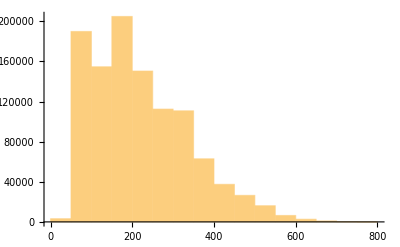

781

87

```mathematica
StringSplit/@TrainSet$data4$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data4_valid.txt",TrainSet$data4$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_test.txt",TrainSet$data4$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_train.txt",TrainSet$data4$format3⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data4_valid.txt

../../dataset_storage/on_the_paper/dataset/data4_test.txt

../../dataset_storage/on_the_paper/dataset/data4_train.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 3) / Collect Test ( Data 5 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data5$CommonSet[3]//TableForm
```

-64 a[0]^4 a[1]^4 a[2]-128 a[0]^5 a[1]^2 a[2]^2-15 a[0]^3 a[1]^4 a[2]^2+4 a[0]^2 a[1]^5 a[2]^2-15 a[0] a[1]^6 a[2]^2-60 a[0]^4 a[1]^2 a[2]^3+16 a[0]^3 a[1]^3 a[2]^3-60 a[0]^2 a[1]^4 a[2]^3-60 a[0]^5 a[2]^4+16 a[0]^4 a[1] a[2]^4-60 a[0]^3 a[1]^2 a[2]^4 | -4 b[1]^2 b[2]-3 b[0] b[2]^2+b[1] b[2]^2 | 5 a[0]^3+5 a[0] a[1]^2 | 4 a[0]^2 a[1] | a[1]^2 a[2]+2 a[0] a[2]^2
4 a[0]^9-36 a[0]^7 a[1]^2+108 a[0]^5 a[1]^4-108 a[0]^3 a[1]^6-2 a[0]^7 a[2]^2+12 a[0]^5 a[1]^2 a[2]^2-18 a[0]^3 a[1]^4 a[2]^2+25 a[0]^4 a[1]^2 a[2]^3-75 a[0]^2 a[1]^4 a[2]^3 | -4 b[0]^3-2 b[0]^2 b[1]+5 b[0] b[1] b[2] | -a[0]^3+3 a[0] a[1]^2 | a[0] a[2]^2 | -5 a[1]^2 a[2]
15 a[0]^6 a[1]^3+8 a[0]^6 a[1]^2 a[2]+45 a[0]^4 a[1]^4 a[2]+13 a[0]^4 a[1]^3 a[2]^2-45 a[0]^2 a[1]^5 a[2]^2-8 a[0]^4 a[1]^2 a[2]^3+42 a[0]^2 a[1]^4 a[2]^3-135 a[1]^6 a[2]^3-9 a[0]^2 a[1]^3 a[2]^4+135 a[1]^5 a[2]^4-45 a[1]^4 a[2]^5+5 a[1]^3 a[2]^6 | b[0] b[1] b[2]-5 b[0] b[2]^2+5 b[2]^3 | -2 a[0]^2 a[1] | 5 a[0]^2 a[1]+4 a[0]^2 a[2]+2 a[1] a[2]^2 | -a[0]^2 a[1]-3 a[1]^2 a[2]+a[1] a[2]^2

```mathematica
TrainSet$data5$CommonSet = GenerateTrainSet$data5$CommonSet[1030000];
```

```mathematica
TrainSet$data5$CommonSet = DeleteDuplicatesBy[TrainSet$data5$CommonSet,First];
Length[TrainSet$data5$CommonSet]
```

1024696

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data5$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$data5$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$data5$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data5$format3=GenerateTrainSet$data5$CommonSet$format3[1020000];
Length[TrainSet$data5$format3]
```

1020000

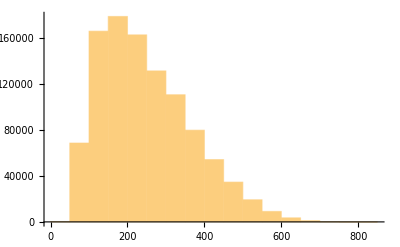

823

119

```mathematica
StringSplit/@TrainSet$data5$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data5_valid.txt",TrainSet$data5$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data5_test.txt",TrainSet$data5$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data5_train.txt",TrainSet$data5$format3⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data5_valid.txt

../../dataset_storage/on_the_paper/dataset/data5_test.txt

../../dataset_storage/on_the_paper/dataset/data5_train.txt

#### Short (5, 3, 3, 4) / Sub (5, 3, 3, 3) / Collect Test ( Data 8 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data8$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2], b[3]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data8$CommonSet[3]//TableForm
```

12 a[0]^8 a[1]-96 a[0]^5 a[1]^4+192 a[0]^2 a[1]^7-19 a[0]^8 a[2]+152 a[0]^5 a[1]^3 a[2]-304 a[0]^2 a[1]^6 a[2]+375 a[0]^3 a[1]^3 a[2]^3 | -3 b[0]^3+4 b[1] b[3]^2+b[2] b[3]^2 | -5 a[0] a[1] a[2] | 3 a[0]^2 a[1]-5 a[0]^2 a[2] | a[0]^2 a[2] | -a[0]^3+4 a[1]^3
-12 a[0]^5 a[1]^4+6 a[0]^4 a[1]^5+6 a[0]^3 a[1]^6-20 a[0]^5 a[1]^2 a[2]^2-20 a[0]^4 a[1]^3 a[2]^2+40 a[0]^3 a[1]^4 a[2]^2+54 a[1]^6 a[2]^3-50 a[0]^4 a[1] a[2]^4+50 a[0]^3 a[1]^2 a[2]^4+108 a[1]^4 a[2]^5+72 a[1]^2 a[2]^7+16 a[2]^9 | -2 b[0]^3-2 b[1]^2 b[3]-4 b[1] b[3]^2 | -3 a[1]^2 a[2]-2 a[2]^3 | 3 a[0] a[1]^2+5 a[0] a[2]^2 | -3 a[1] a[2]^2 | a[0]^2 a[1]-a[0] a[1]^2
128 a[1]^8 a[2]-200 a[0]^2 a[1]^5 a[2]^2-80 a[0]^2 a[1]^4 a[2]^3-160 a[0] a[1]^5 a[2]^3-256 a[1]^6 a[2]^3+200 a[0]^2 a[1]^3 a[2]^4-64 a[0] a[1]^4 a[2]^4+120 a[1]^5 a[2]^4+160 a[0] a[1]^3 a[2]^5+176 a[1]^4 a[2]^5-120 a[1]^3 a[2]^6 | 4 b[1] b[2]^2+5 b[1] b[2] b[3]-4 b[2] b[3]^2 | a[1]^3-3 a[0]^2 a[2]+3 a[1] a[2]^2 | -5 a[0]^2 a[2]-4 a[0] a[2]^2+3 a[2]^3 | -2 a[1]^2 a[2] | -4 a[1]^3+4 a[1] a[2]^2

```mathematica
TrainSet$data8$CommonSet = GenerateTrainSet$data8$CommonSet[1030000];
```

```mathematica
TrainSet$data8$CommonSet = DeleteDuplicatesBy[TrainSet$data8$CommonSet,First];
Length[TrainSet$data8$CommonSet]
```

```mathematica
1026939
```

1026939

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data8$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3,sub4}=TrainSet$data8$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3]<>" & "<>MMAExprToJFStringNonExpand[sub4];
{original}],{i,Min[n,Length[TrainSet$data8$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data8$format3=GenerateTrainSet$data8$CommonSet$format3[1010000];
Length[TrainSet$data8$format3]
```

1010000

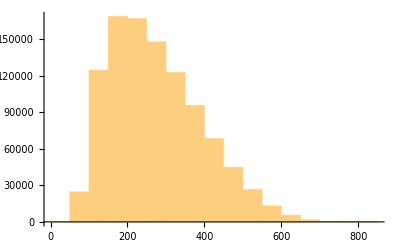

810

148

```mathematica
StringSplit/@TrainSet$data8$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data8_valid.txt",TrainSet$data8$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_test.txt",TrainSet$data8$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_train.txt",TrainSet$data8$format3⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data8_valid.txt

../../dataset_storage/on_the_paper/dataset/data8_test.txt

../../dataset_storage/on_the_paper/dataset/data8_train.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 2) / Collect Test ( Data 6 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

-375 a[0]^9+225 a[0]^8 a[1]-45 a[0]^7 a[1]^2-222 a[0]^6 a[1]^3+490 a[0]^5 a[1]^4-89 a[0]^4 a[1]^5-45 a[0]^3 a[1]^6-231 a[0]^2 a[1]^7-3 a[1]^9 | 3 b[0]^3-5 b[0] b[2]^2+4 b[1] b[2]^2 | -5 a[0]^3+a[0]^2 a[1]-a[1]^3 | -5 a[1]^3 | -4 a[0] a[1]^2

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[1250000];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

1223501

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

5406265784

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[1080000];
Length[TrainSet$3var$33$format3]
```

1080000

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Plus[Times[-10,a[0]],Times[40,Power[a[0],2]],Times[-5,a[1]],Times[18,a[0],a[1]],Times[-16,Power[a[0],2],a[1]],Times[2,Power[a[1],2]],Times[-8,a[0],Power[a[1],2]],Times[8,Power[a[0],2],Power[a[1],2]]],Inactive[Plus][Times[32,Power[a[0],2]],Times[-5,a[1]],Times[-10,a[0]],Times[10,a[0],a[1]],Times[2,Power[a[1],2]],Times[4,a[0],a[1]],Times[-4,a[0],Power[a[1],2]],Times[4,a[0],a[1]],Times[8,Power[a[0],2]],Times[-8,Power[a[0],2],a[1]],Times[-4,a[0],Power[a[1],2]],Times[-8,Power[a[0],2],a[1]],Times[8,Power[a[0],2],Power[a[1],2]]],Plus[Times[2,Power[b[0],2]],Times[-5,b[1]],Times[2,Power[b[1],2]]],Times[4,a[0]],Plus[Times[2,a[0]],a[1],Times[-2,a[0],a[1]]]]

```mathematica
Length[TrainSet$3var$33$format3]
```

1080000

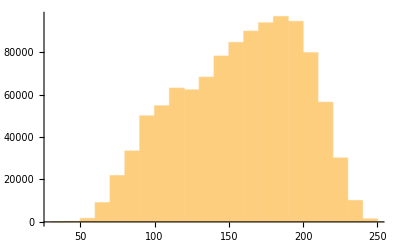

250

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=1024&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

1080000

-Graphics-

250

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data6_valid.txt",TrainSet$3var$33$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data6_test.txt",TrainSet$3var$33$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data6_train.txt",TrainSet$3var$33$format3$reduced⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data6_valid.txt

../../dataset_storage/on_the_paper/dataset/data6_test.txt

../../dataset_storage/on_the_paper/dataset/data6_train.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 4) / Collect Test ( Data 7 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2], a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

125 a[1]^6 a[2]^3+32 a[0]^2 a[1]^3 a[2]^4+75 a[1]^5 a[2]^4+32 a[0] a[1]^3 a[2]^5+15 a[1]^4 a[2]^5+a[1]^3 a[2]^6+150 a[1]^4 a[2]^4 a[3]+32 a[0] a[1]^2 a[2]^5 a[3]+60 a[1]^3 a[2]^5 a[3]+22 a[1]^2 a[2]^6 a[3]+60 a[1]^2 a[2]^5 a[3]^2+20 a[1] a[2]^6 a[3]^2+8 a[2]^6 a[3]^3 | -b[1]^3-2 b[0]^2 b[2]+b[0] b[2]^2 | 2 a[1] a[2]^2 | -5 a[1]^2 a[2]-a[1] a[2]^2-2 a[2]^2 a[3] | -4 a[0] a[1] a[2]-2 a[2]^2 a[3]

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[1050000];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

1047201

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

8855619896

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[1040000];
Length[TrainSet$3var$33$format3]
```

1040000

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Plus[Times[15,Power[a[0],2]],Times[2,a[1]]],Inactive[Plus][Times[15,Power[a[0],2]],Times[2,a[1]]],Plus[Times[-5,b[0]],Times[-1,b[1]]],Times[-3,Power[a[0],2]],Times[-2,a[1]]]

```mathematica
Length[TrainSet$3var$33$format3]
```

1040000

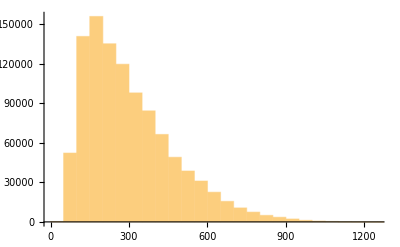

1296

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

1031076

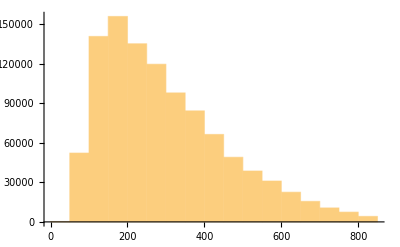

840

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=840&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data7_valid.txt",TrainSet$3var$33$format3$reduced⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data7_test.txt",TrainSet$3var$33$format3$reduced⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data7_train.txt",TrainSet$3var$33$format3$reduced⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data7_valid.txt

../../dataset_storage/on_the_paper/dataset/data7_test.txt

../../dataset_storage/on_the_paper/dataset/data7_train.txt

### Data 4, 5, 6, 7 For MMA Leaf Count

```mathematica
ClearAll[processRowGeneralized];
processRowGeneralized[row_]:=Module[{sub,replRules,countSub,countSimplified,numSubstitutions},numSubstitutions=Length[row]-2;
replRules=Table[b[i-1]->row[[-numSubstitutions+i-1]],{i,numSubstitutions}];
sub=row[[2]]/. replRules;
countSub=Length[Cases[sub,_Integer,{0,Infinity}]];
countSimplified=Length[Cases[FullSimplify[row[[1]]],_Integer,{0,Infinity}]];
(*Print[sub];
Print[FullSimplify[row[[1]]]];
Print[countSub];
Print[countSimplified];*)
{row[[1]],countSub,countSimplified}]
```

### Leaf Count

#### Short (5, 3, 3, 2) / Sub (5, 3, 3, 3) / Collect Test ( Data 4 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$data4$CommonSet = GenerateTrainSet$data4$CommonSet[300];
```

```mathematica
TrainSet$data4$CommonSet = DeleteDuplicatesBy[TrainSet$data4$CommonSet,First];
Length[TrainSet$data4$CommonSet]
```

300

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data4$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2}=TrainSet$data4$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2];
{original}],{i,Min[n,Length[TrainSet$data4$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data4$format3=GenerateTrainSet$data4$CommonSet$format3[1080000];
Length[TrainSet$data4$format3]
```

300

```mathematica
res=Map[processRowGeneralized,TrainSet$data4$CommonSet];
GenerateTrainSet$data4leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data4$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data4leaf$format3 = GenerateTrainSet$data4leaf$CommonSet$format3[300];
```

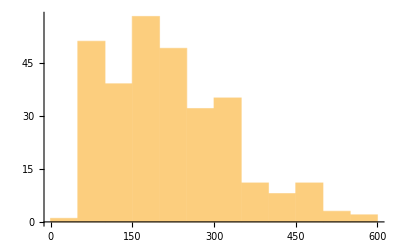

564

83

```mathematica
StringSplit/@TrainSet$data4$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data4_test_2.txt",TrainSet$data4$format3⟦1;;300⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_test_2_leafcount.txt",TrainSet$data4leaf$format3⟦1;;300⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data4_test_2.txt

../../dataset_storage/on_the_paper/dataset/data4_test_2_leafcount.txt

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data4_valid.txt",TrainSet$data4$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_test.txt",TrainSet$data4$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_train.txt",TrainSet$data4$format3⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data4_valid.txt

../../dataset_storage/on_the_paper/dataset/data4_test.txt

../../dataset_storage/on_the_paper/dataset/data4_train.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 3) / Collect Test ( Data 5 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data5$CommonSet[3]//TableForm
```

-a[0]^6 a[1] a[2]^2-4 a[0]^4 a[1]^2 a[2]^3-16 a[0]^3 a[1]^3 a[2]^3+2 a[0]^4 a[2]^5 | b[0] b[1]^2+b[1] b[2]^2-2 b[2]^3 | -a[0]^2 a[1]+2 a[2]^3 | -a[0]^2 a[2] | 2 a[0] a[1] a[2]
80 a[0]^8 a[2]-80 a[0]^7 a[1] a[2]+20 a[0]^6 a[1]^2 a[2]+400 a[0]^5 a[1]^3 a[2]-200 a[0]^4 a[1]^4 a[2]-200 a[0]^7 a[2]^2+100 a[0]^6 a[1] a[2]^2 | b[0]^2 b[1]+5 b[0] b[1] b[2] | -4 a[0]^3+2 a[0]^2 a[1] | 5 a[0]^2 a[2] | -4 a[1]^3+2 a[0]^2 a[2]
45 a[0]^3 a[1]^4 a[2]^2-225 a[0]^4 a[1]^2 a[2]^3+45 a[0]^2 a[1]^2 a[2]^5+250 a[2]^9 | 5 b[0]^2 b[1]+b[0]^2 b[2]+2 b[2]^3 | -3 a[0] a[1] a[2] | a[0] a[1]^2-5 a[0]^2 a[2] | 5 a[2]^3

```mathematica
TrainSet$data5$CommonSet = GenerateTrainSet$data5$CommonSet[300];
```

```mathematica
TrainSet$data5$CommonSet = DeleteDuplicatesBy[TrainSet$data5$CommonSet,First];
Length[TrainSet$data5$CommonSet]
```

300

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data5$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$data5$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$data5$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data5$format3=GenerateTrainSet$data5$CommonSet$format3[1020000];
Length[TrainSet$data5$format3]
```

300

```mathematica
res=Map[processRowGeneralized,TrainSet$data5$CommonSet];
GenerateTrainSet$data5leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data5$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data5leaf$format3 = GenerateTrainSet$data5leaf$CommonSet$format3[300];
```

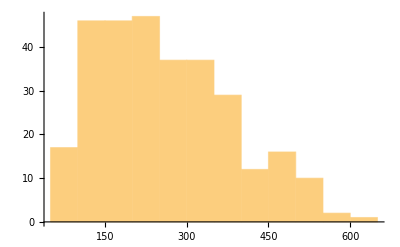

619

111

```mathematica
StringSplit/@TrainSet$data5$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data5_test_2.txt",TrainSet$data5$format3⟦1;;300⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data5_test_2_leafcount.txt",TrainSet$data5leaf$format3⟦1;;300⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data5_test_2.txt

../../dataset_storage/on_the_paper/dataset/data5_test_2_leafcount.txt

#### Short (5, 3, 3, 4) / Sub (5, 3, 3, 3) / Collect Test ( Data 8 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data8$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2], b[3]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data8$CommonSet[3]//TableForm
```

-18 a[0]^3 a[1]^2 a[2]^4+27 a[0]^2 a[1]^3 a[2]^4+18 a[0] a[1]^2 a[2]^6 | 3 b[1] b[2] b[3]-3 b[1] b[3]^2+b[2] b[3]^2 | 2 a[1] a[2]^2 | -a[0]^2 a[1] | 2 a[0] a[2]^2 | 3 a[1] a[2]^2
625 a[0]^8 a[1]-300 a[0]^7 a[1]^2+500 a[0]^6 a[1]^3+27 a[0]^5 a[1]^4-90 a[0]^4 a[1]^5+75 a[0]^3 a[1]^6-81 a[0]^4 a[1]^4 a[2]+270 a[0]^3 a[1]^5 a[2]-225 a[0]^2 a[1]^6 a[2]-625 a[0]^7 a[2]^2+300 a[0]^6 a[1] a[2]^2-1250 a[0]^5 a[1]^2 a[2]^2+180 a[0]^4 a[1]^3 a[2]^2-300 a[0]^3 a[1]^4 a[2]^2-500 a[0]^5 a[1] a[2]^3+90 a[0]^3 a[1]^3 a[2]^3-150 a[0]^2 a[1]^4 a[2]^3+750 a[0]^4 a[1] a[2]^4-180 a[0]^3 a[1]^2 a[2]^4+255 a[0]^2 a[1]^3 a[2]^4+450 a[0] a[1]^4 a[2]^4+500 a[0]^4 a[2]^5+300 a[0]^2 a[1]^2 a[2]^5-150 a[0] a[1]^2 a[2]^6-300 a[0] a[1] a[2]^7-225 a[1]^2 a[2]^7 | 3 b[0]^2 b[1]+4 b[0] b[2] b[3]+5 b[2] b[3]^2 | 3 a[0]^2 a[1]-5 a[0] a[1]^2+5 a[2]^3 | a[0] a[1]^2-3 a[1]^2 a[2] | 5 a[0]^2 a[1]-5 a[0] a[2]^2 | -5 a[0]^3+3 a[1] a[2]^2
-32 a[0]^9-8 a[0]^8 a[1]-8 a[0]^6 a[1]^3+12 a[0]^8 a[2]+36 a[0]^6 a[1]^2 a[2]-20 a[0]^7 a[2]^2-54 a[0]^6 a[1] a[2]^2-60 a[0]^5 a[1]^2 a[2]^2-117 a[0]^6 a[2]^3+156 a[0]^5 a[1] a[2]^3-99 a[0]^5 a[2]^4-150 a[0]^4 a[1] a[2]^4+165 a[0]^4 a[2]^5-341 a[0]^3 a[2]^6-18 a[0]^2 a[1] a[2]^6+27 a[0]^2 a[2]^7-45 a[0] a[2]^8-108 a[2]^9 | -b[0]^3-b[0] b[2]^2-4 b[2]^3 | 2 a[0]^2 a[1]-3 a[0]^2 a[2]+5 a[0] a[2]^2 | -4 a[1]^3+2 a[2]^3 | 2 a[0]^3+3 a[2]^3 | 3 a[0]^2 a[1]

```mathematica
TrainSet$data8$CommonSet = GenerateTrainSet$data8$CommonSet[300];
```

```mathematica
TrainSet$data8$CommonSet = DeleteDuplicatesBy[TrainSet$data8$CommonSet,First];
Length[TrainSet$data8$CommonSet]
```

300

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data8$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3,sub4}=TrainSet$data8$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3]<>" & "<>MMAExprToJFStringNonExpand[sub4];
{original}],{i,Min[n,Length[TrainSet$data8$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data8$format3=GenerateTrainSet$data8$CommonSet$format3[1010000];
Length[TrainSet$data8$format3]
```

300

```mathematica
res=Map[processRowGeneralized,TrainSet$data8$CommonSet];
GenerateTrainSet$data8leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data8$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data8leaf$format3 = GenerateTrainSet$data8leaf$CommonSet$format3[300];
```

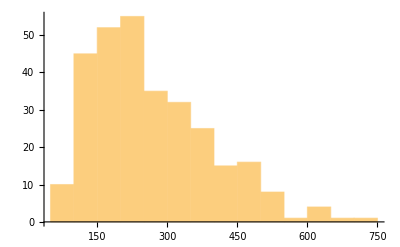

745

144

```mathematica
StringSplit/@TrainSet$data8$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data8_valid.txt",TrainSet$data8$format3⟦1;;128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_test.txt",TrainSet$data8$format3⟦129;;3128⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_train.txt",TrainSet$data8$format3⟦3129;;1003128⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data8_valid.txt

../../dataset_storage/on_the_paper/dataset/data8_test.txt

../../dataset_storage/on_the_paper/dataset/data8_train.txt

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data8_test_2.txt",TrainSet$data8$format3⟦1;;300⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_test_2_leafcount.txt",TrainSet$data8leaf$format3⟦1;;300⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data8_test_2.txt

../../dataset_storage/on_the_paper/dataset/data8_test_2_leafcount.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 2) / Collect Test ( Data 6 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

2 a[0]^9+4 a[0]^8 a[1]+2 a[0]^7 a[1]^2-20 a[0]^6 a[1]^3-20 a[0]^5 a[1]^4+50 a[0]^3 a[1]^6+2 a[1]^9 | 2 b[1]^3+2 b[0]^2 b[2] | a[0]^3+a[0]^2 a[1]-5 a[1]^3 | a[1]^3 | a[0]^3

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[300];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

300

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

1306792

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[300];
Length[TrainSet$3var$33$format3]
```

300

```mathematica
res=Map[processRowGeneralized,TrainSet$3var$33$CommonSet];
GenerateTrainSet$data6leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$3var$33$format3]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data6leaf$format3 = GenerateTrainSet$data6leaf$CommonSet$format3[300];
```

```mathematica
Length[TrainSet$3var$33$format3]
```

300

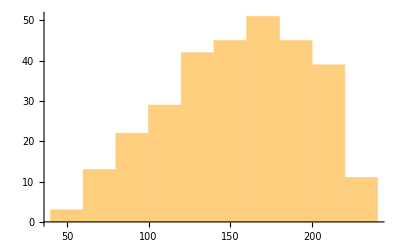

234

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=840&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

300

-Graphics-

234

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data6_test_2.txt",TrainSet$3var$33$format3⟦1;;300⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data6_test_2_leafcount.txt",TrainSet$data6leaf$format3⟦1;;300⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data6_test_2.txt

../../dataset_storage/on_the_paper/dataset/data6_test_2_leafcount.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 4) / Collect Test ( Data 7 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2], a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

75 a[0]^4 a[1]^2 a[3]^3-80 a[0]^3 a[1] a[2] a[3]^4+30 a[0]^2 a[1] a[3]^6-16 a[0] a[2] a[3]^7+3 a[3]^9 | 4 b[0] b[1] b[2]-3 b[0] b[2]^2 | -a[3]^3 | -4 a[0] a[2] a[3] | -5 a[0]^2 a[1]-a[3]^3

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[300];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

300

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

2628560

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[1040000];
Length[TrainSet$3var$33$format3]
```

300

```mathematica
res=Map[processRowGeneralized,TrainSet$3var$33$CommonSet];
GenerateTrainSet$data7leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$3var$33$format3]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data7leaf$format3 = GenerateTrainSet$data7leaf$CommonSet$format3[300];
```

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Plus[Times[10,Power[a[0],2],a[1]],Times[-18,Power[a[1],2]]],Inactive[Plus][Times[-2,Power[a[1],2]],Times[10,Power[a[0],2],a[1]],Times[-16,Power[a[1],2]]],Plus[Times[b[0],b[1]],Times[-4,Power[b[1],2]]],Plus[Times[5,Power[a[0],2]],Times[-1,a[1]]],Times[2,a[1]]]

```mathematica
Length[TrainSet$3var$33$format3]
```

300

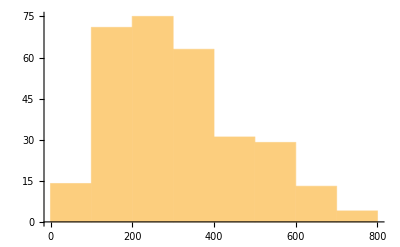

791

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=840&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

300

-Graphics-

791

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data7_test_2.txt",TrainSet$3var$33$format3$reduced⟦1;;300⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data7_test_2_leafcount.txt",TrainSet$data7leaf$format3⟦1;;300⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data7_test_2.txt

../../dataset_storage/on_the_paper/dataset/data7_test_2_leafcount.txt

### Vertex Count of DAG

```mathematica
express=4+2 (-2-y-xy)^2+(-2-y-xy)^3
```

```mathematica
4+2 (-2-xy-y)^2+(-2-xy-y)^3
```

4+2 (-2-xy-y)^2+(-2-xy-y)^3

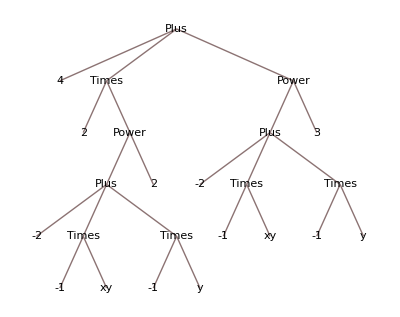

```mathematica
express//TreeForm
```

```mathematica
express=4+2  (-2-y-xy)^2+(-2-y-xy)^3
all$subexpression$pos=Position[express,a_/;LeafCount[a]>=1]
all$subexpression=Table[express[[Sequence@@all$subexpression$pos[[i]]]],{i,Length@all$subexpression$pos}]
Table[{pos,hash}={all$subexpression$pos[[i]],Hash[all$subexpression[[i]]]},{i,Length@all$subexpression$pos}]//GatherBy[#,Last]&//Map[First[#][[2]]->Map[First,#]&]//Length
```

```mathematica
DAGVertexCount[expr_]:=Module[{all$subexpression$pos,all$subexpression},all$subexpression$pos=Position[expr,a_/;LeafCount[a]>=1];
all$subexpression=Table[expr[[Sequence@@all$subexpression$pos[[i]]]],{i,Length@all$subexpression$pos}];
Table[{pos,hash}={all$subexpression$pos[[i]],Hash[all$subexpression[[i]]]},{i,Length@all$subexpression$pos}]//GatherBy[#,Last]&//Map[First[#][[2]]->Map[First,#]&]//Length]
expr=4+2 (-2-y-xy)^2+(-2-y-xy)^3
DAGVertexCount[expr]
```

4+2 (-2-xy-y)^2+(-2-xy-y)^3

17

```mathematica
ClearAll[processRowGeneralizedDAG];
processRowGeneralizedDAG[row_]:=Module[{sub,replRules,countSub,countSimplified,numSubstitutions},numSubstitutions=Length[row]-2;
replRules=Table[b[i-1]->row[[-numSubstitutions+i-1]],{i,numSubstitutions}];
sub=row[[2]]/. replRules;
countSub=DAGVertexCount[sub]; Length[Cases[sub,_Integer,{0,Infinity}]];
countSimplified=DAGVertexCount[FullSimplify[row[[1]]]];
(*Print[sub];
Print[FullSimplify[row[[1]]]];
Print[countSub];
Print[countSimplified];*)
{row[[1]],countSub,countSimplified}]
```

```mathematica
ClearAll[filterDatasets];
filterDatasets[dataset1_,maxLength_:850]:=Module[{saveIndices={},n=Length[dataset1]},(*Loop through dataset1 and collect indices where length criterion is met*)For[i=1,i<=n,i++,If[Length[StringSplit[dataset1[[i]]]]<=maxLength,AppendTo[saveIndices,i]; ]];
{saveIndices}]
```

#### Short (5, 3, 3, 2) / Sub (5, 3, 3, 3) / Collect Test ( Data 4 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data4$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
TrainSet$data4$CommonSet = GenerateTrainSet$data4$CommonSet[1500];
```

```mathematica
TrainSet$data4$CommonSet = DeleteDuplicatesBy[TrainSet$data4$CommonSet,First];
Length[TrainSet$data4$CommonSet]
```

1500

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data4$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2}=TrainSet$data4$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2];
{original}],{i,Min[n,Length[TrainSet$data4$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data4$format3=GenerateTrainSet$data4$CommonSet$format3[1080000];
Length[TrainSet$data4$format3]
```

1500

```mathematica
res=Map[processRowGeneralizedDAG,TrainSet$data4$CommonSet];
GenerateTrainSet$data4leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data4$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data4leaf$format3 = GenerateTrainSet$data4leaf$CommonSet$format3[1500];
```

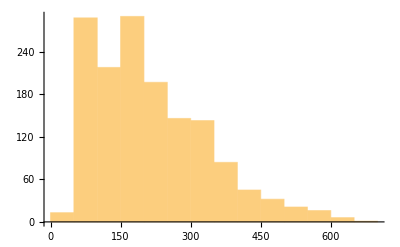

652

87

```mathematica
StringSplit/@TrainSet$data4$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data4_test_DAG_large.txt",TrainSet$data4$format3⟦1;;1200⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data4_test_DAG_leafcount_large.txt",TrainSet$data4leaf$format3⟦1;;1200⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data4_test_DAG_large.txt

../../dataset_storage/on_the_paper/dataset/data4_test_DAG_leafcount_large.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 3) / Collect Test ( Data 5 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data5$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data5$CommonSet[3]//TableForm
```

24 a[0]^3 a[1]^6-144 a[0]^2 a[1]^6 a[2]+288 a[0] a[1]^6 a[2]^2-8 a[0]^6 a[2]^3+60 a[0]^4 a[1]^2 a[2]^3-150 a[0]^2 a[1]^4 a[2]^3-67 a[1]^6 a[2]^3-12 a[0]^4 a[2]^5+60 a[0]^2 a[1]^2 a[2]^5-75 a[1]^4 a[2]^5-2 a[0]^3 a[2]^6-6 a[0]^2 a[2]^7+15 a[1]^2 a[2]^7-a[2]^9 | -3 b[0]^3+b[1]^3+2 b[2]^3 | -2 a[0] a[1]^2+4 a[1]^2 a[2] | -2 a[0]^2 a[2]+5 a[1]^2 a[2]-a[2]^3 | -a[0] a[2]^2
-500 a[0]^6 a[1]^3+256 a[1]^9-400 a[0]^3 a[1]^5 a[2]-160 a[0]^5 a[1]^2 a[2]^2+600 a[0]^4 a[1]^3 a[2]^2-80 a[1]^7 a[2]^2-160 a[0]^5 a[1] a[2]^3-64 a[0]^2 a[1]^4 a[2]^3+240 a[0] a[1]^5 a[2]^3-40 a[0]^5 a[2]^4+96 a[0]^3 a[1]^2 a[2]^4-244 a[0]^2 a[1]^3 a[2]^4+96 a[0]^3 a[1] a[2]^5-16 a[0]^2 a[1]^2 a[2]^5+24 a[0]^3 a[2]^6 | -2 b[0]^2 b[1]-5 b[1]^2 b[2]+4 b[2]^3 | -4 a[0] a[1] a[2]-2 a[0] a[2]^2 | 5 a[0]^3+2 a[1]^2 a[2]-3 a[0] a[2]^2 | 4 a[1]^3
-256 a[0]^5 a[1]^2 a[2]^2+128 a[0]^3 a[1]^3 a[2]^3+160 a[0]^4 a[1] a[2]^4-16 a[0] a[1]^4 a[2]^4-40 a[0]^2 a[1]^2 a[2]^5 | -2 b[0] b[1] b[2]+b[1]^2 b[2]+4 b[1] b[2]^2 | 3 a[0] a[2]^2 | -4 a[0] a[2]^2 | 4 a[0]^2 a[1]-a[1]^2 a[2]

```mathematica
TrainSet$data5$CommonSet = GenerateTrainSet$data5$CommonSet[1500];
```

```mathematica
TrainSet$data5$CommonSet = DeleteDuplicatesBy[TrainSet$data5$CommonSet,First];
Length[TrainSet$data5$CommonSet]
```

1500

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data5$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$data5$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$data5$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data5$format3=GenerateTrainSet$data5$CommonSet$format3[1020000];
Length[TrainSet$data5$format3]
```

1500

```mathematica
res=Map[processRowGeneralizedDAG,TrainSet$data5$CommonSet];
GenerateTrainSet$data5leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data5$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data5leaf$format3 = GenerateTrainSet$data5leaf$CommonSet$format3[1500];
```

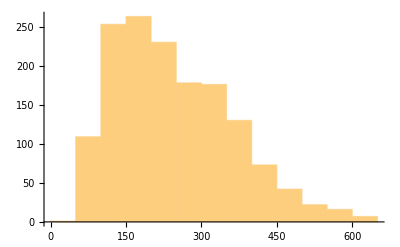

647

114

```mathematica
StringSplit/@TrainSet$data5$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data5_test_DAG_large.txt",TrainSet$data5$format3⟦1;;1200⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data5_test_DAG_leafcount_large.txt",TrainSet$data5leaf$format3⟦1;;1200⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data5_test_DAG_large.txt

../../dataset_storage/on_the_paper/dataset/data5_test_DAG_leafcount_large.txt

#### Short (5, 3, 3, 4) / Sub (5, 3, 3, 3) / Collect Test ( Data 8 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$data8$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2], b[3]},{a[0],a[1],a[2]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$data8$CommonSet[3]//TableForm
```

-32 a[1]^6 a[2]^3+54 a[0]^2 a[1]^2 a[2]^5-18 a[1]^2 a[2]^7 | -4 b[1]^3-b[1] b[2]^2+3 b[1] b[3]^2 | 5 a[0]^3+2 a[1]^3 | 2 a[1]^2 a[2] | -3 a[2]^3 | 3 a[0] a[2]^2
225 a[0]^6 a[1] a[2]^2-54 a[0]^6 a[2]^3 | -5 b[0] b[3]^2-2 b[3]^3 | -5 a[0]^2 a[1] | -3 a[1]^2 a[2]+a[1] a[2]^2 | -3 a[0] a[1]^2+a[0] a[2]^2 | 3 a[0]^2 a[2]
-20 a[1]^8 a[2]-14 a[0]^2 a[1]^5 a[2]^2-5 a[0] a[1]^6 a[2]^2-80 a[1]^7 a[2]^2-12 a[0]^2 a[1]^4 a[2]^3+68 a[0] a[1]^5 a[2]^3-80 a[1]^6 a[2]^3+42 a[0]^3 a[1]^2 a[2]^4+62 a[0]^2 a[1]^3 a[2]^4+188 a[0] a[1]^4 a[2]^4-8 a[1]^5 a[2]^4-48 a[0]^3 a[1] a[2]^5-24 a[0]^2 a[1]^2 a[2]^5+64 a[0] a[1]^3 a[2]^5-16 a[1]^4 a[2]^5-45 a[0]^3 a[2]^6-96 a[0]^2 a[1] a[2]^6+24 a[0] a[1]^2 a[2]^6 | -4 b[0] b[1] b[2]-2 b[1]^2 b[2]-5 b[2]^2 b[3] | 3 a[0] a[1] a[2]-4 a[0] a[2]^2 | a[0] a[1] a[2]+2 a[1] a[2]^2 | a[1]^3+2 a[1]^2 a[2]-3 a[0] a[2]^2 | 4 a[1]^2 a[2]+a[0] a[2]^2

```mathematica
TrainSet$data8$CommonSet = GenerateTrainSet$data8$CommonSet[1500];
```

```mathematica
TrainSet$data8$CommonSet = DeleteDuplicatesBy[TrainSet$data8$CommonSet,First];
Length[TrainSet$data8$CommonSet]
```

1500

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$data8$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,sub4,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3,sub4}=TrainSet$data8$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3]<>" & "<>MMAExprToJFStringNonExpand[sub4];
{original}],{i,Min[n,Length[TrainSet$data8$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data8$format3=GenerateTrainSet$data8$CommonSet$format3[1010000];
Length[TrainSet$data8$format3]
```

1500

```mathematica
res=Map[processRowGeneralizedDAG,TrainSet$data8$CommonSet];
GenerateTrainSet$data8leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$data8$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data8leaf$format3 = GenerateTrainSet$data8leaf$CommonSet$format3[1500];
```

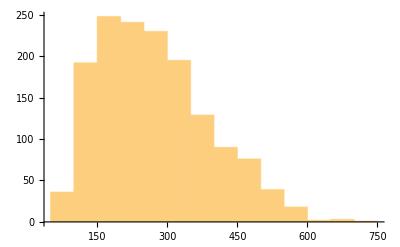

722

141

```mathematica
StringSplit/@TrainSet$data8$format3;
Length/@%//Histogram
Length/@%%//Max
Map[Function[sublist,Part[sublist,Position[sublist,"?"][[1,1]]+1;;]],%%%];
Length/@%//Max
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data8_test_DAG_large.txt",TrainSet$data8$format3⟦1;;1200⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data8_test_DAG_leafcount_large.txt",TrainSet$data8leaf$format3⟦1;;1200⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data8_test_DAG_large.txt

../../dataset_storage/on_the_paper/dataset/data8_test_DAG_leafcount_large.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 2) / Collect Test ( Data 6 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

-26 a[0]^7 a[1]^2-108 a[0]^6 a[1]^3-18 a[0]^5 a[1]^4+120 a[0]^4 a[1]^5-40 a[0]^3 a[1]^6 | -b[0]^2 b[2]+2 b[1] b[2]^2 | -4 a[0]^2 a[1] | -5 a[0] a[1]^2 | a[0]^3+3 a[0]^2 a[1]-2 a[0] a[1]^2

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[1500];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

1500

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

6551736

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[1500];
Length[TrainSet$3var$33$format3]
```

1500

```mathematica
res=Map[processRowGeneralizedDAG,TrainSet$3var$33$CommonSet];
GenerateTrainSet$data6leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$3var$33$format3]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data6leaf$format3 = GenerateTrainSet$data6leaf$CommonSet$format3[1500];
```

```mathematica
Length[TrainSet$3var$33$format3]
```

1500

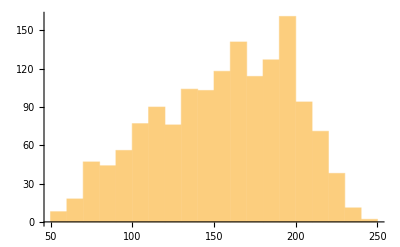

241

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=840&];
Length[%]
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Histogram
Length/@StringSplit/@TrainSet$3var$33$format3$reduced//Max
```

1500

-Graphics-

241

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data6_test_DAG_large.txt",TrainSet$3var$33$format3⟦1;;1200⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data6_test_DAG_leafcount_large.txt",TrainSet$data6leaf$format3⟦1;;1200⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data6_test_DAG_large.txt

../../dataset_storage/on_the_paper/dataset/data6_test_DAG_leafcount_large.txt

#### Short (5, 3, 3, 3) / Sub (5, 3, 3, 4) / Collect Test ( Data 7 )

```mathematica
(* both original and substitution has fixed degree terms / original has a varying number of terms while substitution is not *)
```

```mathematica
(* Common Set *)
```

```mathematica
totatCases =1200;
Get["MMA2TxtFormat3.m"];
GenerateTrainSet$3var$33$CommonSet[n_]:=
Monitor[
Table[RandomPolynomial$PolyNInPoly6$LSS[5,3,5,3,{b[0],b[1],b[2]},{a[0],a[1],a[2], a[3]},3,3],{i,n}],
Row[{"Generating element: ", i}]
];
```

```mathematica
GenerateTrainSet$3var$33$CommonSet[1]//TableForm
```

-125 a[2]^9+375 a[0] a[2]^6 a[3]^2-240 a[0]^3 a[3]^6+120 a[0]^2 a[2] a[3]^6-15 a[0] a[2]^2 a[3]^6+240 a[0]^2 a[3]^7-60 a[0] a[2] a[3]^7-60 a[0] a[3]^8 | 5 b[0] b[1]^2-b[1]^3-5 b[0] b[2]^2 | 3 a[0] a[3]^2 | 5 a[2]^3 | -4 a[0] a[3]^2+a[2] a[3]^2+2 a[3]^3

```mathematica
TrainSet$3var$33$CommonSet = GenerateTrainSet$3var$33$CommonSet[totatCases + 500];
```

```mathematica
TrainSet$3var$33$CommonSet = DeleteDuplicatesBy[TrainSet$3var$33$CommonSet,First];
Length[TrainSet$3var$33$CommonSet]
```

1700

```mathematica
ByteCount[TrainSet$3var$33$CommonSet]
```

14274472

```mathematica
$RecursionLimit=100000;
```

```mathematica
(* change to format3 *)
```

```mathematica
GenerateTrainSet$3var$33$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{longExpand,longShort,short,sub1,sub2,sub3,original,distributed},(*Read from existing table instead of generating*){expandedForm,short,sub1,sub2,sub3}=TrainSet$3var$33$CommonSet[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" ? "<>MMAExprToJFStringNonExpand[short]<>" & "<>MMAExprToJFStringNonExpand[sub1]<>" & "<>MMAExprToJFStringNonExpand[sub2]<>" & "<>MMAExprToJFStringNonExpand[sub3];
{original}],{i,Min[n,Length[TrainSet$3var$33$CommonSet]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$3var$33$format3=GenerateTrainSet$3var$33$CommonSet$format3[1040000];
Length[TrainSet$3var$33$format3]
```

1700

```mathematica
res=Map[processRowGeneralizedDAG,TrainSet$3var$33$CommonSet];
GenerateTrainSet$data7leaf$CommonSet$format3[n_]:=Monitor[Flatten[Table[Module[{short,subCount,simplifyCount,original},(*Read from existing table instead of generating*){expandedForm,subCount, simplifyCount}=res[[i]];
original=MMAExprToJFStringNonExpand[expandedForm]<>" & "<> ToString[subCount] <>" & "<>ToString[simplifyCount];
{original}],{i,Min[n,Length[TrainSet$3var$33$format3]]}],1],Row[{"Processing element: ",i}]]
```

```mathematica
TrainSet$data7leaf$format3 = GenerateTrainSet$data7leaf$CommonSet$format3[totatCases+500];
```

```mathematica
FullForm[RandomPolynomialWithDistribute$PolyNInPoly4$LSS[5,2,5,2,{a[0],a[1]},3,3]]
```

List[Plus[Times[-2,Power[a[0],2]],Times[-12,Power[a[0],3]],Times[-16,Power[a[0],4]],Times[-4,Power[a[0],2],a[1]],Times[-8,Power[a[0],3],a[1]]],Inactive[Plus][Times[-8,Power[a[0],4]],Times[-4,Power[a[0],3]],Times[-4,Power[a[0],3]],Times[-2,Power[a[0],2]],Times[-4,Power[a[0],3]],Times[-4,Power[a[0],2],a[1]],Times[-8,Power[a[0],4]],Times[-8,Power[a[0],3],a[1]]],Plus[Times[-2,b[0],b[1]],Times[-2,Power[b[1],2]]],Plus[Times[-2,Power[a[0],2]],Times[-2,a[0],a[1]]],Plus[Times[-1,a[0]],Times[-2,Power[a[0],2]]]]

```mathematica
Length[TrainSet$3var$33$format3]
```

1700

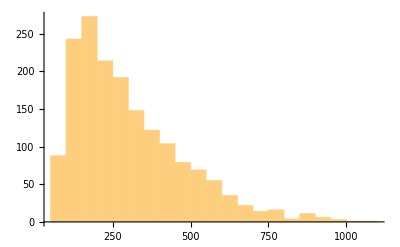

1090

```mathematica
Length/@StringSplit/@TrainSet$3var$33$format3;
%//Histogram
%%//Max
```

```mathematica
(*TrainSet$3var$33$format3$reduced=Select[TrainSet$3var$33$format3,Length[StringSplit[#]]<=850&]*)
{saveIndices}=filterDatasets[TrainSet$3var$33$format3];
TrainSet$3var$33$format3$reduced = TrainSet$3var$33$format3[[saveIndices]];
TrainSet$data7leaf$format3$reduced = TrainSet$data7leaf$format3[[saveIndices]];
```

1678

1678

```mathematica
Length[TrainSet$3var$33$format3$reduced]
```

2

```mathematica
SetDirectory[NotebookDirectory[]]
Export["../../dataset_storage/on_the_paper/dataset/data7_test_DAG_large.txt",TrainSet$3var$33$format3$reduced⟦1;;1200⟧,"Text"]
Export["../../dataset_storage/on_the_paper/dataset/data7_test_DAG_leafcount_large.txt",TrainSet$data7leaf$format3$reduced⟦1;;1200⟧,"Text"]
```

/Users/giohuh/Code/geo-179/inequality/MMA_package

../../dataset_storage/on_the_paper/dataset/data7_test_DAG_large.txt

../../dataset_storage/on_the_paper/dataset/data7_test_DAG_leafcount_large.txt

## evaluate result

### ~ Exp 53

#### Example of usage ( Exp33 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33/experiment33_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
testdata[[1;;3]]
```

{{1700-165 a[1]+4 a[1]^2,-20+a[1]},{-51+3 a[1],-17+a[1]},{-8-60 a[1]-94 a[1]^2+20 a[1]^3-a[1]^4,-2-10 a[1]+a[1]^2}}

```mathematica
predictiondata[[1;;3]]
```

{-20+a[1],-17+a[1],-4-10 a[1]+a[1]^2}

```mathematica
simplification$result=Table[PolySimplifyWithHint[{testdata[[i,1]],predictiondata[[i]]},False,True],{i,1,Length@predictiondata}];
```

```mathematica
simplification$result[[1;;3]]
```

{-5 s+4 s^2,3 s,-2 s-s^2}

```mathematica
(* percentage of grammatic error *)
pctg$grammaticerr=Count[predictiondata,False]/Length[predictiondata]//N
```

0.000666667

```mathematica
(* percentage of wrong cases, excluding grammatic error *)
pctg$wrong=Count[simplification$result,False]/Length[simplification$result]-pctg$grammaticerr//N
```

0.00766667

```mathematica
(* percentage of correct cases*)
pctg$correct=1-Count[simplification$result,False]/Length[simplification$result]//N
```

0.991667

```mathematica
(* package above code into a function *)
EvaluateSimplificationResult[testfile_,predictionfile_,complexityCriteriaQ_:True,eliminateQ_:True]:=Module[
{testdata,predictiondata,simplification$result,pctg$grammaticerr,pctg$wrong,pctg$correct},
testdata=TestData$FromFile[testfile];
predictiondata=PredictionData$FromFile[predictionfile];
simplification$result=Table[PolySimplifyWithHint[{testdata[[i,1]],predictiondata[[i]]},complexityCriteriaQ,eliminateQ],{i,1,Length@predictiondata}];

pctg$grammaticerr=Count[predictiondata,False]/Length[predictiondata]//N;
pctg$wrong=Count[simplification$result,False]/Length[simplification$result]-pctg$grammaticerr//N;
pctg$correct=1-Count[simplification$result,False]/Length[simplification$result]//N;

{pctg$grammaticerr,pctg$wrong,pctg$correct}
];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
EvaluateSimplificationResult["./Evaluation/Exp33/test_set_Exp14.txt","./Evaluation/Exp33/experiment33_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.000666667,0.00766667,0.991667}

#### Test model from Exp33 on contaminated data (test1)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33_test1/IndecomposableTest_Test1_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33_test1/experiment33_indecomposable_test1_predictions.txt"];
```

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test1/IndecomposableTest_Test1_Format3.txt","./Evaluation/Exp33_test1/experiment33_indecomposable_test1_predictions.txt"]
```

{0.,0.04,0.96}

```mathematica
testdata⟦2⟧
predictiondata⟦2⟧
```

{297+308 a[1]-1383 a[1]^2-683 a[1]^3+1845 a[1]^4-190 a[1]^5+5 a[1]^6,8+4 a[1]-19 a[1]^2+a[1]^3}

9+4 a[1]-19 a[1]^2+a[1]^3

```mathematica
PolySimplifyWithHint[{testdata[[2,1]],8+4 a[1]-19 a[1]^2+a[1]^3},False,True]
```

1-3 s+5 s^2

#### Test model from Exp33 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt"]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.001,0.731333,0.267667}

```mathematica
EvaluateSimplificationResult["./Evaluation/Exp33_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp33_test2/experiment33_indecomposable_test2_predictions.txt",True,False]
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.001,0.506,0.493}

#### Test model from Exp34 on non contaminated data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp34/test_set_Exp34.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp34/experiment34_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp34/test_set_Exp34.txt","./Evaluation/Exp34/experiment34_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
```

{0.298333,0.0303333,0.671333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp34/test_set_Exp34.txt","./Evaluation/Exp34/experiment34_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result2
```

{0.298333,0.0493333,0.652333}

#### Test model from Exp34 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result1
```

{0.115667,0.634,0.250333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp34_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp34_test2/experiment34_indecomposable_test2_predictions.txt",True,False];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

```mathematica
result2
```

{0.115667,0.703333,0.181}

#### Test model from Exp37 on non contaminated data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp37/test_set_Exp36.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp37/experiment37_predictions.txt"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp37/test_set_Exp36.txt","./Evaluation/Exp37/experiment37_predictions.txt"];
```

```mathematica
result1
```

{0.,0.0113333,0.988667}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp37/test_set_Exp36.txt","./Evaluation/Exp37/experiment37_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.011,0.989}

#### Test model from Exp37 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
```

{0.0136667,0.984667,0.00166667}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp37_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp37_test2/experiment37_indecomposable_test2_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result2
```

{0.0136667,0.501,0.485333}

#### Random suggestion benchmark

```mathematica
testdata⟦1⟧
predictiondata⟦1⟧
```

{480-97 a[1]+1867 a[1]^2-876 a[1]^3+1777 a[1]^4-1320 a[1]^5+55 a[1]^6+70 a[1]^7+5 a[1]^8,-10+a[1]-19 a[1]^2+7 a[1]^3+a[1]^4}

-10+a[1]-19 a[1]^2+7 a[1]^3+a[1]^4

```mathematica
predictiondata[[9]]
```

6+a[1]

```mathematica
i0=16;predictiondata[[i0]]
PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i0]]},False,True]
PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i0]]},True,False]
```

-12-13 a[1]+6 a[1]^2-11 a[1]^3+a[1]^4

False

False

```mathematica
simplification$result$random=Table[PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i]]},False,True],{i,1,Length@predictiondata}];
pctg$correct$random=1-Count[simplification$result$random,False]/Length[simplification$result$random]/1.
simplification$result$random=Table[PolySimplifyWithHint[{testdata[[1,1]],predictiondata[[i]]},True,False],{i,1,Length@predictiondata}];
pctg$correct$random=1-Count[simplification$result$random,False]/Length[simplification$result$random]/1.
```

0.224667

0.000333333

#### Test model from Exp38 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38/test_set_Exp38.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38/experiment38_predictions.txt"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38/test_set_Exp38.txt","./Evaluation/Exp38/experiment38_predictions.txt"];
```

```mathematica
result1
```

{0.,1.,0.}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38/test_set_Exp38.txt","./Evaluation/Exp38/experiment38_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.920333,0.0796667}

#### Test model from Exp38 on contaminated data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
```

{0.044,0.956,0.}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38_test2/IndecomposableTest_Test2_Format3.txt","./Evaluation/Exp38_test2/experiment38_indecomposable_test2_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result2
```

{0.044,0.303,0.653}

#### Test model from Exp38 on decomposable data (test2)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp38_test0/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp38_test0/test_set_Exp14.txt","./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
```

{0.039,0.297,0.664}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp38_test0/test_set_Exp14.txt","./Evaluation/Exp38_test0/experiment38_decomposable_test_predictions.txt",True,False];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result2
```

{0.039,0.294667,0.666333}

#### Test model from Exp39 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp39/test_set_Exp39.txt","./Evaluation/Exp39/experiment39_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result1
```

{0.000333333,0.126667,0.873}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp39/test_set_Exp39.txt","./Evaluation/Exp39/experiment39_predictions.txt",True,False];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result2
```

{0.000333333,0.00366667,0.996}

#### Test model from Exp40 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp40/test_set_Exp39.txt","./Evaluation/Exp40/experiment40_predictions.txt"];
```

```mathematica
result1
```

{0.,0.0376667,0.962333}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp40/test_set_Exp39.txt","./Evaluation/Exp40/experiment40_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.001,0.999}

#### Test model from Exp41 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result1=EvaluateSimplificationResult["./Evaluation/Exp41/test_set_Exp41.txt","./Evaluation/Exp41/experiment41_predictions.txt"];
```

```mathematica
result1
```

{0.,0.001,0.999}

```mathematica
result2=EvaluateSimplificationResult["./Evaluation/Exp41/test_set_Exp41.txt","./Evaluation/Exp41/experiment41_predictions.txt",True,False];
```

```mathematica
result2
```

{0.,0.000333333,0.999667}

#### Test model from Exp44 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult2["./Evaluation/Exp44/test_set_Exp44.txt","./Evaluation/Exp44/experiment44_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
result
```

{0.,0.00633333,0.993667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp44/test_set_Exp44.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/Exp44/experiment44_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=132;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.b[0]->%⟦1⟧//Expand
```

6+21 a[1]^2 a[2]+9 a[1]^4 a[2]^2+56 a[1] a[2] a[3]+48 a[1]^3 a[2]^2 a[3]+64 a[1]^2 a[2]^2 a[3]^2

{3 a[1]^2 a[2]+8 a[1] a[2] a[3],6+7 b[0]+b[0]^2}

6+21 a[1]^2 a[2]+9 a[1]^4 a[2]^2+56 a[1] a[2] a[3]+48 a[1]^3 a[2]^2 a[3]+64 a[1]^2 a[2]^2 a[3]^2

#### Test model from Exp45 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp45/test_set_Exp45.txt","./Evaluation/Exp45/experiment45_predictions.txt"];
```

```mathematica
result
```

{0.,0.296333,0.703667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp45/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp45/experiment45_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-5 a[2]-4 a[1] a[2]+2 a[1] a[3],2 a[1]},4 b[0]^2+4 b[0] b[1]+5 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

0

#### Test model from Exp46 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp46/test_set_Exp45.txt","./Evaluation/Exp46/experiment46_predictions.txt"];
```

```mathematica
result
```

{0.,0.632,0.368}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp46/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp46/experiment46_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-2 a[1],-5 a[2]-4 a[1] a[2]-2 a[1] a[3]},5 b[0]^2-4 b[0] b[1]+4 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2-16 a[1]^2 a[3]+80 a[1] a[2] a[3]+64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

32 a[1]^2 a[3]-160 a[1] a[2] a[3]-128 a[1]^2 a[2] a[3]

#### Test model from Exp47 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp47/test_set_Exp45.txt","./Evaluation/Exp47/experiment47_predictions.txt"];
```

```mathematica
result
```

{0.,0.244333,0.755667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp46/test_set_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp47/experiment47_predictions.txt"];
```

```mathematica
index=94;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

{{-5 a[2]-4 a[1] a[2]+2 a[1] a[3],2 a[1]},4 b[0]^2+4 b[0] b[1]+5 b[1]^2}

20 a[1]^2-40 a[1] a[2]-32 a[1]^2 a[2]+100 a[2]^2+160 a[1] a[2]^2+64 a[1]^2 a[2]^2+16 a[1]^2 a[3]-80 a[1] a[2] a[3]-64 a[1]^2 a[2] a[3]+16 a[1]^2 a[3]^2

0

#### Test model from Exp50 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp50/test_set_Exp50.txt","./Evaluation/Exp50/experiment50_predictions.txt"];
```

```mathematica
result
```

{0.,0.809667,0.190333}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp50/test_set_Exp50.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp50/experiment50_predictions.txt"];
```

```mathematica
index=97;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

4 a[3]^2 a[4]^2-12 a[3] a[4]^3+9 a[4]^4+4 a[3] a[4] a[5] a[6]-6 a[4]^2 a[5] a[6]-6 a[3] a[4] a[6]^2+9 a[4]^2 a[6]^2-6 a[3] a[4] a[5] a[7]+9 a[4]^2 a[5] a[7]+2 a[3] a[4] a[6] a[7]-3 a[4]^2 a[6] a[7]

{{-2 a[3] a[4]+3 a[4]^2,2 a[5] a[6]+3 a[6]^2+3 a[5] a[7]-a[6] a[7]},b[0]^2+b[0] b[1]}

4 a[3]^2 a[4]^2-12 a[3] a[4]^3+9 a[4]^4-4 a[3] a[4] a[5] a[6]+6 a[4]^2 a[5] a[6]-6 a[3] a[4] a[6]^2+9 a[4]^2 a[6]^2-6 a[3] a[4] a[5] a[7]+9 a[4]^2 a[5] a[7]+2 a[3] a[4] a[6] a[7]-3 a[4]^2 a[6] a[7]

8 a[3] a[4] a[5] a[6]-12 a[4]^2 a[5] a[6]

#### Test model from Exp48 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp48/test_set_Exp48.txt","./Evaluation/Exp48/experiment48_predictions.txt"];
```

```mathematica
result
```

{0.476667,0.,0.794333,0.205667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp48/test_set_Exp48.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp48/experiment48_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1427 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«20 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«20 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«17 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«21 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«26 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
index=100;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

False

{{4 a[1]^2,-3 a[0] a[1]},False}

False

0

#### Test model from Exp52 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp52/test_set_Exp52.txt","./Evaluation/Exp52/experiment52_predictions.txt"];
```

```mathematica
result
```

{0.,0.,0.532333,0.467667}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp52/test_set_Exp52.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/Exp52/experiment52_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«17 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«24 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«24 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

```mathematica
index=9;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}
%%%-%//Expand
```

0

{{0,-5 a[0]-a[1]^2},False}

False

-False

#### Test model from Exp53 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp53/test_set_Exp53.txt","./Evaluation/Exp53/experiment53_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.499333,0.500667}

#### Test model from Exp58 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp58/test_set_Exp58.txt","./Evaluation/Exp58/experiment58_predictions.txt"];
```

```mathematica
result
```

{0.,0.115,0.702,0.183,{False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,True,False,True,True,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,True,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,True,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,True,True,True,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,True,True,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,True,True,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,True,False,False,False,True,True,False,True,False,False,True,False,False,False,False,False,True,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,False,True,True,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,False,True,True,True,False,False,False,False,True,False,False,True,True,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,True,True,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,True,True,False,False,True,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,True,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,True,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,True,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,True,True,True,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,True,True,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,True,False,False,True,True,False,False,False,True,False,False,False,True,False,False,False,False,True,True,True,True,False,False,False,True,True,False,False,True,False,False,True,False,False,False,False,False,True,True,True,True,True,True,False,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,True,False,True,True,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,True,False,False,False,False,False,True,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,False,False,False,False,False,True,False,False,True,True,False,True,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,True,False,False,True,True,False,False,False,True,False,False,False,False,False,False,True,True,True,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,False,False,True,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,True,True,False,False,False,True,True,False,False,False,True,False,False,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,False,False,False,False,False,False,False,True,True,False,False,False,True,False,False,True,False,False,True,False,False,True,False,False,False,False,False,False,True,False,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,True,False,False,False,False,True,True,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,True,False,False,False,True,True,False,True,False,False,True,True,False,False,True,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,True,True,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,True,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False}}

### generalization evaluation

#### with pad on 0th token, move one pad

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
testdata=TestData$FromFile["./Evaluation/Exp33/test_set_Exp14.txt"];
```

```mathematica
predictiondata=PredictionData$FromFile["./Evaluation/Exp32_test/experiment32_test_predictions.txt"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
EvaluateSimplificationResult["./Evaluation/Exp33/test_set_Exp14.txt","./Evaluation/Exp32_test/experiment32_test_predictions.txt",False,True]
```

{0.,0.013,0.987}

#### Test model from Exp52, 53 on Exp45 test data (generalization 0)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen0/gen0_test_Exp45.txt","./Evaluation/gen0/experiment52_onExp45_predictions.txt"];
```

```mathematica
result
```

{0.,0.,0.396667,0.603333}

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen0/gen0_test_Exp45.txt","./Evaluation/gen0/experiment53_onExp45_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.962667,0.0373333}

```mathematica
testdata=TestData$FromFile2["./Evaluation/gen0/gen0_test_Exp45.txt"];
predictiondata=PredictionData$FromFile2["./Evaluation/gen0/experiment53_onExp45_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
index=921;
testdata⟦index⟧
predictiondata⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand
```

-8 a[0]^2+48 a[0]^4-3 a[1]+5 a[0] a[1]+72 a[0]^2 a[1]+27 a[1]^2

{{-4 a[0]^2-3 a[1],-2 a[0]^2-5 a[1]},4 b[0]+3 b[0]^2-2 b[0] b[1]}

-16 a[0]^2+32 a[0]^4-12 a[1]+20 a[0]^2 a[1]-3 a[1]^2

8 a[0]^2+16 a[0]^4+9 a[1]+5 a[0] a[1]+52 a[0]^2 a[1]+30 a[1]^2

#### Generalization test on Exp45 model ( generalization 1, 2 )

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen1/gen1_test_Exp45.txt","./Evaluation/gen1/gen1_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.944,0.056}

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/gen2/gen2_test_Exp45.txt","./Evaluation/gen2/gen2_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.,0.966,0.034}

#### Generalization test on Exp33 model ( benchmark, gen3, gen4, real_benchmark, gen5, gen6 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/benchmark.txt","./Evaluation/gen3/experiment33_check_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«28 more identical outputs»

```mathematica
result
```

{0.,0.738,0.262}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/gen3_test.txt","./Evaluation/gen3/experiment33_gen3_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result
```

{0.,0.818,0.182}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen4/gen4_test.txt","./Evaluation/gen4/experiment33_gen4_predictions.txt",False,True];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«13 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

```mathematica
result
```

{0.,0.825667,0.174333}

```mathematica
testdata=TestData$FromFile["./Evaluation/gen4/gen4_test.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/gen4/experiment33_gen4_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«13 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

```mathematica
index=17;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
%/.{s->%%⟦1⟧}//Expand
```

{1323-3402 a[1]+2187 a[1]^2,-21+27 a[1]}

{-19-6 a[1]+a[1]^2}

False

False

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/real_benchmark.txt","./Evaluation/gen3/experiment33_check2_predictions.txt",False,True];
```

```mathematica
result
```

{0.,0.00933333,0.990667}

```mathematica
result = EvaluateSimplificationResult["./Evaluation/gen5/gen5_test.txt","./Evaluation/gen5/experiment33_gen5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result
```

{0.,0.818,0.182}

```mathematica
result = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/experiment33_gen6_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

{0.,0.741667,0.258333}

```mathematica
result
```

{0.,0.741667,0.258333}

#### Generalization test on Exp54 model ( real_benchmark, gen5, gen6 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen3/real_benchmark.txt","./Evaluation/gen3/experiment54_benchmark.txt",False,True];
```

```mathematica
result
```

{0.,0.004,0.996}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen5/gen5_test.txt","./Evaluation/gen5/experiment54_gen5_predictions.txt",False,True];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
result
```

{0.,0.835667,0.164333}

```mathematica
(* return percentage of {grammatic error cases, wrong cases excluding grammatic error, correct cases} *)
result = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/experiment54_gen6_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result
```

{0.,0.766667,0.233333}

```mathematica
testdata=TestData$FromFile["./Evaluation/gen5/gen5_test.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/gen5/experiment54_gen5_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=573;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
%/.{s->%%⟦1⟧}//Expand
```

{-3851,20}

{-1799111119999999999999999999999999999999999999999}

True

True

#### Test model from Exp55_1,2 on its own trained data

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_1_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.201,0.799}

```mathematica
exp55$1result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.196,0.804}

```mathematica
exp55$2result=result⟦5⟧;
```

```mathematica
exp55results=Table[{exp55$1result⟦i⟧,exp55$2result⟦i⟧},{i,Length[exp55$1result]}];
```

```mathematica
{N[Count[exp55results,{False,False}]/Length[exp55results]],N[Count[exp55results,{False,True}]/Length[exp55results]],N[Count[exp55results,{True,False}]/Length[exp55results]],N[Count[exp55results,{True,True}]/Length[exp55results]]}
```

{0.153333,0.0476667,0.0426667,0.756333}

```mathematica
hardcases=Position[exp55results,{False,False}]//Flatten;
easycases=Position[exp55results,{True,True}]//Flatten;
middlecases=Position[exp55results,{True,False}|{False,True}]//Flatten;
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdataanswer=TestData$FromFile2$answers["./Evaluation/Exp55/test_set_Exp55.txt"];
predictiondata1=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_1_predictions.txt"];
predictiondata2=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
Length[hardcases]
Length[easycases]
```

460

2269

```mathematica
LeafCount/@testdata⟦hardcases⟧//N//Mean
LeafCount/@testdata⟦easycases⟧//N//Mean
```

49.0565

32.6152

```mathematica
LeafCount/@testdata⟦hardcases⟧//Histogram
```

-Graphics-

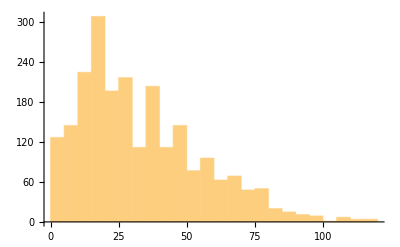

```mathematica
LeafCount/@testdata⟦easycases⟧//Histogram
```

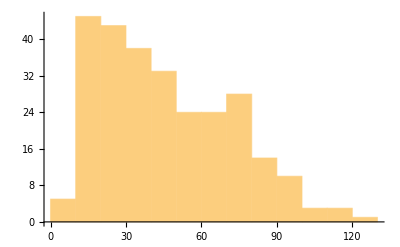

```mathematica
LeafCount/@testdata⟦middlecases⟧//Histogram
```

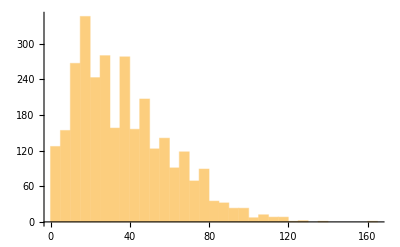

```mathematica
LeafCount/@testdata//Histogram
```

```mathematica
ii=409;
index = hardcases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
```

{{2 a[2]+5 a[1] a[2]-4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},-2 b[0]+5 b[0]^2+3 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+130 a[1] a[2]^2+260 a[1]^2 a[2]^2-80 a[2]^3-260 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]-5 a[1] a[2]+4 a[2]^2,-3 a[1]^2+2 a[1] a[2]},2 b[0]+5 b[0]^2-5 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+120 a[1] a[2]^2+235 a[1]^2 a[2]^2-80 a[2]^3-240 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]+5 a[1] a[2]+4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},2 b[0]+5 b[0]^2-3 b[0] b[1]}

-4 a[2]+10 a[1] a[2]-30 a[1]^2 a[2]+75 a[1]^3 a[2]+28 a[2]^2-70 a[1] a[2]^2+110 a[1]^2 a[2]^2-80 a[2]^3+140 a[1] a[2]^3+80 a[2]^4

```mathematica
ii=59;
index = easycases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
```

{{3 a[1]-5 a[1]^2-2 a[2] a[3],-5 a[3]},b[0]-2 b[1]-3 b[1]^2}

3 a[1]-5 a[1]^2+10 a[3]-2 a[2] a[3]-75 a[3]^2

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

#### further training on longer data (Exp56) comparing with Exp55_1,2

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_1_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.201,0.799}

```mathematica
exp55$1result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
result⟦1;;4⟧
```

{0.,0.,0.196,0.804}

```mathematica
exp55$2result=result⟦5⟧;
```

```mathematica
result=EvaluateSimplificationResult3["./Evaluation/Exp55/test_set_Exp55.txt","./Evaluation/Exp56/experiment56_predictions.txt"];
result⟦1;;4⟧
exp56$result=result⟦5⟧;
```

{0.,0.,0.179333,0.820667}

```mathematica
exp55results=Table[{exp55$1result⟦i⟧,exp55$2result⟦i⟧},{i,Length[exp55$1result]}];
```

```mathematica
{N[Count[exp55results,{False,False}]/Length[exp55results]],N[Count[exp55results,{False,True}]/Length[exp55results]],N[Count[exp55results,{True,False}]/Length[exp55results]],N[Count[exp55results,{True,True}]/Length[exp55results]]}
```

{0.153333,0.0476667,0.0426667,0.756333}

```mathematica
hardcases=Position[exp55results,{False,False}]//Flatten;
easycases=Position[exp55results,{True,True}]//Flatten;
middlecases=Position[exp55results,{True,False}|{False,True}]//Flatten;
```

```mathematica
exp56onhard = Table[exp56$result⟦hardcases⟦i⟧⟧,{i,Length[hardcases]}];
exp56oneasy = Table[exp56$result⟦easycases⟦i⟧⟧,{i,Length[easycases]}];
{N[Count[exp56onhard,True]/Length[exp56onhard]],N[Count[exp56oneasy,True]/Length[exp56oneasy]]}
```

{0.13913,0.981049}

```mathematica
testdata=TestData$FromFile2["./Evaluation/Exp55/test_set_Exp55.txt"];
testdataanswer=TestData$FromFile2$answers["./Evaluation/Exp55/test_set_Exp55.txt"];
predictiondata1=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_1_predictions.txt"];
predictiondata2=PredictionData$FromFile2["./Evaluation/Exp55/experiment55_2_predictions.txt"];
```

```mathematica
Length[hardcases]
Length[easycases]
```

460

2269

```mathematica
LeafCount/@testdata⟦hardcases⟧//N//Mean
LeafCount/@testdata⟦easycases⟧//N//Mean
```

49.0565

32.6152

```mathematica
LeafCount/@testdata⟦hardcases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata⟦easycases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata⟦middlecases⟧//Histogram
```

-Graphics-

```mathematica
LeafCount/@testdata//Histogram
```

-Graphics-

```mathematica
ii=409;
index = hardcases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand
%%%-%//Expand;
```

{{2 a[2]+5 a[1] a[2]-4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},-2 b[0]+5 b[0]^2+3 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+130 a[1] a[2]^2+260 a[1]^2 a[2]^2-80 a[2]^3-260 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]-5 a[1] a[2]+4 a[2]^2,-3 a[1]^2+2 a[1] a[2]},2 b[0]+5 b[0]^2-5 b[0] b[1]}

-4 a[2]-10 a[1] a[2]-30 a[1]^2 a[2]-75 a[1]^3 a[2]+28 a[2]^2+120 a[1] a[2]^2+235 a[1]^2 a[2]^2-80 a[2]^3-240 a[1] a[2]^3+80 a[2]^4

{{-2 a[2]+5 a[1] a[2]+4 a[2]^2,-5 a[1]^2+5 a[1] a[2]},2 b[0]+5 b[0]^2-3 b[0] b[1]}

-4 a[2]+10 a[1] a[2]-30 a[1]^2 a[2]+75 a[1]^3 a[2]+28 a[2]^2-70 a[1] a[2]^2+110 a[1]^2 a[2]^2-80 a[2]^3+140 a[1] a[2]^3+80 a[2]^4

```mathematica
ii=59;
index = easycases⟦ii⟧;
testdataanswer⟦index⟧
testdata⟦index⟧
predictiondata1⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
predictiondata2⟦index⟧
%⟦2⟧/.{b[0]->%⟦1,1⟧,b[1]->%⟦1,2⟧}//Expand;
%%%-%//Expand;
```

{{3 a[1]-5 a[1]^2-2 a[2] a[3],-5 a[3]},b[0]-2 b[1]-3 b[1]^2}

3 a[1]-5 a[1]^2+10 a[3]-2 a[2] a[3]-75 a[3]^2

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

{{-5 a[3],3 a[1]-5 a[1]^2-2 a[2] a[3]},-2 b[0]-3 b[0]^2+b[1]}

### finetuning and generalization evaluation

#### Finetuning Exp54 model on gen5 ( 10240 data, 1, shuffle, lr_decay off )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.112333,0.887667}

{0.,0.123,0.877}

{0.,0.114,0.886}

{0.,0.138333,0.861667}

{0.,0.127,0.873}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.146,0.854}

{0.,0.112667,0.887333}

{0.,0.101667,0.898333}

{0.,0.113333,0.886667}

{0.,0.0986667,0.901333}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_tiny_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.174667,0.825333}

{0.,0.142667,0.857333}

{0.,0.148667,0.851333}

{0.,0.165,0.835}

{0.,0.154,0.846}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_tiny_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«7 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.736,0.264}

{0.,0.224,0.776}

{0.,0.145333,0.854667}

{0.,0.113667,0.886333}

{0.,0.155,0.845}

#### Finetuning Exp54 model on gen5 ( 0.025M data, 1, best, shuffle, lr_decay off )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.0813333,0.918667}

{0.,0.068,0.932}

{0.,0.0703333,0.929667}

{0.,0.0723333,0.927667}

{0.,0.08,0.92}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0746667,0.925333}

{0.,0.0516667,0.948333}

{0.,0.043,0.957}

{0.,0.0566667,0.943333}

{0.,0.0556667,0.944333}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_small_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.819667,0.180333}

{0.,0.152,0.848}

{0.,0.105333,0.894667}

{0.,0.105333,0.894667}

{0.,0.771,0.229}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch2_predictions.txt",False,True];
(*result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_small_epoch5_predictions.txt",False,True];*)
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

```mathematica
result0
result1
result2
```

{0.,0.740667,0.259333}

{0.,0.103667,0.896333}

{0.,0.732667,0.267333}

#### Finetuning Exp54 model on gen5 ( 0.05M data, 1 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_middle_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.071,0.929}

{0.,0.08,0.92}

{0.,0.0553333,0.944667}

{0.,0.0483333,0.951667}

{0.,0.0463333,0.953667}

#### Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_middle_epoch5_predictions.txt",False,True];
```

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0493333,0.950667}

{0.,0.0326667,0.967333}

{0.,0.0343333,0.965667}

{0.,0.0313333,0.968667}

{0.,0.039,0.961}

#### Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_middle_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«9 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«35 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«21 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0993333,0.900667}

{0.,0.0746667,0.925333}

{0.,0.0283333,0.971667}

{0.,0.0183333,0.981667}

{0.,0.0156667,0.984333}

#### Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_middle_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.066,0.934}

{0.,0.0316667,0.968333}

{0.,0.0453333,0.954667}

{0.,0.051,0.949}

{0.,0.037,0.963}

#### middle Finetuning Exp54 model on gen5 ( 0.1M data, 5 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp54$gen5$result[0] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_predictions.txt",False,True];
exp54$gen5$result[1]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train1_predictions.txt",False,True];
exp54$gen5$result[2]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train2_predictions.txt",False,True];
exp54$gen5$result[3] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train3_predictions.txt",False,True];
exp54$gen5$result[4]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train4_predictions.txt",False,True];
exp54$gen5$result[5]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_train5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«638 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«47 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«102 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«47 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«62 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«59 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«122 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«148 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«200 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«128 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«49 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«358 more identical outputs»

```mathematica
exp54$gen5$result[0]
exp54$gen5$result[1]
exp54$gen5$result[2]
exp54$gen5$result[3]
exp54$gen5$result[4]
exp54$gen5$result[5]
```

{0.,0.763667,0.236333}

{0.,0.0393333,0.960667}

{0.,0.232333,0.767667}

{0.,0.195333,0.804667}

{0.,0.235,0.765}

{0.,0.238333,0.761667}

#### middle Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp54$gen6$result[0] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_predictions.txt",False,True];
exp54$gen6$result[1]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train1_predictions.txt",False,True];
exp54$gen6$result[2]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train2_predictions.txt",False,True];
exp54$gen6$result[3]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train3_predictions.txt",False,True];
exp54$gen6$result[4] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train4_predictions.txt",False,True];
exp54$gen6$result[5]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_train5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

```mathematica
exp54$gen6$result[0]
exp54$gen6$result[1]
exp54$gen6$result[2]
exp54$gen6$result[3]
exp54$gen6$result[4]
exp54$gen6$result[5]
```

{0.,0.763,0.237}

{0.,0.127667,0.872333}

{0.,0.0233333,0.976667}

{0.,0.0266667,0.973333}

{0.,0.0176667,0.982333}

{0.,0.0493333,0.950667}

#### middle Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp33$gen5$result[0] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_predictions.txt",False,True];
exp33$gen5$result[1]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train1_predictions.txt",False,True];
exp33$gen5$result[2]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train2_predictions.txt",False,True];
exp33$gen5$result[3] = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train3_predictions.txt",False,True];
exp33$gen5$result[4]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train4_predictions.txt",False,True];
exp33$gen5$result[5]  = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_train5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«14 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«12 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«16 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«20 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«10 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«6 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

```mathematica
exp33$gen5$result[0]
exp33$gen5$result[1]
exp33$gen5$result[2]
exp33$gen5$result[3]
exp33$gen5$result[4]
exp33$gen5$result[5]
```

{0.,0.767,0.233}

{0.,0.0943333,0.905667}

{0.,0.0726667,0.927333}

{0.,0.188,0.812}

{0.,0.233333,0.766667}

{0.,0.245667,0.754333}

#### middle Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
exp33$gen6$result[0] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_predictions.txt",False,True];
exp33$gen6$result[1]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train1_predictions.txt",False,True];
exp33$gen6$result[2]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train2_predictions.txt",False,True];
exp33$gen6$result[3]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train3_predictions.txt",False,True];
exp33$gen6$result[4] = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train4_predictions.txt",False,True];
exp33$gen6$result[5]= EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_train5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«25 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
exp33$gen6$result[0]
exp33$gen6$result[1]
exp33$gen6$result[2]
exp33$gen6$result[3]
exp33$gen6$result[4]
exp33$gen6$result[5]
```

{0.,0.740667,0.259333}

{0.,0.0626667,0.937333}

{0.,0.0266667,0.973333}

{0.,0.027,0.973}

{0.,0.144333,0.855667}

{0.,0.0303333,0.969667}

#### bigger Finetuning Exp54 model on gen5 ( 0.25M data )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp54_gen5_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«552 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«12 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.763667,0.236333}

{0.,0.200667,0.799333}

{0.,0.024,0.976}

{0.,0.006,0.994}

{0.,0.00933333,0.990667}

{0.,0.00533333,0.994667}

#### bigger Finetuning Exp54 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(*result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_test.txt","./Evaluation/gen6/exp54_gen6_big_predictions.txt",False,True];*)
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp54_gen6_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.0136667,0.986333}

{0.,0.0156667,0.984333}

{0.,0.0123333,0.987667}

{0.,0.00833333,0.991667}

{0.,0.00866667,0.991333}

#### bigger Finetuning Exp33 model on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«122 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«110 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«23 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«31 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«11 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«37 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«63 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«63 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«55 more identical outputs»

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

```mathematica
result1
result2
result3
result4
result5
```

{0.,0.225,0.775}

{0.,0.119333,0.880667}

{0.,0.0156667,0.984333}

{0.,0.0186667,0.981333}

{0.,0.0166667,0.983333}

#### bigger Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.027,0.973}

{0.,0.0156667,0.984333}

{0.,0.011,0.989}

{0.,0.008,0.992}

{0.,0.768333,0.231667}

#### larger batch Finetuning Exp33 model on gen5 ( best, 0.5M data )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen5/gen5_big_test.txt","./Evaluation/gen5/exp33_gen5_bigbig_epoch5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«15 more identical outputs»

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.767,0.233}

{0.,0.0133333,0.986667}

{0.,0.003,0.997}

{0.,0.00366667,0.996333}

{0.,0.013,0.987}

{0.,0.00933333,0.990667}

#### larger batch Finetuning Exp33 model on gen6

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result0 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_big_predictions.txt",False,True];
result1 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch1_predictions.txt",False,True];
result2 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch2_predictions.txt",False,True];
result3 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch3_predictions.txt",False,True];
result4 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch4_predictions.txt",False,True];
result5 = EvaluateSimplificationResult["./Evaluation/gen6/gen6_big_test.txt","./Evaluation/gen6/exp33_gen6_bigbig_epoch5_predictions.txt",False,True];
```

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

```mathematica
result0
result1
result2
result3
result4
result5
```

{0.,0.740667,0.259333}

{0.,0.003,0.997}

{0.,0.00233333,0.997667}

{0.,0.001,0.999}

{0.,0.002,0.998}

{0.,0.00133333,0.998667}

#### interpretation

```mathematica
datasize = {0,10240,25000,50000,100000};
exp54$gen5={0.23633,0.8876666666666667,0.9186666666666666,0.929,0.9606666666666667};
exp54$gen6={0.854,};
exp33$gen5={0.233,0.8253333333333334,0.8963333333333333,0.9006666666666666,0.9056666666666666};
exp33$gen6={0.264,};
```

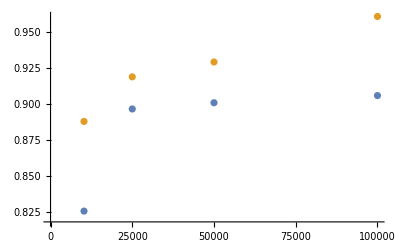

```mathematica
ListPlot[{Transpose[{datasize⟦2;;⟧,exp33$gen5⟦2;;⟧}],Transpose[{datasize⟦2;;⟧,exp54$gen5⟦2;;⟧}]}]
```

```mathematica
s1=a1+a2-a3;
s2=a2+a3-2a1;
s3=a3+3a1-a2;
s1^3+s2^3+s3^3-3s1 s2 s3//Expand
%//FullSimplify//FullSimplify
s1^3//Expand
s2^3//Expand
s3^3//Expand
-3s1 s2 s3//Expand
```

38 a1^3-9 a1^2 a2-6 a1 a2^2+4 a2^3+15 a1^2 a3-24 a1 a2 a3+6 a1 a3^2+4 a3^3

(2 a1+a2+a3) (19 a1^2-2 a1 (7 a2+a3)+4 (a2^2-a2 a3+a3^2))

a1^3+3 a1^2 a2+3 a1 a2^2+a2^3-3 a1^2 a3-6 a1 a2 a3-3 a2^2 a3+3 a1 a3^2+3 a2 a3^2-a3^3

-8 a1^3+12 a1^2 a2-6 a1 a2^2+a2^3+12 a1^2 a3-12 a1 a2 a3+3 a2^2 a3-6 a1 a3^2+3 a2 a3^2+a3^3

27 a1^3-27 a1^2 a2+9 a1 a2^2-a2^3+27 a1^2 a3-18 a1 a2 a3+3 a2^2 a3+9 a1 a3^2-3 a2 a3^2+a3^3

18 a1^3+3 a1^2 a2-12 a1 a2^2+3 a2^3-21 a1^2 a3+12 a1 a2 a3-3 a2^2 a3-3 a2 a3^2+3 a3^3

```mathematica
(x+y+z)(x^2+y^2+z^2-x y-y z-z x)//Expand
```

x^3+y^3-3 x y z+z^3

```mathematica
10 a^4-400 a^3+3994 a^2+120a//FullSimplify
```

2 (-20+a) a (-3+5 (-20+a) a)

### new experiments

#### new experiment 1 (5 2 20 4)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
new1$128$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_128_predictions.txt"];
new1$256$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_256_predictions.txt"];
new1$384$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_384_predictions.txt"];
new1$512$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new1/exp_new1_512_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
new1$128$result
new1$256$result
new1$384$result
new1$512$result
```

{0.,0.596,0.404}

{0.,0.028,0.972}

{0.,0.0243333,0.975667}

{0.,0.029,0.971}

```mathematica
testdata=TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/new1/exp_new1_128_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=4;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
PolySimplifyWithHint[{%%%⟦1⟧,%%%⟦2⟧},False,True]
```

{715-963 a[1]+431 a[1]^2-72 a[1]^3+4 a[1]^4,13-9 a[1]+a[1]^2}

{14-9 a[1]+a[1]^2}

1-5 s+4 s^2

3 s+4 s^2

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
```

#### new experiment 2 (split dataset)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
new2$128$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_128_predictions.txt"];
new2$256$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_256_predictions.txt"];
new2$384$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_384_predictions.txt"];
new2$512$result=EvaluateSimplificationResult["./Evaluation/new1/test_set_new1.txt","./Evaluation/new2/exp_new2_512_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
new2$128$result
new2$256$result
new2$384$result
new2$512$result
```

{0.,0.625,0.375}

{0.,0.0273333,0.972667}

{0.,0.026,0.974}

{0.,0.0246667,0.975333}

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
data2={{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}};
```

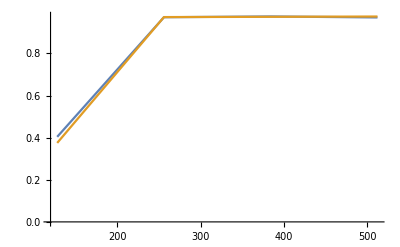

```mathematica
ListLinePlot[{data1,data2}]
```

```mathematica
?BarChart
```

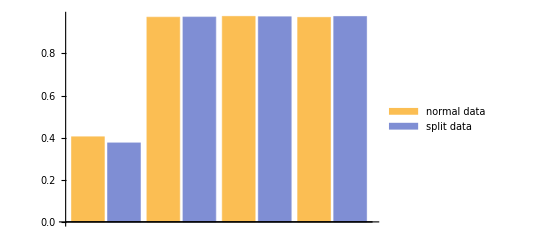

BarChart::ldata: {{{128,0.404},{256,0.972},{384,0.97567},{512,0.971}},{{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}}} is not a valid dataset or list of datasets.

BarChart[{{{128,0.404},{256,0.972},{384,0.97567},{512,0.971}},{{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}}}]

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
data2={{128,0.375},{256,0.9727},{384,0.974},{512,0.97533}};
data = {{0.404,0.375},{0.972,0.9727},{0.97567,0.974},{0.971,0.97533}};
BarChart[data,ChartLegends->{"normal data","split data"},BarSpacing->0.1]
```

#### Finetuning new1, new2 on gen5

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1 = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_predictions.txt",False,True];
result$new2= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_predictions.txt",False,True];
```

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

```mathematica
result$new1
result$new2
```

{0.,0.943333,0.0566667}

{0.,0.937667,0.0623333}

```mathematica
result$new1$2560[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train1_predictions.txt",False,True];
result$new1$2560[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train2_predictions.txt",False,True];
result$new1$2560[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_2560_train3_predictions.txt",False,True];
Table[result$new1$2560[i]⟦3⟧,{i,3}]//Mean
result$new2$2560[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train1_predictions.txt",False,True];
result$new2$2560[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train2_predictions.txt",False,True];
result$new2$2560[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_2560_train3_predictions.txt",False,True];
Table[result$new2$2560[i]⟦3⟧,{i,3}]//Mean
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

0.543556

JaehaFormat$Parser failure : tail=!={}

0.635

```mathematica
result$new1$5120[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train1_predictions.txt",False,True];
result$new1$5120[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train2_predictions.txt",False,True];
result$new1$5120[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_5120_train3_predictions.txt",False,True];
Table[result$new1$5120[i]⟦3⟧,{i,3}]//Mean
result$new2$5120[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train1_predictions.txt",False,True];
result$new2$5120[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train2_predictions.txt",False,True];
result$new2$5120[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_5120_train3_predictions.txt",False,True];
Table[result$new2$5120[i]⟦3⟧,{i,3}]//Mean
```

0.763889

0.848444

```mathematica
result$new1$10240[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train1_predictions.txt",False,True];
result$new1$10240[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train2_predictions.txt",False,True];
result$new1$10240[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_10240_train3_predictions.txt",False,True];
Table[result$new1$10240[i]⟦3⟧,{i,3}]//Mean
result$new2$10240[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train1_predictions.txt",False,True];
result$new2$10240[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train2_predictions.txt",False,True];
result$new2$10240[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_10240_train3_predictions.txt",False,True];
Table[result$new2$10240[i]⟦3⟧,{i,3}]//Mean
```

0.826667

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

JaehaFormat$Parser failure : tail=!={}

0.904778

```mathematica
result$new1$25k[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train1_predictions.txt",False,True];
result$new1$25k[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train2_predictions.txt",False,True];
result$new1$25k[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_25k_train3_predictions.txt",False,True];
Table[result$new1$25k[i]⟦3⟧,{i,3}]//Mean
result$new2$25k[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train1_predictions.txt",False,True];
result$new2$25k[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train2_predictions.txt",False,True];
result$new2$25k[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_25k_train3_predictions.txt",False,True];
Table[result$new2$25k[i]⟦3⟧,{i,3}]//Mean
```

JFP$ReadN wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

0.869111

JFP$ReadN wrong : can't read term from {}

0.910444

```mathematica
result$new1$50k[1] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train1_predictions.txt",False,True];
result$new1$50k[2] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train2_predictions.txt",False,True];
result$new1$50k[3] = EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new1_512_gen5_50k_train3_predictions.txt",False,True];
Table[result$new1$50k[i]⟦3⟧,{i,3}]//Mean
result$new2$50k[1]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train1_predictions.txt",False,True];
result$new2$50k[2]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train2_predictions.txt",False,True];
result$new2$50k[3]= EvaluateSimplificationResult["./Evaluation/new_gen5/new_gen5_test.txt","./Evaluation/new_gen5/exp_new2_512_gen5_50k_train3_predictions.txt",False,True];
Table[result$new2$50k[i]⟦3⟧,{i,3}]//Mean
```

0.901222

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«4 more identical outputs»

0.931

```mathematica
new1$2560=Table[{2560,result$new1$2560[i]⟦3⟧},{i,3}]
new1$5120=Table[{5120,result$new1$5120[i]⟦3⟧},{i,3}]
new1$10240=Table[{10240,result$new1$10240[i]⟦3⟧},{i,3}]
new1$25k=Table[{25000,result$new1$25k[i]⟦3⟧},{i,3}]
new1$50k=Table[{50000,result$new1$50k[i]⟦3⟧},{i,3}]
new1$total=new1$2560~Join~new1$5120~Join~new1$10240~Join~new1$25k~Join~new1$50k;
```

{{2560,0.533333},{2560,0.544667},{2560,0.552667}}

{{5120,0.761},{5120,0.731667},{5120,0.799}}

{{10240,0.817667},{10240,0.838667},{10240,0.823667}}

{{25000,0.874667},{25000,0.875},{25000,0.857667}}

{{50000,0.891333},{50000,0.901333},{50000,0.911}}

```mathematica
new2$2560=Table[{2560,result$new2$2560[i]⟦3⟧},{i,3}]
new2$5120=Table[{5120,result$new2$5120[i]⟦3⟧},{i,3}]
new2$10240=Table[{10240,result$new2$10240[i]⟦3⟧},{i,3}]
new2$25k=Table[{25000,result$new2$25k[i]⟦3⟧},{i,3}]
new2$50k=Table[{50000,result$new2$50k[i]⟦3⟧},{i,3}]
new2$total=new2$2560~Join~new2$5120~Join~new2$10240~Join~new2$25k~Join~new2$50k;
```

{{2560,0.543333},{2560,0.703333},{2560,0.658333}}

{{5120,0.829667},{5120,0.863667},{5120,0.852}}

{{10240,0.914667},{10240,0.900667},{10240,0.899}}

{{25000,0.913667},{25000,0.895667},{25000,0.922}}

{{50000,0.932667},{50000,0.926333},{50000,0.934}}

```mathematica
groupedData$new1=GroupBy[new1$total,First->Last]
groupedData$new2=GroupBy[new2$total,First->Last]
meanAndVariance$new1={#,Mean[groupedData$new1[#]],Variance[groupedData$new1[#]]}&/@Keys[groupedData$new1];
meanAndVariance$new2={#,Mean[groupedData$new2[#]],Variance[groupedData$new2[#]]}&/@Keys[groupedData$new2];
meanData$new1=meanAndVariance$new1[[All,{1,2}]];
errorBars$new1=meanAndVariance$new1[[All,3]];
meanData$new2=meanAndVariance$new2[[All,{1,2}]];
errorBars$new2=meanAndVariance$new2[[All,3]];
```

<|2560→{0.533333,0.544667,0.552667},5120→{0.761,0.731667,0.799},10240→{0.817667,0.838667,0.823667},25000→{0.874667,0.875,0.857667},50000→{0.891333,0.901333,0.911}|>

<|2560→{0.543333,0.703333,0.658333},5120→{0.829667,0.863667,0.852},10240→{0.914667,0.900667,0.899},25000→{0.913667,0.895667,0.922},50000→{0.932667,0.926333,0.934}|>

```mathematica
errorBar[{x_,y_},err_]:={Line[{{x,y-err},{x,y+err}}],(*Vertical error bar*)Line[{{x-0.05,y-err},{x+0.05,y-err}}],(*Bottom cap*)Line[{{x-0.05,y+err},{x+0.05,y+err}}]  (*Top cap*)};
```

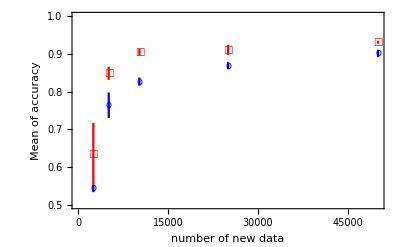

```mathematica
Needs["ErrorBarPlots`"];
plot1=ErrorListPlot[Thread[{meanData$new1,ErrorBar[Sqrt[#]]&/@errorBars$new1}],PlotMarkers->{"o",10},PlotStyle->Blue,PlotLegends->"based on normal data"];
plot2=ErrorListPlot[Thread[{meanData$new2,ErrorBar[Sqrt[#]]&/@errorBars$new2}],PlotMarkers->{"□",10},PlotStyle->Red,PlotLegends->"based on split data"];

Show[plot1,plot2,Frame->True,FrameLabel->{"number of new data","Mean of accuracy"},PlotRange->{{0,50000},{0.5,1.0}},ScalingFunctions->{"Log10",None}]
```

#### (test_new1 & train_new2 duplication test)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
TrainData$FromFile[filename_]:=Module[{data},data=(DeleteCases[#1,""]&)[StringSplit[Import[filename],"\n"|"?"]];data=data⟦1;;-2;;2⟧;data=(DeleteCases[#1,""]&)[StringSplit[data,"$"]];data=data/.str_String:>JF$Parser[str];data]
```

```mathematica
SetDirectory[NotebookDirectory[]]
new1$test = TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
new2$train=TrainData$FromFile["../../dataset_storage/datasets/new2/train_set_new2_test.txt"];
```

/Users/jaeha/inequality/MMA_package

```mathematica
new2$train⟦7⟧
```

{192+1054 a[1]+1011 a[1]^2-322 a[1]^3+2687 a[1]^4-810 a[1]^5+910 a[1]^6+140 a[1]^7+5 a[1]^8}

```mathematica
dupcheck=Table[new1$test⟦i,1⟧,{i,Length[new1$test]}]~Join~Table[new2$train⟦i,1⟧,{i,Length[new2$train]}];
Length[dupcheck]
Length[DeleteDuplicates[dupcheck]]
```

{19-176 a[1]+716 a[1]^2-1594 a[1]^3+2158 a[1]^4-1180 a[1]^5+65 a[1]^6+70 a[1]^7+5 a[1]^8,-2+8 a[1]-18 a[1]^2+7 a[1]^3+a[1]^4}

```mathematica
?PredictionData$FromFile
```

#### Finetuning new1, new2 on gen7

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1$gen7$constant = {0,0,0,0,0,0};
result$new1$gen7$linear ={0,0,0,0,0,0};
result$new1$gen7$quadratic ={0,0,0,0,0,0};
result$new1$gen7$cubic={0,0,0,0,0,0};
```

```mathematica
(* without training *)
```

```mathematica
result$new1$gen7$constant⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦1⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦1⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_cube_predictions.txt",False,True]
```

{0.,0.444667,0.555333}

{0.,1.,0.}

{0.,1.,0.}

{0.,1.,0.}

```mathematica
(* with 2560 training *)
```

```mathematica
result$new1$gen7$constant⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦2⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_2560_cube_predictions.txt",False,True]
```

{0.,0.166667,0.833333}

{0.,0.995,0.005}

{0.,1.,0.}

Part::take: Cannot take positions 2 through -1 in {}.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{}⟦2;;-1;;2⟧,$].

JFP$Read wrong : can't read term from {}

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[{}⟦2;;-1;;2⟧,False].

Set::shape: Lists {coeff$78147593} and {} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

$Aborted

```mathematica
(* with 5120 training *)
```

```mathematica
result$new1$gen7$constant⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦3⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_5120_cube_predictions.txt",False,True]
```

{0.,0.129667,0.870333}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{0.,0.994333,0.00566667}

{0.,0.996667,0.00333333}

{0.,1.,0.}

```mathematica
(* with 10240 training *)
```

```mathematica
result$new1$gen7$constant⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦4⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_10240_cube_predictions.txt",False,True]
```

{0.,0.0893333,0.910667}

{0.,0.990667,0.00933333}

{0.,0.998333,0.00166667}

{0.,0.992,0.008}

```mathematica
(* with 25k training *)
```

```mathematica
result$new1$gen7$constant⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦5⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_25k_cube_predictions.txt",False,True]
```

{0.,0.09,0.91}

{0.,0.996667,0.00333333}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

{0.,0.999667,0.000333333}

{0.,1.,0.}

```mathematica
(* with 50k training *)
```

```mathematica
result$new1$gen7$constant⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_constant_predictions.txt",False,True]
result$new1$gen7$linear⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_linear_predictions.txt",False,True]
result$new1$gen7$quadratic⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_quadratic_predictions.txt",False,True]
result$new1$gen7$cubic⟦6⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen7/exp_new1_512_gen7_50k_cube_predictions.txt",False,True]
```

{0.,0.0756667,0.924333}

JFP$ReadN wrong : can't read term from {}

{0.,0.999667,0.000333333}

{0.,1.,0.}

JFP$Read wrong : can't read term from {}

{0.,0.999333,0.000666667}

#### Finetuning new1, new2 on gen8

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$new1$gen8$constant = {0,0,0,0,0,0};
result$new1$gen8$linear ={0,0,0,0,0,0};
result$new1$gen8$quadratic ={0,0,0,0,0,0};
result$new1$gen8$cubic={0,0,0,0,0,0};
```

```mathematica
(* with 2560 training *)
```

```mathematica
result$new1$gen8$constant⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦2⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦2⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_2560_cube_predictions.txt",False,True]
```

{0.,0.574333,0.425667}

{0.,0.733667,0.266333}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«3 more identical outputs»

{0.,0.991,0.009}

JFP$Read wrong : can't read term from {}

{0.,0.993,0.007}

```mathematica
(* with 5120 training *)
```

```mathematica
result$new1$gen8$constant⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦3⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦3⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_5120_cube_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

{0.,0.509333,0.490667}

{0.,0.666667,0.333333}

{0.,0.991333,0.00866667}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.,0.993667,0.00633333}

```mathematica
(* with 10240 training *)
```

```mathematica
result$new1$gen8$constant⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦4⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦4⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_10240_cube_predictions.txt",False,True]
```

JFP$Read wrong : can't read term from {}

{0.,0.535667,0.464333}

JFP$ReadN wrong : can't read term from {}

{0.,0.574333,0.425667}

{0.,0.992333,0.00766667}

{0.,0.985667,0.0143333}

```mathematica
(* with 25k training *)
```

```mathematica
result$new1$gen8$constant⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦5⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦5⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_25k_cube_predictions.txt",False,True]
```

{0.,0.549333,0.450667}

{0.,0.444333,0.555667}

JFP$Read wrong : can't read term from {}

{0.,0.998667,0.00133333}

JaehaFormat$Parser failure : tail=!={}

{0.,0.990667,0.00933333}

```mathematica
(* with 50k training *)
```

```mathematica
result$new1$gen8$constant⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_constant_predictions.txt",False,True]
result$new1$gen8$linear⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_linear_predictions.txt",False,True]
result$new1$gen8$quadratic⟦6⟧ = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_quadratic_predictions.txt",False,True]
result$new1$gen8$cubic⟦6⟧= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_new1_512_gen8_50k_cube_predictions.txt",False,True]
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

{0.,0.519,0.481}

{0.,0.389,0.611}

{0.,0.992,0.008}

{0.,0.998,0.002}

#### train on gen8 and test on constant, linear, quadratic, cubic

```mathematica
result$gen8$constant= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_constant_test.txt","./Evaluation/new_gen8/exp_gen8_512_constant_predictions.txt",False,True]
result$gen8$linear= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_linear_test.txt","./Evaluation/new_gen8/exp_gen8_512_linear_predictions.txt",False,True]
result$gen8$quadratic = EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_quadratic_test.txt","./Evaluation/new_gen8/exp_gen8_512_quadratic_predictions.txt",False,True]
result$gen8$cubic= EvaluateSimplificationResult["./Evaluation/new_gen7/gen7_cube_test.txt","./Evaluation/new_gen8/exp_gen8_512_cube_predictions.txt",False,True]
```

JaehaFormat$Parser failure : tail=!={}

{0.,0.594667,0.405333}

JFP$ReadN wrong : can't read term from {}

{0.,0.150333,0.849667}

{0.,0.995,0.005}

{0.,0.999333,0.000666667}

#### new experiment 3 (5 2 20 4 without constraint)

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
result$l4$512=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l4_512_predictions.txt"];
result$l4$768=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l4_768_2_predictions.txt"];
result$l5$512=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l5_512_2_predictions.txt"];
result$l5$768=EvaluateSimplificationResult["./Evaluation/new3/test_set_new3.txt","./Evaluation/new3/new3_l5_768_2_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

```mathematica
result$l4$512
result$l4$768
result$l5$512
result$l5$768
```

{0.,0.247333,0.752667}

{0.,0.244333,0.755667}

{0.,0.818667,0.181333}

{0.,0.245667,0.754333}

```mathematica
testdata=TestData$FromFile["./Evaluation/new1/test_set_new1.txt"];
predictiondata=PredictionData$FromFile["./Evaluation/new1/exp_new1_128_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

```mathematica
index=4;
testdata⟦index⟧
predictiondata⟦index⟧
PolySimplifyWithHint[{%%⟦1⟧,%},False,True]
PolySimplifyWithHint[{%%%⟦1⟧,%%%⟦2⟧},False,True]
```

{715-963 a[1]+431 a[1]^2-72 a[1]^3+4 a[1]^4,13-9 a[1]+a[1]^2}

{14-9 a[1]+a[1]^2}

1-5 s+4 s^2

3 s+4 s^2

```mathematica
data1={{128,0.404},{256,0.972},{384,0.97567},{512,0.971}};
```

### 2-language experiment

#### 2languages exp

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__best_80000__on_40000_1.txt"]
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__best_80000__on_40000_2.txt"]*)
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_2.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_on_40000_2.txt"]*)
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_best_40000__on_40000_1.txt"]
(*EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_2.txt","./Evaluation/2Lexp/prediction_set_40000_1_40000_2_best_40000__on_40000_2.txt"]*)
```

{0.,0.824333,0.175667}

JaehaFormat$Parser failure : tail=!={}

{0.,0.804,0.196}

{0.,0.802333,0.197667}

{0.,0.817667,0.182333}

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_200000__on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_100000_2_100000__on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200000_1.txt","./Evaluation/2Lexp2/prediction_set_200000_1_on_200000_1.txt"]
```

{0.,0.105667,0.894333}

{0.,0.793333,0.206667}

{0.,0.121,0.879}

{0.,0.780333,0.219667}

#### scaling law for without constraint case

weight decay 0.01, learning_rate decay on, final token 10 ( turned out weight decay was actually 0.1 )

```mathematica
(* 1 language *)
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_40000_1_on_40000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_100000_1_on_100000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200000_1.txt","./Evaluation/2Lexp2/prediction_set_200000_1_on_200000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_400000_1.txt","./Evaluation/2Lexp2/prediction_set_400000_1_on_400000_1.txt"]
EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_800000_1.txt","./Evaluation/2Lexp2/prediction_set_800000_1_on_800000_1.txt"]
```

{0.,0.824333,0.175667}

{0.,0.793333,0.206667}

{0.,0.780333,0.219667}

JFP$Read wrong : can't read term from {}

{0.,0.787,0.213}

{0.,0.782667,0.217333}

```mathematica
(* 2 languages *)
```

```mathematica
result=
{
{40,EvaluateSimplificationResult["./Evaluation/2Lexp/test_set_40000_1.txt","./Evaluation/2Lexp/prediction_set_80000__on_40000_1.txt"]⟦3⟧},
{150,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_150000_.txt","./Evaluation/2Lexp2/prediction_set_150000__on_150000_.txt"]⟦3⟧},
{190,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_190000_.txt","./Evaluation/2Lexp2/prediction_set_190000__on_190000_.txt"]⟦3⟧},
{195,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_195000_.txt","./Evaluation/2Lexp2/prediction_set_195000__on_195000_.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_100000_1.txt","./Evaluation/2Lexp2/prediction_set_200000__on_100000_1.txt"]⟦3⟧},
{200.1,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_200100_.txt","./Evaluation/2Lexp2/prediction_set_200100__on_200100_.txt"]⟦3⟧},
{203.75,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_203750_.txt","./Evaluation/2Lexp2/prediction_set_203750__on_203750_.txt"]⟦3⟧},
{205,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_205000_.txt","./Evaluation/2Lexp2/prediction_set_205000__on_205000_.txt"]⟦3⟧},
{210,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_210000_.txt","./Evaluation/2Lexp2/prediction_set_210000__on_210000_.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp2/test_set_400000_.txt","./Evaluation/2Lexp2/prediction_set_400000__on_400000_.txt"]⟦3⟧}
}
```

JaehaFormat$Parser failure : tail=!={}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{40,0.196},{150,0.217667},{190,0.201},{200,0.894333},{200.1,0.908},{203.75,0.217},{400,0.215667}}

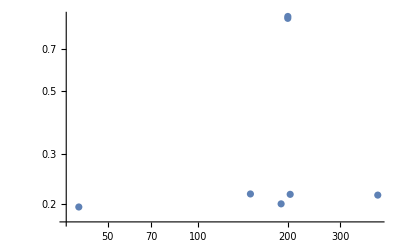

```mathematica
ListLogLogPlot[result⟦1;;7⟧]
```

weight decay 0.1, learning_rate decay on, final token 20000

```mathematica
(* 1 language *)
```

```mathematica
result2 =
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_25003_1.txt","./Evaluation/2Lexp3/prediction_set_25003_1_on_25003_1.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_50003_1.txt","./Evaluation/2Lexp3/prediction_set_50003_1_on_50003_1.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_100003_1.txt","./Evaluation/2Lexp3/prediction_set_100003_1_on_100003_1.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_200003_1.txt","./Evaluation/2Lexp3/prediction_set_200003_1_on_200003_1.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_400003_1.txt","./Evaluation/2Lexp3/prediction_set_400003_1_on_400003_1.txt"]⟦3⟧}
}
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{25,0.155333},{50,0.186333},{100,0.22},{200,0.223},{400,0.226}}

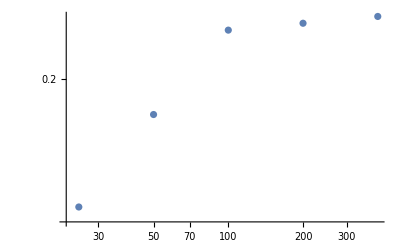

```mathematica
ListLogLogPlot[result2]
```

```mathematica
(* 2 languages *)
```

```mathematica
result=
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_25003_.txt","./Evaluation/2Lexp3/prediction_set_25003__on_25003_.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_50003_.txt","./Evaluation/2Lexp3/prediction_set_50003__on_50003_.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_100003_.txt","./Evaluation/2Lexp3/prediction_set_100003__on_100003_.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_200003_.txt","./Evaluation/2Lexp3/prediction_set_200003__on_200003_.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp3/test_set_400003_.txt","./Evaluation/2Lexp3/prediction_set_400003__on_400003_.txt"]⟦3⟧}
}
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

{{25,0.443},{50,0.724333},{100,0.846333},{200,0.216333},{400,0.225333}}

weight decay 0.1, learning_rate decay on, final token 10000

```mathematica
(* 1 language *)
```

```mathematica
result3 =
{
{25,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_25004_1.txt","./Evaluation/2Lexp4/prediction_set_25004_1_on_25004_1.txt"]⟦3⟧},
{50,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_50004_1.txt","./Evaluation/2Lexp4/prediction_set_50004_1_on_50004_1.txt"]⟦3⟧},
{100,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_100004_1.txt","./Evaluation/2Lexp4/prediction_set_100004_1_on_100004_1.txt"]⟦3⟧},
{200,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_200004_1.txt","./Evaluation/2Lexp4/prediction_set_200004_1_on_200004_1.txt"]⟦3⟧},
{400,EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_400004_1.txt","./Evaluation/2Lexp4/prediction_set_400004_1_on_400004_1.txt"]⟦3⟧}
}
```

JFP$Read wrong : can't read term from {}

{{25,0.151667},{50,0.520333},{100,0.214333},{200,0.221667},{400,0.215}}

```mathematica
(* turning off shuffle *)
```

```mathematica
EvaluateSimplificationResult["./Evaluation/2Lexp4/test_set_100005_1.txt","./Evaluation/2Lexp4/prediction_set_100005_1_on_100005_1.txt"]
```

{0.,0.76,0.24}

### multi-variable

#### 5 variables ( Exp 60 ) - (5, 3, 5, 3 ), 3 terms each ( 5var2 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var2.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var2_predictions.txt"];
```

JaehaFormat$Parser failure : tail=!={}

JFP$Read wrong : can't read term from {}

JaehaFormat$Parser failure : tail=!={}

```mathematica
predictiondata⟦1⟧
```

{-2 b[0]^2 b[1]-2 b[0] b[1] b[2]-2 b[1]^2 b[2],-a[1]^2 a[2]-a[0] a[3]^2-2 a[0]^2 a[4],-a[2] a[3]^2-2 a[0]^2 a[4],-3 a[1] a[3]^2,-2 a[0]^2 a[1]-4 a[1]^2 a[2],-2 a[0]^2 a[1]-2 a[0] a[1] a[2]-4 a[1]^2 a[2]}

```mathematica
index =324;
testdata⟦index⟧
predictiondata[[index,1]]/.{b[a_]:>predictiondata⟦index,a+2⟧}//Expand
(%-%%)===0
```

-60 a[0]^3 a[1]^6+40 a[0] a[1]^8-48 a[0]^4 a[1]^4 a[2]+80 a[0]^2 a[1]^6 a[2]-76 a[1]^7 a[2] a[3]-102 a[0] a[1]^6 a[2] a[4]-90 a[0]^3 a[1]^3 a[2]^2 a[4]+60 a[0] a[1]^5 a[2]^2 a[4]-36 a[0]^4 a[1] a[2]^3 a[4]+60 a[0]^2 a[1]^3 a[2]^3 a[4]-114 a[1]^4 a[2]^3 a[3] a[4]+60 a[0] a[1]^6 a[4]^2+48 a[0]^2 a[1]^4 a[2] a[4]^2-108 a[0] a[1]^3 a[2]^3 a[4]^2-45 a[0]^3 a[2]^4 a[4]^2+45 a[0] a[1]^2 a[2]^4 a[4]^2-54 a[1] a[2]^5 a[3] a[4]^2+90 a[0] a[1]^3 a[2]^2 a[4]^3+36 a[0]^2 a[1] a[2]^3 a[4]^3-18 a[0] a[2]^5 a[4]^3+45 a[0] a[2]^4 a[4]^4

-240 a[0]^3 a[1]^6-400 a[0] a[1]^8-48 a[0]^2 a[1]^5 a[2] a[3]+256 a[1]^7 a[2] a[3]+36 a[0]^3 a[1]^4 a[2] a[4]-192 a[0] a[1]^6 a[2] a[4]-360 a[0]^3 a[1]^3 a[2]^2 a[4]-600 a[0] a[1]^5 a[2]^2 a[4]-36 a[0]^2 a[1]^2 a[2]^3 a[3] a[4]+384 a[1]^4 a[2]^3 a[3] a[4]-240 a[0] a[1]^6 a[4]^2+27 a[0]^3 a[1] a[2]^3 a[4]^2-288 a[0] a[1]^3 a[2]^3 a[4]^2-135 a[0]^3 a[2]^4 a[4]^2-225 a[0] a[1]^2 a[2]^4 a[4]^2-48 a[0] a[1]^4 a[2] a[3] a[4]^2+144 a[1] a[2]^5 a[3] a[4]^2+36 a[0]^2 a[1]^3 a[2] a[4]^3-360 a[0] a[1]^3 a[2]^2 a[4]^3-108 a[0] a[2]^5 a[4]^3-36 a[0] a[1] a[2]^3 a[3] a[4]^3+27 a[0]^2 a[2]^3 a[4]^4-135 a[0] a[2]^4 a[4]^4

False

```mathematica
simplification$result = Table[testdata[[i]]===(predictiondata[[i,1]]/.{b[a_]:>predictiondata⟦i,a+2⟧}//Expand),{i,1,Length@predictiondata}];
```

Part::partw: Part 6 of {5 b[0]^2 b[1]-5 b[1]^2 b[3]-b[2]^2 b[4],3 a[1] a[3]^2+5 a[2] a[3]^2+4 a[1] a[3] a[4],-a[1]^3+4 a[0] a[3]^2+5 a[2] a[3]^2,2 a[0] a[1]^2+3 a[0] a[2] a[4]+5 a[0] a[3] a[4],-4 a[0] a[2]^2+5 a[0] a[3]^2-a[0] a[2] a[4]} does not exist.

```mathematica
Count[simplification$result,False]
Count[simplification$result,True]
```

2991

9

#### 5 variables ( Exp 61 ) - (5, 3, 5, 1 ), 9, 5 terms each ( 5var3 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var3.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var3_finetune_predictions.txt"];
```

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

```mathematica
predictiondata⟦1⟧
```

{-5 b[0]^2 b[1]-b[0] b[1]^2-5 b[0]^2 b[2]-2 b[0] b[1] b[2]-5 b[1]^2 b[2]-b[0] b[2]^2-5 b[0]^2 b[3]-2 b[0] b[2] b[3]-2 b[0] b[3]^2,4 a[3]-a[4],-3 a[2],-2 a[4],a[0]+3 a[1]-4 a[2],-4 a[0]-3 a[1]-2 a[2]-5 a[3]-4 a[4]}

```mathematica
index =324;
testdata⟦index⟧
predictiondata[[index,1]]/.{b[a_]:>predictiondata⟦index,a+2⟧}//Expand
(%-%%)===0
```

15 a[0]^3+36 a[0]^2 a[1]-320 a[1]^3+92 a[0]^2 a[2]-112 a[0] a[1] a[2]+189 a[0] a[2]^2+40 a[1] a[2]^2-148 a[2]^3-12 a[0]^2 a[4]-40 a[0] a[2] a[4]+32 a[2]^2 a[4]

17 a[0]^3-40 a[0]^2 a[1]-320 a[1]^3+188 a[0]^2 a[2]-300 a[0] a[1] a[2]+713 a[0] a[2]^2-592 a[1] a[2]^2+908 a[2]^3

False

```mathematica
simplification$result = Table[testdata[[i]]===(predictiondata[[i,1]]/.{b[a_]:>predictiondata⟦i,a+2⟧}//Expand),{i,1,Length@predictiondata}];
```

```mathematica
Count[simplification$result,False]
Count[simplification$result,True]
```

3000

0

#### 5 variables ( Exp 62 ) - (5, 3, 5, 1 ), 10, 5 terms each ( 5var4 )

```mathematica
Get["MMA2TxtFormat3.m"];
```

```mathematica
(* TestData$FromFile2 : only read question *)
```

```mathematica
testdata=TestData$FromFile2["./Evaluation/multi/test_set_5var4.txt"];
```

```mathematica
(* read model's prediction and split in & *)
```

```mathematica
predictiondata=PredictionData$FromFile3["./Evaluation/multi/multi_l4_512_5var4_predictions.txt"];
```

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«13 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«1 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«19 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

«2 more identical outputs»

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«4 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«10 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«5 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«6 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«9 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«8 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«2 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«7 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«3 more identical outputs»

JFP$Read wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

JFP$ReadN wrong : can't read term from {}

«1 more identical outputs»